# 三角非構造格子から滑らかな表面を作る方法について

## 形状関数（既に決まっている重み）とサンプル点で補間

```mathematica
(*過去の計算結果などの情報を全て消去する*)
ClearAll["Global`*"];
```

### 形状関数

形状関数 （よくNと表記されれる） とは何か理解する．

まずは，解析対象の物体を用意する．
有限要素法FEMや境界要素法BEMなどは，まず，解析対象の物体を有限の数の節点をつなぎ合わせ表現する．
節点は，物体の形を表現するための座標を持つだけでなく，同時にその座標における物体の温度や速度，圧力，色，など様々な情報を持たせておく．

次に，節点同士をつなぎ合わせた物体の変形を計算することを考えよう．
当然，物体表面の節点において，何らかの情報が与えられている必要がある．
与えられた既知変数を手がかりに，物体のまだわかっていない未知変数を計算することを，境界値問題を解くという．
境界値問題を解くためには，変数間の関係を表す微分方程式を満足するように未知変数を決めればいい．

しかし，微分演算子d/dtや積分を含むような，紙に書くような微分方程式そのままを，計算機（コンピュータ）が扱うことはできない．
計算機が扱えるのは，微分方程式を行列に書き換えたものだけだ．これを離散化という．

微分方程式→行列，この離散化を行うために，形状関数が必要なる．

### 1次のラグランジュ補間（線形補間）

```mathematica
shape1[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{t0,t1,t2}
];
shape1FixedRange[t0_,t1_]:=Module[{t2},
(*t1=t1IN*(1-t0);
t2=1-t0-t1;
*)
Return@{t0, t1*(1-t0),(-1+t0) (-1+t1)}
];
```

### 2次のラグランジュ補間

```mathematica
shape2[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2}];
```

```mathematica
Simplify@shape2[t0,t1*(1-t0)]
```

{t0 (-1+2 t0),(-1+t0) t1 (1+2 (-1+t0) t1),(-1+t0) (1+2 t0 (-1+t1)-2 t1) (-1+t1),-4 (-1+t0) t0 t1,-4 (-1+t0)^2 (-1+t1) t1,4 (-1+t0) t0 (-1+t1)}

```mathematica
Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};
{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

Tri[0][t0_,t1_]=Dot[shape2[t0,t1],Xs]
Tri[1][t0_,t1_]=Dot[shape2[1-t0,1/2-t1],As];
Tri[2][t0_,t1_]=Dot[shape2[1-t1,t1+t0-1/2],Bs];
Tri[3][t0_,t1_]=Dot[shape2[t0+t1,1/2-t0],Cs];

tmp=Dot[shape2[t0,t1],{
Tri[1][t0,t1],
Tri[2][t0,t1],
Tri[3][t0,t1],
(Tri[0][t0,t1]+Tri[1][t0,t1]+Tri[2][t0,t1])/3,
(Tri[0][t0,t1]+Tri[2][t0,t1]+Tri[3][t0,t1])/3,
(Tri[0][t0,t1]+Tri[1][t0,t1]+Tri[3][t0,t1])/3
}];

(*tmp[t0_,t1_]=Dot[shape2[t0,t1],{
α*Tri[1][t0,t1],
β*Tri[2][t0,t1],
γ*Tri[3][t0,t1],
(Tri[0][t0,t1]+Tri[1][t0,t1]+Tri[2][t0,t1])/3,
(Tri[0][t0,t1]+Tri[2][t0,t1]+Tri[3][t0,t1])/3,
(Tri[0][t0,t1]+Tri[1][t0,t1]+Tri[3][t0,t1])/3
}]*)

shapeQuadQuad[t0_,t1_]=Collect[Table[Coefficient[tmp,x[i]],{i,0,11,1}],{t0,t1},Simplify]
```

t0 (-1+2 t0) x[0]+t1 (-1+2 t1) x[1]+(-1+2 (1-t0-t1)) (1-t0-t1) x[2]+4 t0 t1 x[3]+4 (1-t0-t1) t1 x[4]+4 t0 (1-t0-t1) x[5]

{-t0/3-(8 t0^4)/3+t0^3 (16/3-(16 t1)/3)+t0^2 (-4/3+(16 t1)/3-(16 t1^2)/3),-t1/3-(4 t1^2)/3-(16 t0^2 t1^2)/3+(16 t1^3)/3-(8 t1^4)/3+t0 ((16 t1^2)/3-(16 t1^3)/3),1-(8 t0^4)/3+t0^3 (16/3-(16 t1)/3)-(7 t1)/3-(4 t1^2)/3+(16 t1^3)/3-(8 t1^4)/3+t0^2 (-4/3+(16 t1)/3-(16 t1^2)/3)+t0 (-7/3+(8 t1)/3+(16 t1^2)/3-(16 t1^3)/3),-(4 t0^4)/3+t0^3 (-4/3-(8 t1)/3)-(5 t1)/3+(13 t1^2)/3-(4 t1^3)/3-(4 t1^4)/3+t0^2 (13/3-(16 t1)/3+(8 t1^2)/3)+t0 (-5/3+10 t1-(16 t1^2)/3-(8 t1^3)/3),-(4 t0^4)/3+t0^3 (20/3-(8 t1)/3)+(8 t1)/3+(8 t1^2)/3-(32 t1^3)/3+(16 t1^4)/3+t0^2 (-23/3+(20 t1)/3+(8 t1^2)/3)+t0 (7/3-(20 t1)/3-(20 t1^2)/3+(32 t1^3)/3),(16 t0^4)/3+(7 t1)/3-(23 t1^2)/3+(20 t1^3)/3-(4 t1^4)/3+t0^3 (-32/3+(32 t1)/3)+t0^2 (8/3-(20 t1)/3+(8 t1^2)/3)+t0 (8/3-(20 t1)/3+(20 t1^2)/3-(8 t1^3)/3),t0 (-t1/3+(2 t1^2)/3)+t0^2 (-(2 t1)/3+(4 t1^2)/3),(4 t0^4)/3+t0^3 (-4/3+(8 t1)/3)+t0 (1/3-t1+(2 t1^2)/3)+t0^2 (-1/3-(2 t1)/3+(4 t1^2)/3),t1/3-t1^2/3-(4 t1^3)/3+(4 t1^4)/3+t0^2 ((2 t1)/3+(4 t1^2)/3)+t0 (-t1-(2 t1^2)/3+(8 t1^3)/3),t0 (-t1/3-(2 t1^2)/3)+t0^2 ((2 t1)/3+(4 t1^2)/3),(4 t0^4)/3+t0^3 (-4+(8 t1)/3)+t0 (-1+(5 t1)/3-(2 t1^2)/3)+t0^2 (11/3-(14 t1)/3+(4 t1^2)/3),-t1+(11 t1^2)/3-4 t1^3+(4 t1^4)/3+t0^2 (-(2 t1)/3+(4 t1^2)/3)+t0 ((5 t1)/3-(14 t1^2)/3+(8 t1^3)/3)}

```mathematica
Tri[0][t0_,t1_]=Dot[shape2[t0,t1],Xs]
Tri[1][t0_,t1_]=Dot[shape2[1-t0,1/2-t1],As];
Tri[2][t0_,t1_]=Dot[shape2[1-t1,t1+t0-1/2],Bs];
Tri[3][t0_,t1_]=Dot[shape2[t0+t1,1/2-t0],Cs];
```

t0 (-1+2 t0) x[0]+t1 (-1+2 t1) x[1]+(-1+2 (1-t0-t1)) (1-t0-t1) x[2]+4 t0 t1 x[3]+4 (1-t0-t1) t1 x[4]+4 t0 (1-t0-t1) x[5]

```mathematica
eq[0][t0_,t1_]=tmp[t0,t1]-(Tri[0][t0,t1]+Tri[1][t0,t1])/2;
eq[1][t0_,t1_]=tmp[t0,t1]-(Tri[0][t0,t1]+Tri[2][t0,t1])/2;
eq[2][t0_,t1_]=tmp[t0,t1]-(Tri[0][t0,t1]+Tri[3][t0,t1])/2;
Reduce[{eq[0][1/2,1/4]==0,eq[1][1/4,1/2]==0,eq[2][1/4,1/4]==0},{α,β,γ}]
```

x[3]==-x[4]-x[5]+x[6]/18+x[7]/18+x[8]/18+x[9]/18+x[10]/18+x[11]/18+8/9 (1/8 (-(3 x[3])/4-(3 x[4])/8+x[7]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(7 x[3])/4+(11 x[4])/8+x[5]/4-x[7]/8-x[8]/8-x[9]/8)+1/12 (-x[0]/8-x[2]/8+(13 x[3])/8+(13 x[4])/8+x[5]/4-x[7]/8-x[10]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(11 x[3])/8+(7 x[4])/4+x[5]/4-x[8]/8-x[9]/8-x[10]/8)+1/8 (-(3 x[3])/8-(3 x[4])/4+x[10]/8))[1/4,1/2]+8/9 (1/8 (-(3 x[4])/8-(3 x[5])/4+x[6]/8)+1/12 (-x[0]/8-x[1]/8+x[3]/4+(13 x[4])/8+(13 x[5])/8-x[6]/8-x[9]/8)+1/8 (-(3 x[4])/4-(3 x[5])/8+x[9]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(11 x[4])/8+(7 x[5])/4-x[6]/8-x[10]/8-x[11]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(7 x[4])/4+(11 x[5])/8-x[9]/8-x[10]/8-x[11]/8))[1/4,1/4]+8/9 (1/6 (x[0]/4-x[1]/8-x[2]/8+(7 x[3])/4+x[4]/4+(11 x[5])/8-x[6]/8-x[7]/8-x[8]/8)+1/8 (-(3 x[3])/4-(3 x[5])/8+x[8]/8)+1/6 (x[0]/4-x[1]/8-x[2]/8+(11 x[3])/8+x[4]/4+(7 x[5])/4-x[6]/8-x[7]/8-x[11]/8)+1/12 (-x[1]/8-x[2]/8+(13 x[3])/8+x[4]/4+(13 x[5])/8-x[8]/8-x[11]/8)+1/8 (-(3 x[3])/8-(3 x[5])/4+x[11]/8))[1/2,1/4]&&x[1]==x[2]+2 x[4]+4 x[5]-x[6]/9-x[7]/9+(2 x[8])/9+(2 x[9])/9-(4 x[10])/9-(4 x[11])/9+32/9 (1/8 (-(3 x[3])/4-(3 x[4])/8+x[7]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(7 x[3])/4+(11 x[4])/8+x[5]/4-x[7]/8-x[8]/8-x[9]/8)+1/12 (-x[0]/8-x[2]/8+(13 x[3])/8+(13 x[4])/8+x[5]/4-x[7]/8-x[10]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(11 x[3])/8+(7 x[4])/4+x[5]/4-x[8]/8-x[9]/8-x[10]/8)+1/8 (-(3 x[3])/8-(3 x[4])/4+x[10]/8))[1/4,1/2]-64/9 (1/8 (-(3 x[4])/8-(3 x[5])/4+x[6]/8)+1/12 (-x[0]/8-x[1]/8+x[3]/4+(13 x[4])/8+(13 x[5])/8-x[6]/8-x[9]/8)+1/8 (-(3 x[4])/4-(3 x[5])/8+x[9]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(11 x[4])/8+(7 x[5])/4-x[6]/8-x[10]/8-x[11]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(7 x[4])/4+(11 x[5])/8-x[9]/8-x[10]/8-x[11]/8))[1/4,1/4]-16/9 (1/6 (x[0]/4-x[1]/8-x[2]/8+(7 x[3])/4+x[4]/4+(11 x[5])/8-x[6]/8-x[7]/8-x[8]/8)+1/8 (-(3 x[3])/4-(3 x[5])/8+x[8]/8)+1/6 (x[0]/4-x[1]/8-x[2]/8+(11 x[3])/8+x[4]/4+(7 x[5])/4-x[6]/8-x[7]/8-x[11]/8)+1/12 (-x[1]/8-x[2]/8+(13 x[3])/8+x[4]/4+(13 x[5])/8-x[8]/8-x[11]/8)+1/8 (-(3 x[3])/8-(3 x[5])/4+x[11]/8))[1/2,1/4]&&x[0]==x[2]+4 x[4]+2 x[5]+(2 x[6])/9+(2 x[7])/9-x[8]/9-x[9]/9-(4 x[10])/9-(4 x[11])/9-16/9 (1/8 (-(3 x[3])/4-(3 x[4])/8+x[7]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(7 x[3])/4+(11 x[4])/8+x[5]/4-x[7]/8-x[8]/8-x[9]/8)+1/12 (-x[0]/8-x[2]/8+(13 x[3])/8+(13 x[4])/8+x[5]/4-x[7]/8-x[10]/8)+1/6 (-x[0]/8+x[1]/4-x[2]/8+(11 x[3])/8+(7 x[4])/4+x[5]/4-x[8]/8-x[9]/8-x[10]/8)+1/8 (-(3 x[3])/8-(3 x[4])/4+x[10]/8))[1/4,1/2]-64/9 (1/8 (-(3 x[4])/8-(3 x[5])/4+x[6]/8)+1/12 (-x[0]/8-x[1]/8+x[3]/4+(13 x[4])/8+(13 x[5])/8-x[6]/8-x[9]/8)+1/8 (-(3 x[4])/4-(3 x[5])/8+x[9]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(11 x[4])/8+(7 x[5])/4-x[6]/8-x[10]/8-x[11]/8)+1/6 (-x[0]/8-x[1]/8+x[2]/4+x[3]/4+(7 x[4])/4+(11 x[5])/8-x[9]/8-x[10]/8-x[11]/8))[1/4,1/4]+32/9 (1/6 (x[0]/4-x[1]/8-x[2]/8+(7 x[3])/4+x[4]/4+(11 x[5])/8-x[6]/8-x[7]/8-x[8]/8)+1/8 (-(3 x[3])/4-(3 x[5])/8+x[8]/8)+1/6 (x[0]/4-x[1]/8-x[2]/8+(11 x[3])/8+x[4]/4+(7 x[5])/4-x[6]/8-x[7]/8-x[11]/8)+1/12 (-x[1]/8-x[2]/8+(13 x[3])/8+x[4]/4+(13 x[5])/8-x[8]/8-x[11]/8)+1/8 (-(3 x[3])/8-(3 x[5])/4+x[11]/8))[1/2,1/4]

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
Show[
ListPointPlot3D[Flatten[Table[Dot[shapeQuadQuad[t0,t1],ps],{t0,0,1,0.05},{t1,0,1-t0,0.05}],1],PlotStyle->Blue],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
(*Manipulate[Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red],
ListPointPlot3D[Flatten[Table[Dot[shapeQuadQuad[t0,t1],ps],{t0,0,a,0.1},{t1,0,b,0.1}],1],PlotStyle->Blue]}
]
,{a,0,1,.1},{b,0,1,.1}]*)
```

### 3次のラグランジュ補間

```mathematica
N012[t_]:=t/2*(3*t-1)*(3*t-2);
N345678[t0_,t1_]:=9/2*t0*t1*(3*t0-1);
shape3[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{
N012[t0],
N012[t1],
N012[t2],
N345678[t0,t1],
N345678[t1,t0],
N345678[t1,t2],
N345678[t2,t1],
N345678[t2,t0],
N345678[t0,t2],
27*t0*t1*t2}];
(*f3[u_(*6点*),t0_,t1_,X4_,X6_,X8_]:=Module[{V,X,tab},
Do[V[i-1]=u[[i]],{i,1,Length[u],1}];(*6点*)
X[0]=V[0];
X[1]=V[1];
X[2]=V[2];
X[4]=X4;
X[6]=X6;
X[8]=X8;
X[3]=1/9 (16 V[3]+X[0]+X[1]-9 X[4]);
X[5]=1/9 (16 V[4]+X[1]+X[2]-9 X[6]);
X[7]=1/9 (16 V[5]+X[0]+X[2]-9 X[8]);
X[9]=-V[0]/9-V[1]/9-V[2]/9+(4 V[3])/9+(4 V[4])/9+(4 V[5])/9;
tab=Table[X[i-1],{i,1,10,1}];
Return[Dot[shape3[t0,t1],tab]];
];
*)
(*f3[u_(*6点*),t0_,t1_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Module[{V,X,tab},
Do[V[i-1]=u[[i]],{i,1,Length[u],1}];(*6点*)
X[0]=V[0];
X[1]=V[1];
X[2]=V[2];
X[4]=X4;
X[6]=X6;
X[8]=X8;
X[3]=X3;(*1/9 (16 V[3]+X[0]+X[1]-9 X[4]);*)
X[5]=X5;(*1/9 (16 V[4]+X[1]+X[2]-9 X[6]);*)
X[7]=X7;(*1/9 (16 V[5]+X[0]+X[2]-9 X[8]);*)
X[9]=X9;(*=Dot[{V[0],V[1],V[2],V[3],V[4],V[5]},shape2[1/3,1/3]];*)
tab=Table[X[i-1],{i,1,10,1}];
Return[Dot[shape3[t0,t1],tab]];
];*)
f3[u_(*6点*),t0_,t1_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Module[{V,X,tab},
Do[V[i-1]=u[[i]],{i,1,Length[u],1}];(*6点*)
X[0]=V[0];
X[1]=V[1];
X[2]=V[2];

X[4]=X4;
X[6]=X6;
X[8]=X8;
X[3]=X3;
X[5]=X5;
X[7]=X7;
X[9]=X9;(*=Dot[{V[0],V[1],V[2],V[3],V[4],V[5]},shape2[1/3,1/3]];*)
tab=Table[X[i-1],{i,1,10,1}];
Return[Dot[shape3[t0,t1],tab]];
];
```

```mathematica
Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};
{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

Tri[0][t0_,t1_]=Simplify@f3[Xs(*6点*),t0,t1,X3,X4,X5,X6,X7,X8,X9];
Tri[1][t0_,t1_]=Simplify@f3[As(*6点*),t0,t1,a3,a4,a5,a6,a7,a8,a9];
Tri[2][t0_,t1_]=Simplify@f3[Bs(*6点*),t0,t1,b3,b4,b5,b6,b7,b8,b9];
Tri[3][t0_,t1_]=Simplify@f3[Cs(*6点*),t0,t1,c3,c4,c5,c6,c7,c8,c9];

DTriFixt0Dt0[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0fix,t1],t0]/.t0fix->t0;
DTriFixt1Dt0[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,t1fix],t0]/.t1fix->t1;
DTriFixt2Dt0[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,1-t0-t2fix],t0]/.t2fix->t2;

DTriFixt0Dt1[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0fix,t1],t1]/.t0fix->t0;
DTriFixt1Dt1[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,t1fix],t1]/.t1fix->t1;
DTriFixt2Dt1[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,1-t0-t2fix],t1]/.t2fix->t2;

DTriFixt0Dt2[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0fix,t1],t2]/.t0fix->t0;
DTriFixt1Dt2[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,t1fix],t2]/.t1fix->t1;
DTriFixt2Dt2[{i_,points_,t0_,t1_,t2_}]=Simplify@D[Tri[i][t0,1-t0-t2fix],t2]/.t2fix->t2;

(*(*4つの三角形は3,4,5節点で滑らかに繋がって欲しい，まずは夫々の三角形にとって，3,4,5節点はどのパラメタで表されるか整理する*)
ξ012[0(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={0,5,1/2,0,1/2};
ξ012[0(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={0,3,1/2,1/2,0};
ξ012[0(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={0,4,0,1/2,1/2};

ξ012[1(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={1,3,1/2,1/2,0};
ξ012[1(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={1,5,1/2,0,1/2};
(*ξ012[1(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={1,0,1,0,0};*)

(*ξ012[2(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={2,0,1,0,0};*)
ξ012[2(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={2,3,1/2,1/2,0};
ξ012[2(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={2,5,1/2,0,1/2};

ξ012[3(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={3,5,1/2,0,1/2};
(*ξ012[3(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={3,0,1,0,0};*)
ξ012[3(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={3,3,1/2,1/2,0};
*)
ξ012[0(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={t0->1/2,t1->0,t2->1/2};
ξ012[0(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={t0->1/2,t1->1/2,t2->0};
ξ012[0(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={t0->0,t1->1/2,t2->1/2};

ξ012[1(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={t0->1/2,t1->1/2,t2->0};
ξ012[1(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={t0->1/2,t1->0,t2->1/2};
(*ξ012[1(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={1,0,1,0,0};*)

(*ξ012[2(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={2,0,1,0,0};*)
ξ012[2(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={t0->1/2,t1->1/2,t2->0};
ξ012[2(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={t0->1/2,t1->0,t2->1/2};

ξ012[3(*三角形にとってのパラメタである*)][5(*0の三角形にとっての点の番号*)]={t0->1/2,t1->0,t2->1/2};
(*ξ012[3(*三角形にとってのパラメタである*)][3(*0の三角形にとっての点の番号*)]={3,0,1,0,0};*)
ξ012[3(*三角形にとってのパラメタである*)][4(*0の三角形にとっての点の番号*)]={t0->1/2,t1->1/2,t2->0};
```

```mathematica
eq[0]=Collect[Tri[0][t0,t1]-Tri[1][1-t0,1/2-t1],{t0,t1},Simplify];
eq[1]=Collect[Tri[0][t0,t1]-Tri[2][1-t1,1-t0-(1/2-t0)],{t0,t1},Simplify];
eq[2]=Collect[Tri[0][t0,t1]-Tri[3][t1+1/2,1/2-t0],{t0,t1},Simplify];
eq[3]=D[eq[0],t0];
eq[4]=D[eq[1],t0];
eq[5]=D[eq[2],t0];
eq[6]=D[eq[0],t1];
eq[7]=D[eq[1],t1];
eq[8]=D[eq[2],t1];
n=8;
j=0;
Do[
EQ[j++]=eq[i]/.{t0->1/2,t1->0};
EQ[j++]=eq[i]/.{t0->1/2,t1->1/2};
EQ[j++]=eq[i]/.{t0->0,t1->1/2};
,{i,0,8,1}]

Reduce[Table[EQ[i],{i,0,j-1,1}]==Table[0,{i,0,j-1,1}],{X3,X4,X5,X6,X7,X8,X9,a0,a1,a2,b0,b1,b2,c0,c1,c2}]
```

x[6]==x[11]&&x[4]==x[7]&&x[3]==x[7]&&x[0]==x[2]&&c8==(7 c9)/11-(8 x[1])/99+(8 x[2])/99+(53 x[7])/99-(14 x[10])/297-(37 x[11])/297&&c7==c9-(2 x[10])/27+(2 x[11])/27&&c6==(5 x[10])/27+(22 x[11])/27&&c5==(14 x[10])/27+(13 x[11])/27&&c4==c9+(14 x[10])/81-(14 x[11])/81&&c3==(7 c9)/11-(8 x[1])/99+(8 x[2])/99+(53 x[7])/99-(31 x[10])/891-(122 x[11])/891&&b7==b8-(4 c9)/11-(8 x[1])/99+(8 x[2])/99-x[5]/3+(20 x[7])/99+x[9]/3+(8 x[10])/297+(40 x[11])/297&&b5==-b6+(18 c9)/11+(56 x[1])/33-(56 x[2])/33+(14 x[7])/33+x[8]/9+x[9]/9-(4 x[10])/33-(16 x[11])/99&&b4==b6+b8/3-2 b9-(38 c9)/33-(40 x[1])/99+(40 x[2])/99-x[5]/9+(254 x[7])/99+x[8]/9-x[9]/9+(76 x[10])/891+(248 x[11])/891&&b3==-b6-b8/3+2 b9+(38 c9)/33+(40 x[1])/99-(40 x[2])/99+(2 x[5])/9-(26 x[7])/33+x[9]/9-(76 x[10])/891-(248 x[11])/891&&a8==x[7]&&a7==x[7]&&a6==6 a9-(35 c9)/11+(40 x[1])/99-(40 x[2])/99-(265 x[7])/99+(70 x[10])/297+(185 x[11])/297&&a5==6 a9-(31 c9)/11+(16 x[1])/33-(16 x[2])/33-(106 x[7])/33+(62 x[10])/297+(244 x[11])/297&&a4==c9-(2 x[10])/27+(2 x[11])/27&&a3==(7 c9)/11-(8 x[1])/99+(8 x[2])/99+(53 x[7])/99-(14 x[10])/297-(37 x[11])/297&&X3==(2 c9)/11-(7 x[1])/99+(2 x[2])/11+(26 x[7])/33-(4 x[10])/297-(20 x[11])/297&&X4==-(2 c9)/11+(2 x[1])/11-(7 x[2])/99+(98 x[7])/99+(4 x[10])/297+(20 x[11])/297&&X5==-(2 c9)/11+(2 x[1])/11-(7 x[2])/99+(98 x[7])/99+(4 x[10])/297+(20 x[11])/297&&X6==(2 c9)/11-(7 x[1])/99+(2 x[2])/11+(26 x[7])/33-(4 x[10])/297-(20 x[11])/297&&X7==(9 c9)/11-(4 x[1])/99+(5 x[2])/33+(7 x[7])/33-(2 x[10])/33-(8 x[11])/99&&X8==(9 c9)/11-(4 x[1])/99+(5 x[2])/33+(7 x[7])/33-(2 x[10])/33-(8 x[11])/99&&X9==(7 c9)/22-(23 x[1])/297+(4 x[2])/99+(163 x[7])/198-(7 x[10])/297-(8 x[11])/99

```mathematica
i=0;
{p[0],p[1],p[2]}={0,1/4,1/2};
(*通過条件*)
eq[i++]=(Tri[0][t0,t1]/.{t0->1/2,t1->1/2})-x[3];
eq[i++]=(Tri[0][t0,t1]/.{t0->0,t1->1/2})-x[4];
eq[i++]=(Tri[0][t0,t1]/.{t0->1/2,t1->0})-x[5];
k=0;
p6 = {Tri[k][1,0],Tri[k][0,1],Tri[k][0,0],Tri[k][1/2,1/2],Tri[k][0,1/2],Tri[k][1/2,0]};
(*eq[i++]=(Tri[k][t0,t1]/.{t0->1/3,t1->1/3})-Dot[p6,shape2[1/3,1/3]];*)

eq[i++]=(Tri[1][t0,t1]/.{t0->1/2,t1->1/2})-x[5];
eq[i++]=(Tri[1][t0,t1]/.{t0->0,t1->1/2})-x[0];
eq[i++]=(Tri[1][t0,t1]/.{t0->1/2,t1->0})-x[3];
k=1;
p6 = {Tri[k][1,0],Tri[k][0,1],Tri[k][0,0],Tri[k][1/2,1/2],Tri[k][0,1/2],Tri[k][1/2,0]};
(*eq[i++]=(Tri[k][t0,t1]/.{t0->1/3,t1->1/3})-Dot[p6,shape2[1/3,1/3]];*)

eq[i++]=(Tri[2][t0,t1]/.{t0->1/2,t1->1/2})-x[3];
eq[i++]=(Tri[2][t0,t1]/.{t0->0,t1->1/2})-x[1];
eq[i++]=(Tri[2][t0,t1]/.{t0->1/2,t1->0})-x[4];
k=2;
p6 = {Tri[k][1,0],Tri[k][0,1],Tri[k][0,0],Tri[k][1/2,1/2],Tri[k][0,1/2],Tri[k][1/2,0]};
(*eq[i++]=(Tri[k][t0,t1]/.{t0->1/3,t1->1/3})-Dot[p6,shape2[1/3,1/3]];*)

eq[i++]=(Tri[3][t0,t1]/.{t0->1/2,t1->1/2})-x[4];
eq[i++]=(Tri[3][t0,t1]/.{t0->0,t1->1/2})-x[2];
eq[i++]=(Tri[3][t0,t1]/.{t0->1/2,t1->0})-x[5];
k=3;
p6 = {Tri[k][1,0],Tri[k][0,1],Tri[k][0,0],Tri[k][1/2,1/2],Tri[k][0,1/2],Tri[k][1/2,0]};
(*eq[i++]=(Tri[k][t0,t1]/.{t0->1/3,t1->1/3})-Dot[p6,shape2[1/3,1/3]];
*)
(*１辺上で接線が一致*)
k=1;(*ok*)
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t0->1/2,t1->p[0]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t0->1/2,t1->p[1]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t0->1/2,t1->p[2]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[2]});

(*ok*)
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t0->1/2,t1->p[0]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t0->1/2,t1->p[1]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t0->1/2,t1->p[2]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[2]});


k=2;
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t1->1/2,t0->p[2]})-(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->p[2]});
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t1->1/2,t0->p[1]})-(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->p[1]});
eq[i++]=(D[Tri[0][t0,t1],t0]/.{t1->1/2,t0->p[0]})-(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->p[0]});

(*ok*)
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t1->1/2,t0->p[2]})+(D[Tri[k][t0,1-t0-t2],t0]/.{t0->1/2,t1->p[2],t2->1-1/2-p[2]});
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t1->1/2,t0->p[1]})+(D[Tri[k][t0,1-t0-t2],t0]/.{t0->1/2,t1->p[1],t2->1-1/2-p[1]});
eq[i++]=(D[Tri[0][t0,t1],t1]/.{t1->1/2,t0->p[0]})+(D[Tri[k][t0,1-t0-t2],t0]/.{t0->1/2,t1->p[0],t2->1-1/2-p[0]});


k=3;
eq[i++]=(D[Tri[0][t0,1-t0-t2],t0]/.{t2->1/2,t0->p[0]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(D[Tri[0][t0,1-t0-t2],t0]/.{t2->1/2,t0->p[1]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(D[Tri[0][t0,1-t0-t2],t0]/.{t2->1/2,t0->p[2]})+(D[Tri[k][t0,t1],t1]/.{t0->1/2,t1->1/2-p[2]});

(*ok*)
(*eq[i++]=(D[Tri[0][t0,1-t0-t2],t2]/.{t2->1/2,t0->p[0]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(D[Tri[0][t0,1-t0-t2],t2]/.{t2->1/2,t0->p[1]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(D[Tri[0][t0,1-t0-t2],t2]/.{t2->1/2,t0->p[2]})+(D[Tri[k][t0,t1],t0]/.{t0->1/2,t1->1/2-p[2]});
*)
tmp=Simplify[D[Tri[0][t0,1-t0-t2],t2]+D[Tri[k][t2,1/2-t0],t2]]/.t2->1/2;
tmp=CoefficientList[tmp,{t0}];
Column[tmp]
Do[eq[i++]=tmp[[j]],{j,1,Length[tmp],1}];

tmp=Simplify[D[Tri[0][t0,1-t0-t2],t2]+D[Tri[k][t2,1/2-t0],t2]]/.t2->1/2;
tmp=CoefficientList[tmp,{t0}];
Column[tmp]
Do[eq[i++]=tmp[[j]],{j,1,Length[tmp],1}];


(*１辺上で座標が一致*)
k=1;(*ok*)
(*eq[i++]=(Tri[0][t0,t1]/.{t0->1/2,t1->p[0]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(Tri[0][t0,t1]/.{t0->1/2,t1->p[1]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(Tri[0][t0,t1]/.{t0->1/2,t1->p[2]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[2]});
*)

tmp=Collect[Tri[0][1/2,t1]-Tri[k][1/2,1-1/2-t1],t1,Simplify];
tmp=CoefficientList[tmp,{t1}];
Column[tmp]
Do[eq[i++]=tmp[[j]],{j,1,Length[tmp],1}];

k=2;(*ok*)
(*eq[i++]=(Tri[0][t0,t1]/.{t1->1/2,t0->p[2]})-(Tri[k][t0,t1]/.{t0->1/2,t1->p[2]});
eq[i++]=(Tri[0][t0,t1]/.{t1->1/2,t0->p[1]})-(Tri[k][t0,t1]/.{t0->1/2,t1->p[1]});
eq[i++]=(Tri[0][t0,t1]/.{t1->1/2,t0->p[0]})-(Tri[k][t0,t1]/.{t0->1/2,t1->p[0]});
*)

tmp=Collect[Tri[0][t0,1/2]-Tri[k][1/2,t0],t0,Simplify];
tmp=CoefficientList[tmp,{t0}];
Column[tmp]
Do[eq[i++]=tmp[[j]],{j,1,Length[tmp],1}];

k=3;(*ok*)
(*eq[i++]=(Tri[0][t0,1-t0-t2]/.{t2->1/2,t0->p[0]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[0]});
eq[i++]=(Tri[0][t0,1-t0-t2]/.{t2->1/2,t0->p[1]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[1]});
eq[i++]=(Tri[0][t0,1-t0-t2]/.{t2->1/2,t0->p[2]})-(Tri[k][t0,t1]/.{t0->1/2,t1->1/2-p[2]});
*)

tmp=Collect[Tri[0][t0,1-t0-1/2]-Tri[k][1/2,1-1/2-t0],t0,Simplify];
tmp=CoefficientList[tmp,{t0}];
Column[tmp]
Do[eq[i++]=tmp[[j]],{j,1,Length[tmp],1}];

n=i-1;
Column@Table[Variables[eq[i]],{i,0,n,1}]
(*Solve[Table[eq[i],{i,0,n,1}]==Table[0,{i,0,n,1}],{Cen0,Cen1,Cen2,a0,a1,a2,a3,b0,b1,b2,b3,c0,c1,c2,c3}]*)
Reduce[Table[eq[i],{i,0,n,1}]==Table[0,{i,0,n,1}],{X3,X4,X5,X6,X7,X8,X9,a0,a1,a2,b0,b1,b2,c0,c1,c2}]
```

(9 c3)/2+(9 c4)/8-(9 c5)/8+(9 c6)/4+(9 c7)/4-(9 c8)/8-(27 c9)/4-(27 X5)/8+(27 X6)/8+x[1]/8-x[2]/8-x[3]/8-x[11]
-9 c3-9 c4+9 c5-18 c6-18 c7+9 c8+27 c9+(9 X3)/2-9 X4+(9 X5)/2-9 X6+9 X7-(9 X8)/2+(9 x[1])/2+9 x[11]
(27 c4)/2-(27 c5)/2+27 c6+(27 c7)/2-27 c9-(27 X3)/2+27 X4+(27 X5)/2+(27 X8)/2-27 X9-(27 x[1])/2-(27 x[11])/2

(9 c3)/2+(9 c4)/8-(9 c5)/8+(9 c6)/4+(9 c7)/4-(9 c8)/8-(27 c9)/4-(27 X5)/8+(27 X6)/8+x[1]/8-x[2]/8-x[3]/8-x[11]
-9 c3-9 c4+9 c5-18 c6-18 c7+9 c8+27 c9+(9 X3)/2-9 X4+(9 X5)/2-9 X6+9 X7-(9 X8)/2+(9 x[1])/2+9 x[11]
(27 c4)/2-(27 c5)/2+27 c6+(27 c7)/2-27 c9-(27 X3)/2+27 X4+(27 X5)/2+(27 X8)/2-27 X9-(27 x[1])/2-(27 x[11])/2

1/16 (-9 a3-9 a4+9 X7+9 X8-x[0]-x[2]+x[4]+x[6])
1/8 (9 a3+36 a4-9 a5+18 a6+18 a7-9 a8-54 a9+9 X3-18 X4-18 X5+9 X6-36 X7-9 X8+54 X9+8 x[1]+x[2]-x[6]-8 x[7])
-9/4 (3 a4-4 a5+5 a6+3 a7-6 a9-3 X4-5 X5+4 X6-3 X7+6 X9+2 x[1]-x[2]+x[6]-2 x[7])
-9/2 (3 a5-3 a6+3 X5-3 X6-x[1]+x[2]-x[6]+x[7])

1/16 (-9 b7-9 b8+9 X5+9 X6-x[1]-x[2]+x[5]+x[9])
1/8 (-9 b3+18 b4+18 b5-9 b6+36 b7+9 b8-54 b9-18 X3+9 X4-9 X5-36 X6+9 X7-18 X8+54 X9+8 x[0]+x[2]-8 x[8]-x[9])
-9/4 (3 b4+5 b5-4 b6+3 b7-6 b9-3 X3-3 X6+4 X7-5 X8+6 X9+2 x[0]-x[2]-2 x[8]+x[9])
9/2 (3 b5-3 b6+3 X7-3 X8+x[0]-x[2]-x[8]+x[9])

1/16 (-9 c3-9 c4+9 X5+9 X6-x[1]-x[2]+x[3]+x[10])
1/8 (9 c3+36 c4-9 c5+18 c6+18 c7-9 c8-54 c9-18 X3+9 X4-36 X5-9 X6+9 X7-18 X8+54 X9+8 x[0]+x[1]-x[10]-8 x[11])
-9/4 (3 c4-4 c5+5 c6+3 c7-6 c9-5 X3+4 X4-3 X5-3 X8+6 X9+2 x[0]-x[1]+x[10]-2 x[11])
-9/2 (3 c5-3 c6+3 X3-3 X4-x[0]+x[1]-x[10]+x[11])

{X5,X6,x[1],x[2],X7,X8,x[0],X3,X4,X9,x[3]}
{X5,X6,x[1],x[2],x[4]}
{X7,X8,x[0],x[2],x[5]}
{x[5],a3,a4,x[4],x[6]}
{x[0],a5,a6,x[6],x[7]}
{x[3],a7,a8,x[4],x[7]}
{x[3],b3,b4,x[5],x[8]}
{x[1],b5,b6,x[8],x[9]}
{x[4],b7,b8,x[5],x[9]}
{x[4],c3,c4,x[3],x[10]}
{x[2],c5,c6,x[10],x[11]}
{x[5],c7,c8,x[3],x[11]}
{X5,X6,x[1],X3,X4,X7,X8,X9,x[2],a3,a4,a5,a6,a7,a8,a9,x[6],x[7]}
{X5,X6,x[1],X3,X4,X7,X8,X9,x[2],a3,a4,a5,a6,a7,a8,x[6],x[7]}
{X5,X6,x[1],X3,X4,X7,X8,X9,x[2],a3,a4,a5,a6,a7,a8,a9,x[6],x[7]}
{X7,X8,x[0],x[2],a3,a4,a5,a6,a7,a8,a9,x[4],x[7]}
{X7,X8,x[0],X3,X4,X5,X6,X9,x[2],a3,a4,a5,a6,a7,a8,a9,x[4],x[7]}
{X7,X8,x[0],X3,X4,X5,X6,X9,x[2],a7,a8,x[4],x[7]}
{X7,X8,x[0],X3,X4,X5,X6,X9,x[2],b3,b4,b5,b6,b7,b8,b9,x[8],x[9]}
{X7,X8,x[0],X3,X4,X5,X6,X9,x[2],b3,b4,b5,b6,b7,b8,x[8],x[9]}
{X7,X8,x[0],X3,X4,X5,X6,X9,x[2],b3,b4,b5,b6,b7,b8,b9,x[8],x[9]}
{X5,X6,x[1],X3,X4,X7,X8,X9,x[2],b3,b4,x[5],x[8]}
{X5,X6,x[1],X3,X4,X7,X8,X9,x[2],b3,b4,b5,b6,b7,b8,b9,x[5],x[8]}
{X5,X6,x[1],x[2],b3,b4,b5,b6,b7,b8,b9,x[5],x[8]}
{X5,X6,X7,X8,x[0],x[1],X3,X4,X9,x[2],c3,c4,c5,c6,c7,c8,c9,x[10],x[11]}
{X5,X6,X7,X8,x[0],x[1],X3,X4,X9,x[2],c3,c4,c5,c6,c7,c8,x[10],x[11]}
{X5,X6,X7,X8,x[0],x[1],X3,X4,X9,x[2],c3,c4,c5,c6,c7,c8,c9,x[10],x[11]}
{c3,c4,c5,c6,c7,c8,c9,X5,X6,x[1],x[2],x[3],x[11]}
{c3,c4,c5,c6,c7,c8,c9,X3,X4,X5,X6,X7,X8,x[1],x[11]}
{c4,c5,c6,c7,c9,X3,X4,X5,X8,X9,x[1],x[11]}
{c3,c4,c5,c6,c7,c8,c9,X5,X6,x[1],x[2],x[3],x[11]}
{c3,c4,c5,c6,c7,c8,c9,X3,X4,X5,X6,X7,X8,x[1],x[11]}
{c4,c5,c6,c7,c9,X3,X4,X5,X8,X9,x[1],x[11]}
{a3,a4,X7,X8,x[0],x[2],x[4],x[6]}
{a3,a4,a5,a6,a7,a8,a9,X3,X4,X5,X6,X7,X8,X9,x[1],x[2],x[6],x[7]}
{a4,a5,a6,a7,a9,X4,X5,X6,X7,X9,x[1],x[2],x[6],x[7]}
{a5,a6,X5,X6,x[1],x[2],x[6],x[7]}
{b7,b8,X5,X6,x[1],x[2],x[5],x[9]}
{b3,b4,b5,b6,b7,b8,b9,X3,X4,X5,X6,X7,X8,X9,x[0],x[2],x[8],x[9]}
{b4,b5,b6,b7,b9,X3,X6,X7,X8,X9,x[0],x[2],x[8],x[9]}
{b5,b6,X7,X8,x[0],x[2],x[8],x[9]}
{c3,c4,X5,X6,x[1],x[2],x[3],x[10]}
{c3,c4,c5,c6,c7,c8,c9,X3,X4,X5,X6,X7,X8,X9,x[0],x[1],x[10],x[11]}
{c4,c5,c6,c7,c9,X3,X4,X5,X8,X9,x[0],x[1],x[10],x[11]}
{c5,c6,X3,X4,x[0],x[1],x[10],x[11]}

c9==-(8 x[0])/81-(8 x[1])/81+(28 x[2])/81-(5 x[3])/81+(40 x[4])/81+(40 x[5])/81+(2 x[6])/81+(2 x[7])/81+(2 x[8])/81+(2 x[9])/81-(7 x[10])/81-(7 x[11])/81&&c7==-c8+x[3]/9+(16 x[5])/9+x[11]/9&&c6==-2 c8+(28 x[0])/81-(20 x[1])/81+(64 x[2])/81+(52 x[3])/81+(16 x[4])/81+(112 x[5])/81-(16 x[6])/81-(16 x[7])/81+(8 x[8])/81+(8 x[9])/81-(13 x[10])/81+(20 x[11])/81&&c5==2 c8-(28 x[0])/81+(20 x[1])/81+(80 x[2])/81-(52 x[3])/81-(16 x[4])/81-(112 x[5])/81+(16 x[6])/81+(16 x[7])/81-(8 x[8])/81-(8 x[9])/81+(22 x[10])/81-(11 x[11])/81&&c4==c8-(4 x[0])/81-(4 x[1])/81+(8 x[2])/81-(43 x[3])/81+(80 x[4])/81-(64 x[5])/81+(4 x[6])/81+(4 x[7])/81+(4 x[8])/81+(4 x[9])/81+(10 x[10])/81+x[11]/81&&c3==-c8+(4 x[0])/81+(4 x[1])/81-(8 x[2])/81+(52 x[3])/81+(64 x[4])/81+(64 x[5])/81-(4 x[6])/81-(4 x[7])/81-(4 x[8])/81-(4 x[9])/81-x[10]/81-x[11]/81&&b9==-(8 x[0])/81+(28 x[1])/81-(8 x[2])/81+(40 x[3])/81+(40 x[4])/81-(5 x[5])/81+(2 x[6])/81+(2 x[7])/81-(7 x[8])/81-(7 x[9])/81+(2 x[10])/81+(2 x[11])/81&&b8==c8-(20 x[0])/81+(4 x[1])/81+(16 x[2])/81-(14 x[3])/81+(40 x[4])/81-(26 x[5])/81+(8 x[6])/81+(8 x[7])/81-(4 x[8])/81-x[9]/81-(4 x[10])/81-(7 x[11])/81&&b7==-c8+(20 x[0])/81-(4 x[1])/81-(16 x[2])/81+(14 x[3])/81+(104 x[4])/81+(35 x[5])/81-(8 x[6])/81-(8 x[7])/81+(4 x[8])/81+(10 x[9])/81+(4 x[10])/81+(7 x[11])/81&&b6==-2 c8+(20 x[0])/81+(56 x[1])/81-(4 x[2])/81+(44 x[3])/81+(32 x[4])/81+(104 x[5])/81-(8 x[6])/81-(8 x[7])/81-(5 x[8])/81+(22 x[9])/81-(8 x[10])/81-(2 x[11])/81&&b5==2 c8-(20 x[0])/81+(88 x[1])/81+(4 x[2])/81-(44 x[3])/81-(32 x[4])/81-(104 x[5])/81+(8 x[6])/81+(8 x[7])/81+(14 x[8])/81-(13 x[9])/81+(8 x[10])/81+(2 x[11])/81&&b4==c8-(8 x[0])/27+(4 x[1])/27+(4 x[2])/27+(22 x[3])/27-(8 x[4])/27-(23 x[5])/27+(4 x[6])/27+(4 x[7])/27+(2 x[8])/27-x[11]/27&&b3==-c8+(8 x[0])/27-(4 x[1])/27-(4 x[2])/27+(26 x[3])/27+(8 x[4])/27+(26 x[5])/27-(4 x[6])/27-(4 x[7])/27+x[8]/27+x[11]/27&&a9==(28 x[0])/81-(8 x[1])/81-(8 x[2])/81+(40 x[3])/81-(5 x[4])/81+(40 x[5])/81-(7 x[6])/81-(7 x[7])/81+(2 x[8])/81+(2 x[9])/81+(2 x[10])/81+(2 x[11])/81&&a8==c8-(16 x[0])/81+(20 x[1])/81-(4 x[2])/81+(26 x[3])/81+(14 x[4])/81-(40 x[5])/81+(4 x[6])/81+(7 x[7])/81-(8 x[8])/81-(8 x[9])/81+(4 x[10])/81+x[11]/81&&a7==-c8+(16 x[0])/81-(20 x[1])/81+(4 x[2])/81+(118 x[3])/81-(5 x[4])/81+(40 x[5])/81-(4 x[6])/81+(2 x[7])/81+(8 x[8])/81+(8 x[9])/81-(4 x[10])/81-x[11]/81&&a6==-2 c8+(32 x[0])/27-(4 x[1])/27-(4 x[2])/27+(20 x[3])/27+(8 x[4])/27+(32 x[5])/27-(7 x[6])/27+(2 x[7])/27+(2 x[11])/27&&a5==2 c8+(16 x[0])/27+(4 x[1])/27+(4 x[2])/27-(20 x[3])/27-(8 x[4])/27-(32 x[5])/27+(10 x[6])/27+x[7]/27-(2 x[11])/27&&a4==c8-(8 x[0])/81+(16 x[1])/81-(8 x[2])/81-(38 x[3])/81-(29 x[4])/81+(40 x[5])/81+(14 x[6])/81+(8 x[7])/81-(4 x[8])/81-(4 x[9])/81+(8 x[10])/81+(5 x[11])/81&&a3==-c8+(8 x[0])/81-(16 x[1])/81+(8 x[2])/81+(38 x[3])/81+(38 x[4])/81+(104 x[5])/81-(5 x[6])/81-(8 x[7])/81+(4 x[8])/81+(4 x[9])/81-(8 x[10])/81-(5 x[11])/81&&X3==-2 c8+(46 x[0])/81-(29 x[1])/81-(8 x[2])/81+(124 x[3])/81+(16 x[4])/81+(112 x[5])/81-(16 x[6])/81-(16 x[7])/81+(8 x[8])/81+(8 x[9])/81-(4 x[10])/81+(2 x[11])/81&&X4==2 c8-(37 x[0])/81+(38 x[1])/81+(8 x[2])/81+(20 x[3])/81-(16 x[4])/81-(112 x[5])/81+(16 x[6])/81+(16 x[7])/81-(8 x[8])/81-(8 x[9])/81+(4 x[10])/81-(2 x[11])/81&&X5==-2 c8+(8 x[0])/27+(2 x[1])/27-(7 x[2])/27+(20 x[3])/27+(32 x[4])/27+(32 x[5])/27-(4 x[6])/27-(4 x[7])/27+(2 x[11])/27&&X6==2 c8-(8 x[0])/27+x[1]/27+(10 x[2])/27-(20 x[3])/27+(16 x[4])/27-(32 x[5])/27+(4 x[6])/27+(4 x[7])/27-(2 x[11])/27&&X7==-2 c8+(11 x[0])/81-(16 x[1])/81+(14 x[2])/81+(44 x[3])/81+(32 x[4])/81+(176 x[5])/81-(8 x[6])/81-(8 x[7])/81+(4 x[8])/81+(4 x[9])/81-(8 x[10])/81-(2 x[11])/81&&X8==2 c8-(2 x[0])/81+(16 x[1])/81-(5 x[2])/81-(44 x[3])/81-(32 x[4])/81-(32 x[5])/81+(8 x[6])/81+(8 x[7])/81-(4 x[8])/81-(4 x[9])/81+(8 x[10])/81+(2 x[11])/81&&X9==-x[0]/81-x[1]/81-x[2]/81+(32 x[3])/81+(32 x[4])/81+(32 x[5])/81-(2 x[6])/81-(2 x[7])/81-(2 x[8])/81-(2 x[9])/81-(2 x[10])/81-(2 x[11])/81

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};

f3Solved[u_(*12点*),t0_,t1_]:=Module[{V,X,tab,x},
Do[V[i-1]=u[[i]],{i,1,Length[u],1}];(*6点*)
Do[x[i-1]=u[[i]],{i,1,Length[u],1}];(*6点*)
X[0]=V[0];
X[1]=V[1];
X[2]=V[2];
X[3]=x[2]/9+(7 x[5])/27+(20 x[7])/27-(5 x[9])/81-(4 x[11])/81;X[4]=x[2]/9-(10 x[5])/27+(28 x[7])/27+(14 x[9])/81+(4 x[11])/81;X[5]=x[2]/9-(10 x[5])/27+(28 x[7])/27+(14 x[9])/81+(4 x[11])/81;X[6]=x[2]/9+(7 x[5])/27+(20 x[7])/27-(5 x[9])/81-(4 x[11])/81;X[7]=x[2]/9+(8 x[5])/9;X[8]=x[2]/9+(8 x[5])/9;X[9]=-x[2]/27+(11 x[5])/27+(20 x[7])/27-(5 x[9])/81-(4 x[11])/81;
tab=Table[X[i-1],{i,1,10,1}];
Return[Dot[shape3[t0,t1],tab]];
];
```

```mathematica
Show[
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[f3Solved[ps,t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]]
]
```

-Graphics3D-

```mathematica
Tri0t2[t0_,t2_]=Simplify@D[f3[Xs(*6点*),t0,1-t0-t2,Cen0(*未知*),Cen1(*未知*),Cen2(*未知*)],t2];
```

```mathematica
Simplify@D[f3[Xs(*6点*),t0,1-t0-1/2,Cen0(*未知*),Cen1(*未知*),Cen2(*未知*)],t0](*5*)
Simplify@D[f3[Xs(*6点*),t0,0,Cen0(*未知*),Cen1(*未知*),Cen2(*未知*)],t0](*5*)
Simplify@D[f3[Xs(*6点*),0,t1,Cen0(*未知*),Cen1(*未知*),Cen2(*未知*)],t1](*5*)
```

-f3^({0,0,0,0,0,0},0,1,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},t0,1/2-t0,Cen0,Cen1,Cen2]+f3^({0,0,0,0,0,0},1,0,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},t0,1/2-t0,Cen0,Cen1,Cen2]

f3^({0,0,0,0,0,0},1,0,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},t0,0,Cen0,Cen1,Cen2]

f3^({0,0,0,0,0,0},0,1,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},0,t1,Cen0,Cen1,Cen2]

```mathematica
(*Trig0のt0方向と接合するのは，Trig1*)
eq0=Simplify[Tri0t0[1/2,0]+Tri1t0[1/2,1/2]](*右上5*)
eq1=Simplify[Tri0t0[1/2,1/2]+Tri1t0[1/2,0]](*左上3*)
(*Trig0のt1方向と接合するのは，Trig2*)
eq2=Simplify[Tri0t1[1/2,1/2]+Tri2t0[1/2,1/2]](*左上3*)
eq3=Simplify[Tri0t1[0,1/2]+Tri2t0[1/2,0]](*左下4*)
(*Trig0のt2方向と接合するのは，Trig3*)
eq4=Simplify[Tri0t2[1/2,1/2]+Tri3t0[1/2,0]](*左上5*)
eq5=Simplify[Tri0t2[0,1/2]+Tri3t0[1/2,1/2]](*左上4*)
```

Tri0t0[1/2,0]+Tri1t0[1/2,1/2]

Tri0t0[1/2,1/2]+Tri1t0[1/2,0]

Tri0t1[1/2,1/2]+Tri2t0[1/2,1/2]

Tri0t1[0,1/2]+Tri2t0[1/2,0]

Tri3t0[1/2,0]-f3^({0,0,0,0,0,0},0,1,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},1/2,0,Cen0,Cen1,Cen2]

Tri3t0[1/2,1/2]-f3^({0,0,0,0,0,0},0,1,0,0,0)[{x[0],x[1],x[2],x[3],x[4],x[5]},0,1/2,Cen0,Cen1,Cen2]

```mathematica
Solve[eq0==0&&eq1==0&&eq2==0&&eq3==0&&eq4==0&&eq5==0,{Cen0,Cen1,Cen2,a1,a2,a3,b0,b1,b2,c0,c1,c2}]
```

{}

```mathematica
eqPos4=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->0,t1->1/2}]
eqPos5=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->1/2,t1->0}]
eqPos3=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->1/2,t1->1/2}]
ans=Solve[eqPos4==V[4](*6点の*)&&eqPos5==V[5](*6点の*)&&eqPos3==V[3](*6点の*),{X[3],X[5],X[7]}(*10点の*)][[1]]
```

1/16 (-X[1]-X[2]+9 (X[5]+X[6]))

1/16 (-X[0]-X[2]+9 (X[7]+X[8]))

1/16 (-X[0]-X[1]+9 (X[3]+X[4]))

{X[3]→1/9 (16 V[3]+X[0]+X[1]-9 X[4]),X[5]→1/9 (16 V[4]+X[1]+X[2]-9 X[6]),X[7]→1/9 (16 V[5]+X[0]+X[2]-9 X[8])}

```mathematica
a=Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.ans;
tmp=Simplify[D[D[a,t0],t1]/.{t0->0,t1->1/2}]
Collect[tmp,{t0,t1},Simplify]
```

1/2 (-16 V[3]-32 V[4]-32 V[5]-3 X[0]-3 X[1]+5 X[2]+27 X[4]+27 X[6]+27 X[8])

1/2 (-16 V[3]-32 V[4]-32 V[5]-3 X[0]-3 X[1]+5 X[2]+27 X[4]+27 X[6]+27 X[8])

```mathematica
Dot[X,shape3[t0,t1]]
```

X.{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}

```mathematica
normal3[t0_,t1_,X_]:=Module[{},Cross[D[Dot[X,shape3[t0,t1]],t0],D[Dot[X,shape3[t0,t1]],t1]]]
```

```mathematica
eqPos4=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->0,t1->1/2}]
eqPos5=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->1/2,t1->0}]
eqPos3=Simplify[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.{t0->1/2,t1->1/2}]
(*eq3=Simplify[normal3[t0,t1,Table[X[i],{i,0,9,1}]]/.{t0->0,t1->1/2}];
eq4=Simplify[normal3[t0,t1,Table[X[i],{i,0,9,1}]]/.{t0->1/2,t1->0}];
eq5=Simplify[normal3[t0,t1,Table[X[i],{i,0,9,1}]]/.{t0->1/2,t1->1/2}];
Do[X[i]={x[i],y[i],z[i]},{i,0,9,1}]*)
ans=Solve[eqPos4==V[4](*6点の*)&&eqPos5==V[5](*6点の*)&&eqPos3==V[3](*6点の*),{X[3],X[5],X[7]}(*10点の*)][[1]]
Xs=Table[V[i],{i,0,9,1}];
X[0]=V[0];
X[1]=V[1];
X[2]=V[2];
X[9]=Dot[Table[V[i],{i,0,5}],shape2[1/3,1/3]]
```

1/16 (-X[1]-X[2]+9 (X[5]+X[6]))

1/16 (-X[0]-X[2]+9 (X[7]+X[8]))

1/16 (-X[0]-X[1]+9 (X[3]+X[4]))

{X[3]→1/9 (16 V[3]+X[0]+X[1]-9 X[4]),X[5]→1/9 (16 V[4]+X[1]+X[2]-9 X[6]),X[7]→1/9 (16 V[5]+X[0]+X[2]-9 X[8])}

-V[0]/9-V[1]/9-V[2]/9+(4 V[3])/9+(4 V[4])/9+(4 V[5])/9

```mathematica
X[3]=1/9 (16 V[3]+X[0]+X[1]-9 X[4]);
X[5]=1/9 (16 V[4]+X[1]+X[2]-9 X[6]);
X[7]=1/9 (16 V[5]+X[0]+X[2]-9 X[8]);
X[9]=-V[0]/9-V[1]/9-V[2]/9+(4 V[3])/9+(4 V[4])/9+(4 V[5])/9;
```

```mathematica
(*次はX[4],X[6],X[8]について解く*)
var={X[4],X[6],X[8],V[0],V[1],V[2],V[3],V[4],V[5]};
tmp=Collect[Dot[Table[X[i],{i,0,9,1}],shape3[t0,t1]]/.ans,var,Simplify];
Intp01DerByt0[t0_,t1_]=Collect[D[tmp,t0],var,Simplify];
Intp01DerByt1[t0_,t1_]=Collect[D[tmp,t1],var,Simplify];

tmp=Collect[Dot[Table[X[i],{i,0,9,1}],shape32[t0,t2]]/.ans,var,Simplify];
Intp02DerByt0[t0_,t2_]=Collect[D[tmp,t0],var,Simplify];
Intp02DerByt2[t0_,t2_]=Collect[D[tmp,t2],var,Simplify];
```

```mathematica
eq0100=Collect[#,var,Simplify]&@Intp01DerByt0[0,1/2]
eq0101=Collect[#,var,Simplify]&@Intp01DerByt0[1/2,0]

eq0110=Collect[#,var,Simplify]&@Intp01DerByt1[0,1/2]
eq0111=Collect[#,var,Simplify]&@Intp01DerByt1[1/2,0]

eq0200=Collect[#,var,Simplify]&@Intp02DerByt0[0,1/2]
eq0201=Collect[#,var,Simplify]&@Intp02DerByt0[1/2,0]

eq0220=Collect[#,var,Simplify]&@Intp02DerByt2[0,1/2]
eq0221=Collect[#,var,Simplify]&@Intp02DerByt2[1/2,0]
```

V[0]/8-(9 V[1])/8-(5 V[2])/8-V[3]+V[4]+5 V[5]+(27 X[4])/8-(27 X[6])/8-(27 X[8])/8

-V[0]/2-V[2]/4-6 V[5]+(27 X[8])/4

V[1]/4+V[2]/2+6 V[4]-(27 X[6])/4

-(9 V[0])/8+V[1]/8-(11 V[2])/8+5 V[3]-V[4]-5 V[5]-(27 X[4])/8+(27 X[6])/8+(27 X[8])/8

{0,0,0,0,0,0,0,0,0,0}.shape32[0,1/2]+{V[0],V[1],V[2],1/9 (V[0]+V[1]+16 V[3]-9 X[4]),X[4],1/9 (V[1]+V[2]+16 V[4]-9 X[6]),X[6],1/9 (V[0]+V[2]+16 V[5]-9 X[8]),X[8],1/9 (-V[0]-V[1]-V[2]+4 V[3]+4 V[4]+4 V[5])}.shape32^(1,0)[0,1/2]

{0,0,0,0,0,0,0,0,0,0}.shape32[1/2,0]+{V[0],V[1],V[2],1/9 (V[0]+V[1]+16 V[3]-9 X[4]),X[4],1/9 (V[1]+V[2]+16 V[4]-9 X[6]),X[6],1/9 (V[0]+V[2]+16 V[5]-9 X[8]),X[8],1/9 (-V[0]-V[1]-V[2]+4 V[3]+4 V[4]+4 V[5])}.shape32^(1,0)[1/2,0]

{0,0,0,0,0,0,0,0,0,0}.shape32[0,1/2]+{V[0],V[1],V[2],1/9 (V[0]+V[1]+16 V[3]-9 X[4]),X[4],1/9 (V[1]+V[2]+16 V[4]-9 X[6]),X[6],1/9 (V[0]+V[2]+16 V[5]-9 X[8]),X[8],1/9 (-V[0]-V[1]-V[2]+4 V[3]+4 V[4]+4 V[5])}.shape32^(0,1)[0,1/2]

{0,0,0,0,0,0,0,0,0,0}.shape32[1/2,0]+{V[0],V[1],V[2],1/9 (V[0]+V[1]+16 V[3]-9 X[4]),X[4],1/9 (V[1]+V[2]+16 V[4]-9 X[6]),X[6],1/9 (V[0]+V[2]+16 V[5]-9 X[8]),X[8],1/9 (-V[0]-V[1]-V[2]+4 V[3]+4 V[4]+4 V[5])}.shape32^(0,1)[1/2,0]

```mathematica
Do[V[i]={x[i],y[i],z[i]},{i,0,9,1}]
```

```mathematica
(*t0の微分が一致するとしよう*)
Dert04=8FullSimplify[D[Dot[Xs,shape3[t0,t1]],t0]/.{t0->0,t1->1/2}/.ans][[1]](*@4*);
Dert14=4FullSimplify[D[Dot[Xs,shape3[t0,t1]],t1]/.{t0->0,t1->1/2}/.ans][[1]](*@4*);

Dert05=4FullSimplify[D[Dot[Xs,shape3[t0,t1]],t0]/.{t0->1/2,t1->0}/.ans][[1]](*@5*);
Dert15=8FullSimplify[D[Dot[Xs,shape3[t0,t1]],t1]/.{t0->1/2,t1->0}/.ans][[1]](*@5*);

Dert03=8FullSimplify[D[Dot[Xs,shape32[t0,t2]],t0]/.{t0->1/2,t2->0}/.ans][[1]](*@3*);
Dert13=8FullSimplify[D[Dot[Xs,shape32[t0,t2]],t2]/.{t0->1/2,t2->0}/.ans][[1]](*@3*);
```

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と…は計算できない次元を持っています．

General::stop: この計算中に，Dot::dotshのこれ以上の出力は表示されません．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{0,3/2 t1 (-2+3 t1)+3/2 t1 (-1+3 t1)+1/2 (-2+3 t1) (-1+3 t1),-1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1))-3/2 (-2+3 (1-t0-t1)) (1-t0-t1)-3/2 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0),(27 t0 t1)/2+9/2 t0 (-1+3 t1),27/2 (1-t0-t1) t1+9/2 (1-t0-t1) (-1+3 t1)-9/2 t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1)-9/2 (-1+3 (1-t0-t1)) t1-27/2 (1-t0-t1) t1,-9/2 t0 (-1+3 (1-t0-t1))-27/2 t0 (1-t0-t1),-9/2 t0 (-1+3 t0),27 t0 (1-t0-t1)-27 t0 t1}は計算できない次元を持っています．

General::stop: この計算中に，Dot::dotshのこれ以上の出力は表示されません．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}と{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}は計算できない次元を持っています．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{-1/8,0,1/8,0,0,0,0,-27/8,27/8,0}は計算できない次元を持っています．

General::stop: この計算中に，Dot::dotshのこれ以上の出力は表示されません．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{1/2 t0 (-2+3 t0) (-1+3 t0),1/2 t1 (-2+3 t1) (-1+3 t1),1/2 (-2+3 (1-t0-t1)) (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) t1,9/2 t0 t1 (-1+3 t1),9/2 (1-t0-t1) t1 (-1+3 t1),9/2 (-1+3 (1-t0-t1)) (1-t0-t1) t1,9/2 t0 (-1+3 (1-t0-t1)) (1-t0-t1),9/2 t0 (-1+3 t0) (1-t0-t1),27 t0 (1-t0-t1) t1}は計算できない次元を持っています．

Dot::dotsh: テンソル{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}と{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}は計算できない次元を持っています．

Dot::dotsh: テンソル{{x[0],y[0],z[0]},{x[1],y[1],z[1]},{x[2],y[2],z[2]},{x[3],y[3],z[3]},{x[4],y[4],z[4]},{x[5],y[5],z[5]},{x[6],y[6],z[6]},{x[7],y[7],z[7]},{x[8],y[8],z[8]},{x[9],y[9],z[9]}}と{0,1,1/8,9/8,-9/4,-9/4,9/8,-9/2,-9/8,27/4}は計算できない次元を持っています．

General::stop: この計算中に，Dot::dotshのこれ以上の出力は表示されません．

```mathematica
Dert04
Dert15
Dert13
```

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]

```mathematica
Do[V[i]={x[i],y[i],z[i]},{i,0,9,1}]
X4={x4,y4,z4};
X5={x5,y5,z5};
X3={x3,y3,z3};
N4={nx4,ny4,nz4};
N5={nx5,ny5,nz5};
N3={nx3,ny3,nz3};
```

```mathematica
eq04=Dot[Dert04,N4];
eq14=Dot[Dert14,N4];
eq05=Dot[Dert05,N5];
eq15=Dot[Dert15,N5];
eq03=Dot[Dert03,N3];
eq13=Dot[Dert13,N3];
```

```mathematica
Solve[
eq04==0&&
eq14==0&&
eq05==0&&
eq15==0&&
eq03==0&&
eq13==0,Flatten@Table[{x[i],y[i],z[i]},{i,{4,6,8}}]]
```

{}

```mathematica
Solve[
Simplify[Dot[Dert04,N4]]==0&&
Simplify[Dot[Dert15,N5]]==0&&
Simplify[Dot[Dert13,N3]]==0,{X[4],X[6],X[8]}]
```

{}

```mathematica
{{X[4]->1/27 (24 X3+X[0]+2 X[1]),
X[6]->1/54 (-32 X3+48 X4+32 X5-6 X[1]+12 X[2]+InverseFunction[Dot,1,2][0,N3]+InverseFunction[Dot,1,2][0,N5]),X[8]->1/54 (48 X3+16 X4+96 X5+8 X[0]-4 X[1]-2 X[2]-108 X[9]-InverseFunction[Dot,1,2][0,N3]+InverseFunction[Dot,1,2][0,N5])}}
```

{{X[4]→{1/27 (24 x3+x[0]+2 x[1]),1/27 (24 y3+y[0]+2 y[1]),1/27 (24 z3+z[0]+2 z[1])},X[6]→{1/54 (-32 x3+48 x4+32 x5-6 x[1]+12 x[2]+InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}]),1/54 (-32 y3+48 y4+32 y5-6 y[1]+12 y[2]+InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}]),1/54 (-32 z3+48 z4+32 z5-6 z[1]+12 z[2]+InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}])},X[8]→{1/54 (48 x3+16 x4+96 x5+8 x[0]-4 x[1]-2 x[2]-108 (-x[0]/9-x[1]/9-x[2]/9+(4 x[3])/9+(4 x[4])/9+(4 x[5])/9)-InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}]),1/54 (48 y3+16 y4+96 y5+8 y[0]-4 y[1]-2 y[2]-108 (-y[0]/9-y[1]/9-y[2]/9+(4 y[3])/9+(4 y[4])/9+(4 y[5])/9)-InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}]),1/54 (48 z3+16 z4+96 z5+8 z[0]-4 z[1]-2 z[2]-108 (-z[0]/9-z[1]/9-z[2]/9+(4 z[3])/9+(4 z[4])/9+(4 z[5])/9)-InverseFunction[Dot,1,2][0,{nx3,ny3,nz3}]+InverseFunction[Dot,1,2][0,{nx5,ny5,nz5}])}}}

```mathematica
Dot[Dert04,N4]==0
Dot[Dert14,N4]==0
Dot[Dert05,N5]==0
Dot[Dert15,N5]==0
Dot[Dert03,N3]==0
Dot[Dert13,N3]==0
```

(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}).{nx4,ny4,nz4}==0

(4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}).{nx4,ny4,nz4}==0

(4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}).{nx5,ny5,nz5}==0

(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}).{nx5,ny5,nz5}==0

(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]).{nx3,ny3,nz3}==0

(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]).{nx3,ny3,nz3}==0

```mathematica
Solve[Dot[Dert04,N4]==0&&
Dot[Dert14,N4]==0&&
Dot[Dert05,N5]==0&&
Dot[Dert15,N5]==0&&
Dot[Dert03,N3]==0&&
Dot[Dert13,N3]==0,{X[4],X[6],X[7]}]
```

Solve::ivar: {1/9 (x[0]+x[2]+16 x[5]-9 X[8]),1/9 (-9 X[8]+y[0]+y[2]+16 y[5]),1/9 (-9 X[8]+z[0]+z[2]+16 z[5])}は有効な変数ではありません．

Solve[(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}).{nx4,ny4,nz4}==0&&(4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}).{nx4,ny4,nz4}==0&&(4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}).{nx5,ny5,nz5}==0&&(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}).{nx5,ny5,nz5}==0&&(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]).{nx3,ny3,nz3}==0&&(8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]).{nx3,ny3,nz3}==0,{X[4],X[6],{1/9 (x[0]+x[2]+16 x[5]-9 X[8]),1/9 (-9 X[8]+y[0]+y[2]+16 y[5]),1/9 (-9 X[8]+z[0]+z[2]+16 z[5])}}]

```mathematica
Do[X[i]={x[i],y[i],z[i]},{i,0,9,1}];
X4={x4,y4,z4};(*known*)
X5={x5,y5,z5};(*known*)
X3={x3,y3,z3};(*known*)
{x[0],y[0],z[0]}={x0,y0,z0};(*known*)
{x[1],y[1],z[1]}={x1,y1,z1};(*known*)
{x[2],y[2],z[2]}={x2,y2,z2};(*known*)
{x[9],y[9],z[9]}={x9,y9,z9};(*known*)
```

```mathematica
eqDert04=FullSimplify@Dot[Dert04,{n4[0],n4[1],n4[2]}][[1]]
eqDert14=FullSimplify@Dot[Dert14,{n4[0],n4[1],n4[2]}][[1]]
eqDert05=FullSimplify@Dot[Dert05,{n5[0],n5[1],n5[2]}][[1]]
eqDert15=FullSimplify@Dot[Dert15,{n5[0],n5[1],n5[2]}][[1]]
eqDert03=FullSimplify@Dot[Dert03,{n3[0],n3[1],n3[2]}][[1]]
eqDert13=FullSimplify@Dot[Dert13,{n3[0],n3[1],n3[2]}][[1]]
```

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}

4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{0,-1/16,-1/16,0,0,9/16,9/16,0,0,0}

4 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.{-1/16,0,-1/16,0,0,0,0,9/16,9/16,0}

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]

8 {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}.shape32[1/2,0]

```mathematica
Solve[eqDert04==0&&eqDert14==0&&eqDert05==0&&eqDert15==0&&eqDert03==0&&eqDert13==0,{x[4],y[4],z[4],x[6],y[6],z[6],x[8],y[8],z[8]}]
```

{}

```mathematica
Simplify%
```

{}

## 6 点の補間

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
(*Linear．線形の場合６点必要ない３点あればいい*)　
interpLin[points3_,t0_,t1_]:=Module[{t2,s0,s1,s2},t2=1-t0-t1;
{s0,s1,s2}=shape1[t0,t1];
Return[s0*points3[[1]]+s1*points3[[2]]+s2*points3[[3]]];
]
interpLinHalf[points3_,t0_,t1_]:=Module[{t2,s0,s1,s2},t2=1-t0-t1;
{s0,s1,s2}=shape1[1-2t0,1-2t1];
Return[s0*points3[[1]]+s1*points3[[2]]+s2*points3[[3]]];
]
interpLinRangeChanged[points3_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN);
Dot[shape1[t0,t1],points3]
]
interpLinRangeChanged0to1[points3_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN;
t1=(1-t0IN+t0IN*t1IN);
Dot[shape1[t0,t1],points3]
]
take[ps,{i_,j_,k_}]:=Module[{},{ps[[i+1]],ps[[j+1]],ps[[k+1]]}];
Show[
ParametricPlot3D[interpLin[take[ps,{0,3,5}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{3,1,4}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{4,5,3}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{4,2,5}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}]
]


normalVec[p_]:=Module[{ps,cross},
cross=Cross[p[[2]]-p[[1]],p[[3]]-p[[1]]];
cross/Norm[cross]
];
n035=normalVec[take[ps,{0,3,5}]];
n345=normalVec[take[ps,{3,4,5}]];
n314=normalVec[take[ps,{3,1,4}]];
n381=normalVec[take[ps,{3,8,1}]];
n425=normalVec[take[ps,{4,2,5}]];
n194=normalVec[take[ps,{1,9,4}]];
n4102=normalVec[take[ps,{4,10,2}]];
n5211=normalVec[take[ps,{5,2,11}]];
n056=normalVec[take[ps,{0,5,6}]];
n730=normalVec[take[ps,{7,3,0}]];

n0=(n730+n056)/2;
n3=(n035+n730+n345+n314+n381)/5;
n1=(n345+n314+n381)/3;
n4=(n314+n194+n345+n4102+n425)/5;
n5=(n056+n5211+n035+n345+n425)/5;
n2=(n5211+n4102+n425)/3;
```

-Graphics3D-

```mathematica
(*Manipulate[
Show[
Flatten@Table[
{ListPointPlot3D[Table[interpLin[take[ps,{0,3,5}]+{n0,n3,n5}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{3,1,4}]+{n3,n1,n4}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{4,5,3}]+{n4,n5,n3}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{4,2,5}]+{n4,n3,n5}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}]}
,{dx,0,max,1}],PlotRange->All
],{max,1,5,1}]*)
```

```mathematica
(*Quad*)
interpQuad[points6_,t0_,t1_]:=Module[{t2},t2=1-t0-t1;Dot[shape2[t0,t1],points6]]
interpQuadRangeChanged[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN/2;
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
Dot[shape2[t0,t1],points6]
]
interpQuadRangeChanged0to1[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN/2;
t1=(1-t0IN+t0IN*t1IN)/2;
Dot[shape2[t0,t1],points6]
]
Show[
ParametricPlot3D[interpQuad[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Red,Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged0to1[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Blue,Opacity[0.5]}]
]
```

-Graphics3D-

```mathematica
(*Ps=Table[P[i],{i,0,5}];
tmp=Simplify@Coefficient[interpQuadRangeChanged0to1[Ps,t0,t1],Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

```mathematica
(*tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],a]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

```mathematica
(*tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],b]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

## 6 x4の補間をIDWで滑らかに接続し補間→サンプル値の系数でまとめて，形状関数を抽出する（１２点版も書いている）

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
interpLin[points3_,t0_,t1_]:=Dot[shape1[t0,t1],points3];
interpLinFixed[points3_,t0_,t1_]:=Dot[shape1FixedRange[t0,t1],points3];
interpQuad[points6_,t0_,t1_]:=Dot[shape2[t0,t1],points6];
interpCubic[points10_,t0_,t1_]:=Dot[shape3[t0,t1],points10];
```

#### １次の補間の場合

```mathematica
(*12点として与えられた場合*)
interpLin12[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpLin[{ps[[1+3]],ps[[1+4]],ps[[1+5]]}(*3点を選ぶ*),t0,t1]];
];
interpLin12RangeChanged[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpLinFixed[{ps[[1+3]],ps[[1+4]],ps[[1+5]]}(*3点を選ぶ*),t0,t1]];
];
Show[
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpLin12[ps,t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]],
ListPointPlot3D[Table[interpLin12RangeChanged[ps,t0,t1],{t0,0,1,0.04},{t1,0,1,0.04}]]
]
```

-Graphics3D-

```mathematica
Simplify@shape1Fixed[t0,t1]
```

{t0,t1-t0 t1,(-1+t0) (-1+t1)}

#### ２次の補間の場合

```mathematica
(*12点として与えられた場合*)
interpQuad12[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuad[{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]}(*６点を選ぶ*),t0,t1]];
];
interpQuad12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuad12[ps,t0,t1]
];
(*12点として与えられた場合*)
interpQuadQuad[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[Dot[shapeQuadQuad[t0,t1],ps]];
];
interpQuadQuadRangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadQuad[ps,t0,t1]
];
```

#### ３次の補間の場合

```mathematica
(*12点として与えられた場合*)
(*interpCubic12[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpCubic[{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]}(*６点を選ぶ*),t0,t1]];
];*)
interpCubic12[u_(*12点*),t0_,t1_]:=Module[{V,X,tab,x},
Do[x[i-1]=u[[i]],{i,1,12,1}];
X[0]=x[0];
X[1]=x[1];
X[2]=x[2];
X[3]=1/81 (30 x[0]-5 x[1]+80 x[3]-16 x[4]-8 x[6]-8 x[7]+4 x[10]+4 x[11]);X[4]=1/81 (-21 x[0]+14 x[1]+64 x[3]+16 x[4]+8 x[6]+8 x[7]-4 x[10]-4 x[11]);X[5]=1/81 (-8 x[0]+14 x[1]+3 x[2]+16 x[3]+64 x[4]-16 x[5]+4 x[6]+4 x[7]);X[6]=1/81 (8 x[0]-5 x[1]+6 x[2]-16 x[3]+80 x[4]+16 x[5]-4 x[6]-4 x[7]);X[7]=1/81 (-13 x[0]+30 x[2]+64 x[5]+4 x[6]+4 x[7]-4 x[10]-4 x[11]);X[8]=1/81 (22 x[0]-21 x[2]+80 x[5]-4 x[6]-4 x[7]+4 x[10]+4 x[11]);X[9]=1/81 (-5 x[0]-5 x[1]+3 x[2]+32 x[3]+32 x[4]+32 x[5]-4 x[10]-4 x[11]);
Return[interpCubic[Table[X[i-1],{i,1,10,1}],t0,t1]];
];
interpCubic12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpCubic12[ps,t0,t1]
];
Show[
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpCubic12[ps,t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]]
]
```

-Graphics3D-

#### １次の補間面をIDWで接合した場合

```mathematica
Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
(*interpLinIDW[x_,t0_,t1_]:=Module[{W,D035,D314,D345,D543},
X035={1/4,3/4};
X314={3/4,1/4};
X345={1/3,1/3};
X543={1/4,1/4};
D035=(X035[[1]]-t0)^2+(X035[[2]]-t1)^2;
D314=(X314[[1]]-t0)^2+(X314[[2]]-t1)^2;
D345=(X345[[1]]-t0)^2+(X345[[2]]-t1)^2;
D543=(X543[[1]]-t0)^2+(X543[[2]]-t1)^2;
W=D035+D314+D345+D543;
Dot[{D345/W,D035/W,D314/W,D543/W},
{{x[[3+1]],x[[4+1]],x[[5+1]]},
{x[[0+1]],x[[3+1]],x[[5+1]]},
{x[[3+1]],x[[1+1]],x[[4+1]]},
{x[[5+1]],x[[4+1]],x[[2+1]]}}]
]*)

ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};


interpLin[x_,t0_,t1_,k_]:=Module[{W,D035,D314,D345,D543,tmp},
If[k==0,tmp={0,3,5}];
If[k==1,tmp={3,1,4}];
If[k==2,tmp={5,4,2}];
If[k==3,tmp={3,4,5}];
If[k==4,tmp={7,3,0}];
If[k==5,tmp={8,1,3}];
If[k==6,tmp={1,9,4}];
If[k==7,tmp={4,10,2}];
If[k==8,tmp={5,2,11}];
If[k==9,tmp={0,5,6}];
tmp+=1;
Dot[{t0,t1,1-t0-t1},Part[x,tmp]]
]

Show[
Table[ListPlot3D[Flatten[Table[interpLin[ps,t0,t1,k],{t0,0,1,0.1},{t1,0,1-t0,0.1}],1]],{k,0,9,1}],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]


interpLin[x_,t0_,t1_,k_]:=Module[{W,D035,D314,D345,D543,tmp,t,t1m,t0m,t2},
t1m=t1;
t0m=t0;
If[k==0,tmp={0,3,5};t1m-=0;t0m-=1;t={t0m,t1m,1-t0m-t1m}];
If[k==1,tmp={3,1,4};t1m-=1;t={t0,t1m,1-t0-t1m}];
If[k==2,tmp={5,4,2};t={t0,t1m,1-t0-t1}];
If[k==3,tmp={3,4,5};t={t0,t1,t2}];(*ok*)
If[k==4,tmp={7,3,0};t={t0,t1,1-t0-t1}];
If[k==5,tmp={8,1,3};t={t0,t1,1-t0-t1}];
If[k==6,tmp={1,9,4};t={t0,t1,1-t0-t1}];
If[k==7,tmp={4,10,2};t={t0,t1,1-t0-t1}];
If[k==8,tmp={5,2,11};t={t0,t1,1-t0-t1}];
If[k==9,tmp={0,5,6};t={t0,t1,1-t0-t1}];
tmp+=1;
Dot[t,Part[x,tmp]]
]


f[ps_,t0_,t1_]:=Module[{part},
part[ps,{i_,j_,k_}]:=Part[ps,{i+1,j+1,k+1}];
Total@{Dot[shape1[t0,t1],part[ps,{5,3,4}]],
Dot[shape1[t0-1,t1],part[ps,{6,0,5}]],
Dot[shape1[t0,t1-1],part[ps,{0,7,3}]],
Dot[shape1[t0+1,t1-1],part[ps,{3,8,1}]],
Dot[shape1[t0+1,t1],part[ps,{4,1,9}]],
Dot[shape1[t0,t1+1],part[ps,{2,4,10}]],
Dot[shape1[t0-1,t1+1],part[ps,{11,5,2}]],
Dot[shape1[1-t0,1-t1],part[ps,{3,5,0}]],
Dot[shape1[-t0,1-t1],part[ps,{1,4,3}]],
Dot[shape1[1-t0,-t1],part[ps,{4,2,5}]]}
]



F[ps_,t0_,t1_]:=Module[{w53,w34,w45,VAt53,VAt34,VAt45,tAt53,tAt34,tAt45,part,W,tAt5,tAt3,tAt4,t0t1,w5,w3,w4,V605,V350,V534,V425,V1152,V073,V381,V419,V2410,V143,VAt5,VAt3,VAt4},
tAt5={1,0,0};
tAt3={0,1,0};
tAt4={0,0,1};

tAt53=(tAt5+tAt3)/2;
tAt34=(tAt3+tAt4)/2;
tAt45=(tAt4+tAt5)/2;

t0t1={t0,t1,1-t0-t1};
w5=(#1^2+#2^2+#3^2)&@@(tAt5-t0t1);
w3=(#1^2+#2^2+#3^2)&@@(tAt3-t0t1);
w4=(#1^2+#2^2+#3^2)&@@(tAt4-t0t1);
w53=(#1^2+#2^2+#3^2)&@@(tAt53-t0t1);
w34=(#1^2+#2^2+#3^2)&@@(tAt34-t0t1);
w45=(#1^2+#2^2+#3^2)&@@(tAt45-t0t1);

W=1/w5+1/w3+1/w4(*+1/w53+1/w34+1/w45*);
(**)
part[ps,{i_,j_,k_}]:=Part[ps,{i+1,j+1,k+1}];
V534=Dot[shape1[t0,t1],part[ps,{5,3,4}]];
V605=Dot[shape1[t0-1,t1],part[ps,{6,0,5}]];
V073=Dot[shape1[t0,t1-1],part[ps,{0,7,3}]];
V381=Dot[shape1[t0+1,t1-1],part[ps,{3,8,1}]];
V419=Dot[shape1[t0+1,t1],part[ps,{4,1,9}]];
V2410=Dot[shape1[t0,t1+1],part[ps,{2,4,10}]];
V1152=Dot[shape1[t0-1,t1+1],part[ps,{11,5,2}]];
V350=Dot[shape1[1-t0,1-t1],part[ps,{3,5,0}]];
V143=Dot[shape1[-t0,1-t1],part[ps,{1,4,3}]];
V425=Dot[shape1[1-t0,-t1],part[ps,{4,2,5}]];
(**)
VAt5=(V605+V350+V534+V425+V1152)/5;
VAt3=(V381+V143+V534+V350+V073)/5;
VAt4=(V2410+V425+V534+V143+V419)/5;

VAt53=(V350+V534)/2;
VAt34=(V143+V534)/2;
VAt45=(V425+V534)/2;

Return[1/w5/W*VAt5
+1/w3/W*VAt3
+1/w4/W*VAt4(*
+1/w53/W*VAt53
+1/w34/W*VAt34
+1/w45/W*VAt45*)
];
]


Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
interpLinIDW[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[F[ps,t0,t1]];
];
interpLinIDWRangeChanged[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w},
interpLinIDW[ps,t0,(1-t0)t1]
];
Show[
ListPlot3D[Flatten[Table[interpLinIDW[ps,t0,(1-t0)t1],{t0,0,1,0.05},{t1,0,1,0.05}],1]],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]
Power::infy: "無限式\!\(\*FractionBox[\"1\", \"0.`\"]\)が見付かりました．"
Power::infy: "無限式\!\(\*FractionBox[\"1\", \"0.`\"]\)が見付かりました．"
```

Set::write: …のタグListはProtectedです．

General::stop: この計算中に，Set::writeのこれ以上の出力は表示されません．

Set::write: …のタグListはProtectedです．

-Graphics3D-

Set::write: …のタグListはProtectedです．

General::stop: この計算中に，Set::writeのこれ以上の出力は表示されません．

Set::write: …のタグListはProtectedです．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

-Graphics3D-

Power::infy

Power::infy

```mathematica
Y=Table[y[i],{i,0,11,1}]
Simplify[Coefficient[interpLinIDW[Y,t0,t1],Y]]
FullSimplify[D[Coefficient[interpLinIDW[Y,t0,t1],Y],t0]]
FullSimplify[D[Coefficient[interpLinIDW[Y,t0,t1],Y],t1]]
```

{y0,y1,y2,y[3],y[4],y[5],y[6],y[7],y[8],y9,y[10],y[11]}

{((t0^2+t0 t1+t1^2) (-2+3 t0^3+6 t1-7 t1^2+3 t1^3+t0^2 (-7+6 t1)+2 t0 (3-5 t1+3 t1^2)))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),-((1+t0^2+t0 (-2+t1)-t1+t1^2) (3 t0^3+(-1+t1) t1+t0^2 (-2+3 t1)+t0 (1-2 t1+3 t1^2)))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),-((t0^2+t0 (-1+t1)+(-1+t1)^2) (t0^2 (1+3 t1)+t0 (-1-2 t1+3 t1^2)+t1 (1-2 t1+3 t1^2)))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),(t0^4 (3+4 t1)+t0^3 (-6-2 t1+8 t1^2)+t0^2 (2+t1-6 t1^2+12 t1^3)+t1 (2-t1+4 t1^2-4 t1^3+4 t1^4)+t0 (1-4 t1+4 t1^2-9 t1^3+8 t1^4))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),(5-4 t0^5-16 t1+27 t1^2-28 t1^3+16 t1^4-4 t1^5-4 t0^4 (-4+3 t1)+t0^3 (-28+41 t1-20 t1^2)+t0^2 (27-59 t1+57 t1^2-20 t1^3)+t0 (-16+45 t1-59 t1^2+41 t1^3-12 t1^4))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),(4 t0^5+t0^4 (-4+8 t1)+t0^3 (4-9 t1+12 t1^2)+t1 (1+2 t1-6 t1^2+3 t1^3)+t0^2 (-1+4 t1-6 t1^2+8 t1^3)+t0 (2-4 t1+t1^2-2 t1^3+4 t1^4))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),((-1+t0) (t0^2+t0 (-1+t1)+(-1+t1)^2) (t0^2+t0 t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),((-1+t1) (1+t0^2+t0 (-2+t1)-t1+t1^2) (t0^2+t0 t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),((-1+t1) (1+t0^2+t0 (-2+t1)-t1+t1^2) (t0^2+t0 t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),-((t0^2+t0 (-1+t1)+(-1+t1)^2) (t0+t1) (1+t0^2+t0 (-2+t1)-t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),-((t0^2+t0 (-1+t1)+(-1+t1)^2) (t0+t1) (1+t0^2+t0 (-2+t1)-t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3))),((-1+t0) (t0^2+t0 (-1+t1)+(-1+t1)^2) (t0^2+t0 t1+t1^2))/(5 (1+3 t0^4+6 t0^3 (-1+t1)-3 t1+6 t1^2-6 t1^3+3 t1^4+3 t0^2 (2-4 t1+3 t1^2)+3 t0 (-1+3 t1-4 t1^2+2 t1^3)))}

{1/5 (1+(t0^2 (2-3 t1)+t1+3 (-1+t1) t1^2+t0 (-3+4 t1))/(1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))+(-6 t0^4+3 t0^5+t0^3 (8-3 t1)+(-1+t1)^3+t0^2 (-8+9 t1-3 t1^3)+t0 (5+2 t1 (-5+3 t1)))/((1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),(-1+t0 (8+t0 (-30+t0 (68-3 t0 (34+t0 (-36+t0 (26+3 (-4+t0) t0))))))+7 t1-3 t0 (18+t0 (-58+t0 (110+t0 (-134+t0 (106+3 t0 (-17+4 t0)))))) t1-3 (-1+t0) (-9+t0 (49+t0 (-107+t0 (133+30 (-3+t0) t0)))) t1^2+(61-3 t0 (110+3 (-2+t0) t0 (40+t0 (-27+16 t0)))) t1^3-3 (31+t0 (-136+t0 (227+3 t0 (-60+19 t0)))) t1^4+3 (33+t0 (-110+3 (41-16 t0) t0)) t1^5-3 (25+6 t0 (-9+5 t0)) t1^6-36 (-1+t0) t1^7-9 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-(((-1+2 t0+t1) (1+2 (-1+t0) t0-4 t1+t0 (8-3 t0 (3+(-2+t0) t0)) t1+(11+3 t0 (-8+t0 (11+t0 (-8+3 t0)))) t1^2+3 (-7+t0 (14+3 t0 (-5+2 t0))) t1^3+3 (9+t0 (-14+9 t0)) t1^4+3 (-7+6 t0) t1^5+9 t1^6))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),-(((-1+2 t0+t1) (1+t1^2+3 t0^4 (-4+t1 (5+t1))+6 t0^3 (-1+t1) (-4+t1 (5+t1))+t1^3 (-5+3 t1 (3+(-1+t1) t1))+2 t0 (-1+t1) (-3+t1 (11+3 (-1+t1) t1 (3+t1)))+t0^2 (-18+t1 (61+3 t1 (-19+t1 (7+3 t1))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),-((1+12 t0^8+48 t0^7 (-1+t1)+3 t0^6 (28+t1 (-63+40 t1))+6 t0^5 (-13+t1 (53+t1 (-71+32 t1)))+t0^4 (26+3 t1 (-87+t1 (219-206 t1+76 t1^2)))+2 t0^3 (10+3 t1 (11+t1 (-81+8 t1 (17+t1 (-13+4 t1)))))+(-1+t1) t1^2 (-5+3 t1 (10+t1 (-19+t1 (20+t1 (-13+4 t1)))))+3 t0^2 (-7+t1 (15+t1 (49+t1 (-172+t1 (227+2 t1 (-73+20 t1))))))+2 t0 (3+t1 (-16+t1 (3+t1 (71+3 t1 (-54+t1 (57+t1 (-33+8 t1))))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),(2+12 t0^8+48 t0^7 (-1+t1)+3 t0^6 (28+t1 (-63+40 t1))+6 t0^5 (-15+2 t1 (26+t1 (-35+16 t1)))+t0^4 (56+3 t1 (-92+t1 (209+t1 (-201+76 t1))))+2 t0^3 (-8+t1 (61+3 t1 (-81+2 t1 (67+2 t1 (-25+8 t1)))))+2 t0 (-1+t1+t1^2 (-24+t1 (107+3 t1 (-65+t1 (62+t1 (-31+8 t1))))))+3 t0^2 (1+t1 (-6+t1 (67+t1 (-186+t1 (229+t1 (-139+40 t1))))))+t1 (-7+t1 (22+t1 (-65+t1 (127+3 t1 (-51+t1 (37+4 (-4+t1) t1)))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),(3 t0^8+12 t0^7 (-1+t1)+3 t0^6 (8+5 t1 (-3+2 t1))+6 t0^5 (-5+2 t1 (7+4 (-2+t1) t1))+3 t0^2 (-1+t1) (-3+t1 (1+t1^2) (13+t1 (-21+10 t1)))+2 t0^3 (-1+t1) (10+3 t1 (-11+t1 (15+2 t1 (-7+4 t1))))+t0^4 (29+3 t1 (-34+t1 (52+t1 (-45+19 t1))))+(-1+t1) t1 (1+t1 (-3+t1 (4+3 (-2+t1) t1 (1+(-1+t1) t1))))+2 t0 (-1+(-1+t1) t1 (-7+t1 (11+3 t1 (-5+t1 (5+t1 (-5+2 t1)))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-((-1+t1) (-1+2 t0+t1) (3 t0^4 (-1+t1)+6 t0^3 (-1+t1)^2+t1+t1^2 (-2+3 t1 (1+(-1+t1) t1))+2 t0 (-1+t1) (-1+3 t1 (1+(-1+t1) t1))+t0^2 (-5+3 t1 (5+t1 (-5+3 t1)))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-((-1+t1) (-1+2 t0+t1) (3 t0^4 (-1+t1)+6 t0^3 (-1+t1)^2+t1+t1^2 (-2+3 t1 (1+(-1+t1) t1))+2 t0 (-1+t1) (-1+3 t1 (1+(-1+t1) t1))+t0^2 (-5+3 t1 (5+t1 (-5+3 t1)))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-((3 t0^8+12 t0^7 (-1+t1)+3 t0^6 (8+5 t1 (-3+2 t1))+6 t0^5 (-5+t1 (13+t1 (-17+8 t1)))+6 t0^3 (-1+t1) (4+t1 (-9+t1 (17+2 t1 (-9+4 t1))))+t0^4 (29+3 t1 (-29+t1 (52+t1 (-50+19 t1))))+3 t0^2 (-1+t1) (-5+2 t1 (7+t1 (-13+t1 (18+t1 (-14+5 t1)))))+(-1+t1) (-1+t1 (5+3 t1 (-4+t1 (7+t1 (-9+t1 (8+(-4+t1) t1))))))+2 t0 (-3+t1 (14+t1 (-33+t1 (56+3 t1 (-23+t1 (19+t1 (-9+2 t1))))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),-((3 t0^8+12 t0^7 (-1+t1)+3 t0^6 (8+5 t1 (-3+2 t1))+6 t0^5 (-5+t1 (13+t1 (-17+8 t1)))+6 t0^3 (-1+t1) (4+t1 (-9+t1 (17+2 t1 (-9+4 t1))))+t0^4 (29+3 t1 (-29+t1 (52+t1 (-50+19 t1))))+3 t0^2 (-1+t1) (-5+2 t1 (7+t1 (-13+t1 (18+t1 (-14+5 t1)))))+(-1+t1) (-1+t1 (5+3 t1 (-4+t1 (7+t1 (-9+t1 (8+(-4+t1) t1))))))+2 t0 (-3+t1 (14+t1 (-33+t1 (56+3 t1 (-23+t1 (19+t1 (-9+2 t1))))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),(3 t0^8+12 t0^7 (-1+t1)+3 t0^6 (8+5 t1 (-3+2 t1))+6 t0^5 (-5+2 t1 (7+4 (-2+t1) t1))+3 t0^2 (-1+t1) (-3+t1 (1+t1^2) (13+t1 (-21+10 t1)))+2 t0^3 (-1+t1) (10+3 t1 (-11+t1 (15+2 t1 (-7+4 t1))))+t0^4 (29+3 t1 (-34+t1 (52+t1 (-45+19 t1))))+(-1+t1) t1 (1+t1 (-3+t1 (4+3 (-2+t1) t1 (1+(-1+t1) t1))))+2 t0 (-1+(-1+t1) t1 (-7+t1 (11+3 t1 (-5+t1 (5+t1 (-5+2 t1)))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)}

{(9 t0^8+9 t0^7 (-3+4 t1)+9 t0^6 (5+2 t1 (-7+5 t1))+3 t0^5 (-17+2 t1 (38+3 t1 (-17+8 t1)))+t1 (-2+3 t1 (2+(-2+t1) t1)) (2+t1 (-6+t1 (8+3 (-2+t1) t1)))+3 t0^4 (15+t1 (-90+t1 (175+3 t1 (-52+19 t1))))+t0 (-2+3 t1 (1+(-1+t1) t1) (12+t1 (-37+t1 (53+3 t1 (-13+4 t1)))))+t0^3 (-29+6 t1 (37+t1 (-93+t1 (119+3 t1 (-27+8 t1)))))+3 t0^2 (4+t1 (-40+t1 (126+t1 (-208+t1 (203+6 t1 (-19+5 t1)))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-(((-1+t0+2 t1) (1+9 t0^6+2 (-1+t1) t1+3 t0^5 (-7+6 t1)+3 t0^4 (9+t1 (-14+9 t1))+3 t0^3 (-7+t1 (14+3 t1 (-5+2 t1)))+t0 (-4+t1 (8-3 t1 (3+(-2+t1) t1)))+t0^2 (11+3 t1 (-8+t1 (11+t1 (-8+3 t1))))))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),1/5 (-1+(3 t0^4-3 t0^5+t1^2 (-1+2 t1)-t0^3 (2+3 t1)+t0^2 (1+3 (-1+t1)^2 t1)+t0 (-1-3 (-1+t1) t1^2))/((1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)+(-2 (-1+t1) t1+t0^2 (-1+6 t1)+t0 (2+3 (-2+t1) t1))/(1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))),(2+t0 (-7+t0 (22+t0 (-65+t0 (127+3 t0 (-51+t0 (37+4 (-4+t0) t0))))))-2 t1+2 t0 (1+t0 (-24+t0 (107+3 t0 (-65+t0 (62+t0 (-31+8 t0)))))) t1+3 (1+t0 (-6+t0 (67+t0 (-186+t0 (229+t0 (-139+40 t0)))))) t1^2+2 (-8+t0 (61+3 t0 (-81+2 t0 (67+2 t0 (-25+8 t0))))) t1^3+(56+3 t0 (-92+t0 (209+t0 (-201+76 t0)))) t1^4+6 (-15+2 t0 (26+t0 (-35+16 t0))) t1^5+3 (28+t0 (-63+40 t0)) t1^6+48 (-1+t0) t1^7+12 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-((1+(-1+t0) t0^2 (-5+3 t0 (10+t0 (-19+t0 (20+t0 (-13+4 t0)))))+6 t1+2 t0 (-16+t0 (3+t0 (71+3 t0 (-54+t0 (57+t0 (-33+8 t0)))))) t1+3 (-7+t0 (15+t0 (49+t0 (-172+t0 (227+2 t0 (-73+20 t0)))))) t1^2+2 (10+3 t0 (11+t0 (-81+8 t0 (17+t0 (-13+4 t0))))) t1^3+(26+3 t0 (-87+t0 (219-206 t0+76 t0^2))) t1^4+6 (-13+t0 (53+t0 (-71+32 t0))) t1^5+3 (28+t0 (-63+40 t0)) t1^6+48 (-1+t0) t1^7+12 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),-(((-1+t0+2 t1) (1+t0^2 (1+t0 (-5+3 t0 (3+(-1+t0) t0)))+6 t1+2 t0 (-14+t0 (20+3 t0 (-5+t0+t0^2))) t1+(-18+t0 (61+3 t0 (-19+t0 (7+3 t0)))) t1^2+6 (-1+t0) (-4+t0 (5+t0)) t1^3+3 (-4+t0 (5+t0)) t1^4))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)),-((-1+t0) (-1+t0+2 t1) (t0 (1+t0 (-2+3 t0 (1+(-1+t0) t0)))+2 (-1+t0) (-1+3 t0 (1+(-1+t0) t0)) t1+(-5+3 t0 (5+t0 (-5+3 t0))) t1^2+6 (-1+t0)^2 t1^3+3 (-1+t0) t1^4))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),((-1+t0) t0 (1+t0 (-3+t0 (4+3 (-2+t0) t0 (1+(-1+t0) t0))))+2 (-1+(-1+t0) t0 (-7+t0 (11+3 t0 (-5+t0 (5+t0 (-5+2 t0)))))) t1+3 (-1+t0) (-3+t0 (1+t0^2) (13+t0 (-21+10 t0))) t1^2+2 (-1+t0) (10+3 t0 (-11+t0 (15+2 t0 (-7+4 t0)))) t1^3+(29+3 t0 (-34+t0 (52+t0 (-45+19 t0)))) t1^4+6 (-5+2 t0 (7+4 (-2+t0) t0)) t1^5+3 (8+5 t0 (-3+2 t0)) t1^6+12 (-1+t0) t1^7+3 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),((-1+t0) t0 (1+t0 (-3+t0 (4+3 (-2+t0) t0 (1+(-1+t0) t0))))+2 (-1+(-1+t0) t0 (-7+t0 (11+3 t0 (-5+t0 (5+t0 (-5+2 t0)))))) t1+3 (-1+t0) (-3+t0 (1+t0^2) (13+t0 (-21+10 t0))) t1^2+2 (-1+t0) (10+3 t0 (-11+t0 (15+2 t0 (-7+4 t0)))) t1^3+(29+3 t0 (-34+t0 (52+t0 (-45+19 t0)))) t1^4+6 (-5+2 t0 (7+4 (-2+t0) t0)) t1^5+3 (8+5 t0 (-3+2 t0)) t1^6+12 (-1+t0) t1^7+3 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),(-1+t0 (6+t0 (-17-3 t0 (-11+t0 (16+t0 (-17+t0 (12+(-5+t0) t0))))))+6 t1-2 t0 (14+t0 (-33+t0 (56+3 t0 (-23+t0 (19+t0 (-9+2 t0)))))) t1-3 (-1+t0) (-5+2 t0 (7+t0 (-13+t0 (18+t0 (-14+5 t0))))) t1^2-6 (-1+t0) (4+t0 (-9+t0 (17+2 t0 (-9+4 t0)))) t1^3+(-29+3 t0 (29+t0 (-52+(50-19 t0) t0))) t1^4+6 (5+t0 (-13+(17-8 t0) t0)) t1^5-3 (8+5 t0 (-3+2 t0)) t1^6-12 (-1+t0) t1^7-3 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),(-1+t0 (6+t0 (-17-3 t0 (-11+t0 (16+t0 (-17+t0 (12+(-5+t0) t0))))))+6 t1-2 t0 (14+t0 (-33+t0 (56+3 t0 (-23+t0 (19+t0 (-9+2 t0)))))) t1-3 (-1+t0) (-5+2 t0 (7+t0 (-13+t0 (18+t0 (-14+5 t0))))) t1^2-6 (-1+t0) (4+t0 (-9+t0 (17+2 t0 (-9+4 t0)))) t1^3+(-29+3 t0 (29+t0 (-52+(50-19 t0) t0))) t1^4+6 (5+t0 (-13+(17-8 t0) t0)) t1^5-3 (8+5 t0 (-3+2 t0)) t1^6-12 (-1+t0) t1^7-3 t1^8)/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2),-((-1+t0) (-1+t0+2 t1) (t0 (1+t0 (-2+3 t0 (1+(-1+t0) t0)))+2 (-1+t0) (-1+3 t0 (1+(-1+t0) t0)) t1+(-5+3 t0 (5+t0 (-5+3 t0))) t1^2+6 (-1+t0)^2 t1^3+3 (-1+t0) t1^4))/(5 (1-3 t1+3 ((-1+t0) t0 (1+(-1+t0) t0)+t0 (3+2 (-2+t0) t0) t1+(2+t0 (-4+3 t0)) t1^2+2 (-1+t0) t1^3+t1^4))^2)}

```mathematica
Show[
ListPlot3D[Flatten[Table[interpLinIDWRangeChanged[ps,t0,t1],{t0,0,1,0.05},{t1,0,1,0.05}],1]],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

-Graphics3D-

```mathematica
FullSimplify@F[Table[y[i],{i,0,11,1}],t0,t1]
```

(((-1+2 t0+t1) y0+y1+4 y[3]+2 y[4]+y[5]+t0 (-2 y1-y[4]+y[5])-y[7]-y[8]+t1 (-y1+y[3]-2 y[4]-y[5]+y[7]+y[8]))/(t0^2+t0 (-1+t1)+(-1+t1)^2)+(5 y[4]+t1 (y1-y2-y9+2 y[3]-y[4]+y[5]-y[10])-t0 (y1-y2+y9-y[3]+y[4]-2 y[5]+y[10]))/(t0^2+t0 t1+t1^2)+((-1+t0+2 t1) y0+y2+y[3]+t1 (-2 y2+y[3]-y[4])+2 y[4]+4 y[5]-y[6]-y[11]+t0 (-y2-y[3]-2 y[4]+y[5]+y[6]+y[11]))/((-1+t0)^2+(-1+t0) t1+t1^2))/(10 (1/(t0^2+(-1+t1)^2+(-1+t0+t1)^2)+1/((-1+t0)^2+t1^2+(-1+t0+t1)^2)+1/(t0^2+t1^2+(t0+t1)^2)))

```mathematica
(#1^2+#2^2)&@@({b,e}-{r,g})
```

(e-g)^2+(b-r)^2

#### ２次の補間面をさらに２次の補間で接合した場合

```mathematica
(*ClearAll["Global`*"];*)

Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
interpQuadQuad[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[Dot[shapeQuadQuad[t0,t1],ps]];
];
interpQuadQuadRangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadQuad[ps,t0,t1]
];


ps=Table[p[i],{i,0,11,1}];
Column@Coefficient[interpQuadQuadRangeChanged[ps,t0,t1],ps]
CForm[#]&@@Column@FullSimplify@Coefficient[interpQuadQuadRangeChanged[ps,t0,t1],ps]/.Power->pow
```

Set::write: …のタグListはProtectedです．

General::stop: この計算中に，Set::writeのこれ以上の出力は表示されません．

Set::write: …のタグListはProtectedです．

Coefficient::ivar: 0は有効な変数ではありません．

Coefficient::ivar: 1/4は有効な変数ではありません．

Coefficient::ivar: 1/2は有効な変数ではありません．

General::stop: この計算中に，Coefficient::ivarのこれ以上の出力は表示されません．

Coefficient[1/4 (1/6 (-1+t0-t0 t1)-1/3 (1-t0+t0 t1)^2-1/3 t0^2 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/2 t0 (4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+1/2 (1-t0^4/6-7/6 (1-t0+t0 t1)-1/3 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/8 t0^3 (16/3-8/3 (1-t0+t0 t1))+1/4 t0^2 (-4/3+8/3 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2)+1/2 t0 (-7/3+4/3 (1-t0+t0 t1)+4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+(-t0^4/12-5/6 (1-t0+t0 t1)+13/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-4/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (13/3-8/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (-5/3+5 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[3]+(-t0^4/12+4/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2-4/3 (1-t0+t0 t1)^3+1/3 (1-t0+t0 t1)^4+1/8 t0^3 (20/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (-23/3+10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (7/3-10/3 (1-t0+t0 t1)-5/3 (1-t0+t0 t1)^2+4/3 (1-t0+t0 t1)^3)) p[4]+(t0^4/3+7/6 (1-t0+t0 t1)-23/12 (1-t0+t0 t1)^2+5/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-32/3+16/3 (1-t0+t0 t1))+1/4 t0^2 (8/3-10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (8/3-10/3 (1-t0+t0 t1)+5/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[5]+(1/2 t0 (1/6 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[6]+(t0^4/12+1/8 t0^3 (-4/3+4/3 (1-t0+t0 t1))+1/2 t0 (1/3+1/2 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (-1/3+1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[7]+(1/6 (1-t0+t0 t1)-1/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (1/2 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[8]+(1/2 t0 (1/6 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[9]+(t0^4/12+1/8 t0^3 (-4+4/3 (1-t0+t0 t1))+1/2 t0 (-1+5/6 (1-t0+t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (11/3-7/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[10]+(1/2 (-1+t0-t0 t1)+11/12 (1-t0+t0 t1)^2-1/2 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (5/6 (1-t0+t0 t1)-7/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[11],0]
Coefficient[1/4 (1/6 (-1+t0-t0 t1)-1/3 (1-t0+t0 t1)^2-1/3 t0^2 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/2 t0 (4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+1/2 (1-t0^4/6-7/6 (1-t0+t0 t1)-1/3 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/8 t0^3 (16/3-8/3 (1-t0+t0 t1))+1/4 t0^2 (-4/3+8/3 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2)+1/2 t0 (-7/3+4/3 (1-t0+t0 t1)+4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+(-t0^4/12-5/6 (1-t0+t0 t1)+13/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-4/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (13/3-8/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (-5/3+5 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[3]+(-t0^4/12+4/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2-4/3 (1-t0+t0 t1)^3+1/3 (1-t0+t0 t1)^4+1/8 t0^3 (20/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (-23/3+10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (7/3-10/3 (1-t0+t0 t1)-5/3 (1-t0+t0 t1)^2+4/3 (1-t0+t0 t1)^3)) p[4]+(t0^4/3+7/6 (1-t0+t0 t1)-23/12 (1-t0+t0 t1)^2+5/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-32/3+16/3 (1-t0+t0 t1))+1/4 t0^2 (8/3-10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (8/3-10/3 (1-t0+t0 t1)+5/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[5]+(1/2 t0 (1/6 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[6]+(t0^4/12+1/8 t0^3 (-4/3+4/3 (1-t0+t0 t1))+1/2 t0 (1/3+1/2 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (-1/3+1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[7]+(1/6 (1-t0+t0 t1)-1/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (1/2 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[8]+(1/2 t0 (1/6 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[9]+(t0^4/12+1/8 t0^3 (-4+4/3 (1-t0+t0 t1))+1/2 t0 (-1+5/6 (1-t0+t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (11/3-7/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[10]+(1/2 (-1+t0-t0 t1)+11/12 (1-t0+t0 t1)^2-1/2 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (5/6 (1-t0+t0 t1)-7/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[11],1/4]
Coefficient[1/4 (1/6 (-1+t0-t0 t1)-1/3 (1-t0+t0 t1)^2-1/3 t0^2 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/2 t0 (4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+1/2 (1-t0^4/6-7/6 (1-t0+t0 t1)-1/3 (1-t0+t0 t1)^2+2/3 (1-t0+t0 t1)^3-1/6 (1-t0+t0 t1)^4+1/8 t0^3 (16/3-8/3 (1-t0+t0 t1))+1/4 t0^2 (-4/3+8/3 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2)+1/2 t0 (-7/3+4/3 (1-t0+t0 t1)+4/3 (1-t0+t0 t1)^2-2/3 (1-t0+t0 t1)^3))+(-t0^4/12-5/6 (1-t0+t0 t1)+13/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-4/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (13/3-8/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (-5/3+5 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[3]+(-t0^4/12+4/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2-4/3 (1-t0+t0 t1)^3+1/3 (1-t0+t0 t1)^4+1/8 t0^3 (20/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (-23/3+10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (7/3-10/3 (1-t0+t0 t1)-5/3 (1-t0+t0 t1)^2+4/3 (1-t0+t0 t1)^3)) p[4]+(t0^4/3+7/6 (1-t0+t0 t1)-23/12 (1-t0+t0 t1)^2+5/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-32/3+16/3 (1-t0+t0 t1))+1/4 t0^2 (8/3-10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (8/3-10/3 (1-t0+t0 t1)+5/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)) p[5]+(1/2 t0 (1/6 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[6]+(t0^4/12+1/8 t0^3 (-4/3+4/3 (1-t0+t0 t1))+1/2 t0 (1/3+1/2 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (-1/3+1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)) p[7]+(1/6 (1-t0+t0 t1)-1/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (1/2 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[8]+(1/2 t0 (1/6 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[9]+(t0^4/12+1/8 t0^3 (-4+4/3 (1-t0+t0 t1))+1/2 t0 (-1+5/6 (1-t0+t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (11/3-7/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)) p[10]+(1/2 (-1+t0-t0 t1)+11/12 (1-t0+t0 t1)^2-1/2 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (5/6 (1-t0+t0 t1)-7/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)) p[11],1/2]
-t0^4/12-5/6 (1-t0+t0 t1)+13/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-4/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (13/3-8/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (-5/3+5 (1-t0+t0 t1)-4/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)
-t0^4/12+4/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2-4/3 (1-t0+t0 t1)^3+1/3 (1-t0+t0 t1)^4+1/8 t0^3 (20/3-4/3 (1-t0+t0 t1))+1/4 t0^2 (-23/3+10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (7/3-10/3 (1-t0+t0 t1)-5/3 (1-t0+t0 t1)^2+4/3 (1-t0+t0 t1)^3)
t0^4/3+7/6 (1-t0+t0 t1)-23/12 (1-t0+t0 t1)^2+5/6 (1-t0+t0 t1)^3-1/12 (1-t0+t0 t1)^4+1/8 t0^3 (-32/3+16/3 (1-t0+t0 t1))+1/4 t0^2 (8/3-10/3 (1-t0+t0 t1)+2/3 (1-t0+t0 t1)^2)+1/2 t0 (8/3-10/3 (1-t0+t0 t1)+5/3 (1-t0+t0 t1)^2-1/3 (1-t0+t0 t1)^3)
1/2 t0 (1/6 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)
t0^4/12+1/8 t0^3 (-4/3+4/3 (1-t0+t0 t1))+1/2 t0 (1/3+1/2 (-1+t0-t0 t1)+1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (-1/3+1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)
1/6 (1-t0+t0 t1)-1/12 (1-t0+t0 t1)^2-1/6 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (1/2 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)
1/2 t0 (1/6 (-1+t0-t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (1/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)
t0^4/12+1/8 t0^3 (-4+4/3 (1-t0+t0 t1))+1/2 t0 (-1+5/6 (1-t0+t0 t1)-1/6 (1-t0+t0 t1)^2)+1/4 t0^2 (11/3-7/3 (1-t0+t0 t1)+1/3 (1-t0+t0 t1)^2)
1/2 (-1+t0-t0 t1)+11/12 (1-t0+t0 t1)^2-1/2 (1-t0+t0 t1)^3+1/12 (1-t0+t0 t1)^4+1/4 t0^2 (1/3 (-1+t0-t0 t1)+1/3 (1-t0+t0 t1)^2)+1/2 t0 (5/6 (1-t0+t0 t1)-7/6 (1-t0+t0 t1)^2+1/3 (1-t0+t0 t1)^3)

Coefficient::ivar: 0は有効な変数ではありません．

Coefficient::ivar: 1/4は有効な変数ではありません．

Coefficient::ivar: 1/2は有効な変数ではありません．

General::stop: この計算中に，Coefficient::ivarのこれ以上の出力は表示されません．

$Aborted

```mathematica
CForm[#/.Power->pow]&@@Column[Simplify@Coefficient[D[interpQuadQuadRangeChanged[ps,t0,t1],t0],ps]]
```

List(-0.16666666666666666 + pow(t0,2) - (2*pow(t0,3)*(1 - 2*t1 + 2*pow(t1,2)))/3.,
   (-1 + 3*t1 + 4*t0*t1*(-3 + 2*t1) - 6*pow(t0,2)*(-1 + pow(t1,2)) - 4*pow(t0,3)*pow(-1 + t1,2)*(1 + pow(t1,2)))/6.,
   (2 - 3*t1 - 6*(-2 + t1)*t1*pow(t0,2) - 4*pow(t0,3)*pow(t1,2)*(2 - 2*t1 + pow(t1,2)) + t0*(-4 - 4*t1 + 8*pow(t1,2)))/6.,
   (2 + 3*t1 + t0*t1*(6 + t1) + pow(t0,2)*(-12 + 9*t1 + 6*pow(t1,2) - 9*pow(t1,3)) - 2*pow(t0,3)*(-4 + 8*t1 - 2*pow(t1,2) - 2*pow(t1,3) + pow(t1,4)))/6.,
   (-4 + t0*(-11 + 16*t1 - 16*pow(t1,2)) + 3*pow(t0,2)*(4 - 7*t1 + 7*pow(t1,2)) + 2*pow(t0,3)*(-1 + 2*t1 + 2*pow(t1,2) - 8*pow(t1,3) + 4*pow(t1,4)))/6.,
   (5 - 3*t1 + t0*(7 - 8*t1 + pow(t1,2)) + 3*pow(t0,2)*(-2 + 2*t1 - 7*pow(t1,2) + 3*pow(t1,3)) + pow(t0,3)*(-2 + 4*t1 + 4*pow(t1,2) + 4*pow(t1,3) - 2*pow(t1,4)))/6.,
   (t0*(-1 + t1)*(2 + 3*t0*t1 + 4*(-1 + t1)*pow(t0,2)))/12.,(t0*t1*(-2 + 3*t0*(-1 + t1) + 4*t1*pow(t0,2)))/12.,
   (t1*(-2 - 2*t0*(-3 + t1) + 4*t1*pow(t0,3)*pow(-1 + t1,2) + pow(t0,2)*(-3 - 3*t1 + 6*pow(t1,2))))/12.,
   (-2 + t0*(10 - 6*t1) + 4*pow(t0,3)*pow(-1 + t1,2) - 3*pow(t0,2)*(4 - 5*t1 + pow(t1,2)))/12.,
   (-2 + t0*(4 + 6*t1) - 3*t1*(3 + t1)*pow(t0,2) + 4*pow(t0,3)*pow(t1,2))/12.,
   ((-1 + t1)*(2 - 2*t0*(2 + t1) + 3*(3 - 2*t1)*t1*pow(t0,2) + 4*(-1 + t1)*pow(t0,3)*pow(t1,2)))/12.)

```mathematica
CForm[#/.Power->pow]&@@Column[Simplify@Coefficient[D[interpQuadQuadRangeChanged[ps,t0,t1],t1],ps]]
```

List(((1 - 2*t1)*pow(t0,4))/3.,(t0*(3 + t0*(-6 + 8*t1) - 4*t1*pow(t0,2) + pow(t0,3)*(2 - 4*t1 + 6*pow(t1,2) - 4*pow(t1,3))))/6.,
   -(t0*(3 + t0*(2 - 8*t1) + 4*(-1 + t1)*pow(t0,2) + 2*t1*pow(t0,3)*(2 - 3*t1 + 2*pow(t1,2))))/6.,
   (t0*(3 + t0*(3 + t1) + pow(t0,2)*(3 + 4*t1 - 9*pow(t1,2)) + pow(t0,3)*(-4 + 2*t1 + 3*pow(t1,2) - 2*pow(t1,3))))/6.,
   ((-1 + 2*t1)*pow(t0,2)*(-8 + 7*t0 + pow(t0,2)*(-1 - 4*t1 + 4*pow(t1,2))))/6.,
   (t0*(-3 + t0*(-4 + t1) + pow(t0,2)*(2 - 14*t1 + 9*pow(t1,2)) + pow(t0,3)*(1 + 2*t1 + 3*pow(t1,2) - 2*pow(t1,3))))/6.,((1 + t0)*(1 + 2*t0*(-1 + t1))*pow(t0,2))/12.,
   ((1 + t0)*(-1 + 2*t0*t1)*pow(t0,2))/12.,(t0*(-2 + t0*(3 - 2*t1) + 2*t1*pow(t0,3)*(1 - 3*t1 + 2*pow(t1,2)) + pow(t0,2)*(-1 - 2*t1 + 6*pow(t1,2))))/12.,
   ((-1 + t0)*(3 + 2*t0*(-1 + t1))*pow(t0,2))/12.,((-1 + t0)*(-3 + 2*t0*t1)*pow(t0,2))/12.,
   (t0*(2 - t0*(1 + 2*t1) + pow(t0,2)*(-3 + 10*t1 - 6*pow(t1,2)) + 2*t1*pow(t0,3)*(1 - 3*t1 + 2*pow(t1,2))))/12.)

#### ２次の補間を辺に対してIDWで接合した場合

```mathematica
(*(*ClearAll["Global`*"];*)

Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};*)

(*6x4の点として与えられた場合*)
interpQuadIDW64[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{t0t1,tAt53,tAt34,tAt45,wAt53,wAt34,wAt45,W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Table[1/(1/2-t[k]),{k,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[Table[1/(1/2-t[k]),{k,{0,1,2}}]/W,{s[0]+sc,s[1]+sc,s[2]+sc}]/2];
];
(*12点として与えられた場合*)
interpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
(*t2=1-t0-t1;
{w[0],w[1],w[2]}={1/(1/2-t0),1/(1/2-t1),1/(1/2-t2)}/(1/(1/2-t0)+1/(1/2-t1)+1/(1/2-t2));
Dot[{t0 (-1+2 t0)-(-1+2 t1) (-1+2 t0+2 t1) w[0],t1 (-1+2 t1)-(-1+2 t0) (-1+2 t0+2 t1) w[1],(-1+t0+t1) (-1+2 t0+2 t1)+(-1+2 t0) (-1+2 t1) w[2],4 t0 t1-2 (-1+t0) (-1+2 t0+2 t1) w[0]-2 (-1+t1) (-1+2 t0+2 t1) w[1]+(t0+t1) (-1+2 t0+2 t1) w[2],-4 t1 (-1+t0+t1)+(-1+t0) (-1+2 t0) w[0]+2 (-1+2 t0) (-1+t1) w[1]-2 (-1+2 t0) (t0+t1) w[2],-4 t0 (-1+t0+t1)+2 (-1+t0) (-1+2 t1) w[0]+(-1+t1) (-1+2 t1) w[1]-2 (t0+t1) (-1+2 t1) w[2],t1 (-1+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[1],t0 (-1+2 t0) w[1],t0 (-1+2 t0) w[2],t1 (-1+2 t1) w[2]},ps]*)
Return[interpQuadIDW64[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
```

```mathematica
(*12点として与えられた場合を形状関数との積としてプログラム*)
interpQuadIDW12Simplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
(*中央の三角形がt0=[0,1],t1=[0,1-t0]となる様に変換*)
interpQuadIDW12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
interpQuadIDW12RangeChangedSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*中央の三角形がt0=[0,1],t1=(1-t0)*t1old=[0,1]として，両方のパラメタの範囲が[0,1]で中央三角形が得られる様に変更*)
interpQuadIDW12RangeChangedSimplifidChangeRange[ps_,t0_,t1IN_]:=Module[{t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0)t1IN;
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*上を簡単化*)
interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
```

```mathematica
(*6x4の点として与えられた場合*)
interpQuadIDW64Extra[psCenter_,ps0_,ps1_,ps2_,t0_,t1_,p_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Sum[Power[(1/(1/2-t[j])),p],{j,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[Table[(1/(1/2-t[k]))^p,{k,{0,1,2}}]/W,{s[0]+sc,s[1]+sc,s[2]+sc}]/2];
];
(*12点として与えられた場合*)
interpQuadIDW12Extra[ps_,t0_,t1_,p_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadIDW64Extra[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1,p]];
];
interpQuadIDW12RangeChangedExtra[ps_,t0IN_,t1IN_,p_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
interpQuadIDW12Extra[ps,t0,t1,p]
];
interpQuadIDW12RangeChanged01Extra[ps_,t0IN_,t1IN_,p_]:=Module[{t1,t0},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadIDW64Extra[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1,p]
];

ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
(*FullSimplify[Coefficient[interpQuadIDW12RangeChanged01Extra[ps,t0,t1,q],ps]*common,Simplify]
FullSimplify[Coefficient[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[ps,t0,t1],ps]*common,Simplify]*)
```

#### ２次の補間を線形（重ね合わせ）で接合した場合

```mathematica
(*6x4の点として与えられた場合*)
interpQuadLinear64[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[{1/2-t[0],1/2-t[1],1/2-t[2]}*2,{s[1]+s[2]+sc,s[0]+s[2]+sc,s[0]+s[1]+sc}/3]];
];
(*12点として与えられた場合*)
interpQuadLinear12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadLinear64[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
interpQuadLinear12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadLinear12[ps,t0,t1]
];
ps=Table[p[i],{i,0,11,1}];
(*FullSimplify[Coefficient[interpQuadLinear12RangeChanged[ps,t0,t1],ps],Simplify]*)
```

```mathematica
interpQuadLinear12RangeChangedSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
Return[Dot[
{1/6 t0 (-1+t0-2 t0^2 (-1+t1) t1),-1/6 t0 (1+t0 (-1+t1)) (1+(-3+2 t0) t1),-1/6 t0 (2+2 t0 (-1+t1)-3 t1) (-1+t0 t1),1/6 t0 (2+3 t1+t0 (-2+t1 (6+t0 (-4+(4-3 t1) t1)))),1+1/6 t0 (-4+t0 (-5-6 (-1+t1) t1+t0 (3+4 (-1+t1) t1))),1/6 t0 (5-3 t1+t0 (4-6 t1+t0 (-1+t1) (3+t1 (-2+3 t1)))),1/6 t0^2 (1+t0 (-1+t1)) (-1+t1),1/6 t0^2 t1 (-1+t0 t1),1/6 t0 t1 (-1+t0+t0^2 (-1+t1) t1),1/6 (-1+t0) t0 (1+t0 (-1+t1)),-1/6 (-1+t0) t0 (-1+t0 t1),-1/6 t0 (-1+t1) (-1+t0+t0^2 (-1+t1) t1)},
ps]];
];
ps=Table[p[i],{i,0,11,1}];
QuadLineardNdt0=FullSimplify[
Coefficient[
D[interpQuadLinear12RangeChangedSimplified[ps,a,b],a]/.{a->t0,b->t1},
ps]]
QuadLineardNdt1=FullSimplify[
Coefficient[
D[interpQuadLinear12RangeChangedSimplified[ps,a,b],b]/.{a->t0,b->t1},
ps]]
```

{-1/6+t0/3-t0^2 (-1+t1) t1,1/6 (-1+2 t0+3 t1+6 t0 t1 (-2+t0+t1-t0 t1)),1/6 (2-4 t0-3 t1+6 t0 t1 (t0+t1-t0 t1)),1/6 (2+3 t1+t0 (-4+3 t1 (4+t0 (-4+(4-3 t1) t1)))),1/6 (-4+3 t0^2 (3+4 (-1+t1) t1)-2 t0 (5+6 (-1+t1) t1)),1/6 (5-3 t1+t0 (8-12 t1+3 t0 (-1+t1) (3+t1 (-2+3 t1)))),1/6 t0 (2+3 t0 (-1+t1)) (-1+t1),1/6 t0 t1 (-2+3 t0 t1),1/6 t1 (-1+t0 (2+3 t0 (-1+t1) t1)),1/6 (-1+t0 (4+3 t0 (-1+t1)-2 t1)),1/6 (-1+t0 (2+(2-3 t0) t1)),-1/6 (-1+t1) (-1+t0 (2+3 t0 (-1+t1) t1))}

{1/3 t0^3 (1-2 t1),1/6 t0 (3+2 t0 (-3+t0+3 t1-2 t0 t1)),1/6 t0 (-3+2 t0 (t0+3 t1-2 t0 t1)),1/6 t0 (3+t0 (6+t0 (-4+(8-9 t1) t1))),1/3 t0^2 (-3+2 t0) (-1+2 t1),1/6 t0 (-3+t0 (-6+t0 (5+t1 (-10+9 t1)))),1/6 t0^2 (1+2 t0 (-1+t1)),1/6 t0^2 (-1+2 t0 t1),1/6 t0 (-1+t0+t0^2 t1 (-2+3 t1)),1/6 (-1+t0) t0^2,-1/6 (-1+t0) t0^2,-1/6 t0 (-1+t0+t0^2 (-1+t1) (-1+3 t1))}

#### ２次の補間を辺と点に対してIDWで接合した場合

```mathematica
(*6x4の点として与えられた場合*)
(*interpQuadIDW64New[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Sum[Power[(1/t[j]),1],{j,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[{1/t[0],1/t[1],1/t[2]}/W,{s[1]+s[2]+sc,s[0]+s[2]+sc,s[0]+s[1]+sc}/3]];
];*)
interpQuadIDW64New[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{tmp,tmp2,tmpW,W,w,t,s,t2,sc,w0,w1,w2,Cs,RW,Csc,dist0,dist1,dist2},
(*t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Total[Power[#,1]&@{1/t[0],1/t[1],1/t[2],1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];

Return[Dot[(Power[#,1]&@{1/t[0],1/t[1],1/t[2],1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])})/W,{(s[1]+s[2]+sc)/3,(s[0]+s[2]+sc)/3,(s[0]+s[1]+sc)/3,(s[0]+sc)/2,(s[1]+sc)/2,(s[2]+sc)/2}]];
*)
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Total[{1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];

Csc=(psCenter[[1]]+psCenter[[2]]+psCenter[[3]])/3;
Cs[0]=(ps0[[1]]+ps0[[2]]+ps0[[3]])/3;
Cs[1]=(ps1[[1]]+ps1[[2]]+ps1[[3]])/3;
Cs[2]=(ps2[[1]]+ps2[[2]]+ps2[[3]])/3;
dist0=Norm[Cs[0]-Csc];
dist1=Norm[Cs[1]-Csc];
dist2=Norm[Cs[2]-Csc];
RW=1/dist0+1/dist1+1/dist2;
tmp={1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}/W;
tmp2={1,1,1};
tmpW={tmp [[1]]*tmp2[[1]],tmp [[2]]*tmp2[[2]],tmp [[3]]*tmp2[[3]]};
Return[Dot[tmpW,{(s[0]+sc)/2,(s[1]+sc)/2,(s[2]+sc)/2}]];

];
(*12点として与えられた場合*)
interpQuadIDW12New[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadIDW64New[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
interpQuadIDW12NewRangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadIDW12New[ps,t0,t1]
];
```

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=12 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2));
FullSimplify[Coefficient[interpQuadIDW12NewRangeChanged[ps,t0,t1],ps]*common,Simplify]
```

```mathematica
FullSimplify[interpQuadIDW12NewRangeChanged[ps,t0,t1],Simplify]
```

$Aborted

```mathematica
ps=Table[p[i],{i,0,11,1}];
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[interpQuadIDW12NewRangeChanged[ps,t0,t1],ps]*common]/.Power->pow]
```

{-3*t0*(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*((-1 + t1)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) - t1*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.))*pow(-1 + t0,2) + t0*t1*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*(-1 + t1 + t0*(1 + t1 + 2*(-2 + t1)*pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*t0*(t0*(1 + t0*(-1 + t1))*t1*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(-1 + t1,2) + (-1 + t0)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*(t1*(-1 + t0 + 3*t1 + t0*(-4 + t1)*t1)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.) - (1 + t0*(-1 + t1))*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*pow(-1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*t0*(t0*(-1 + t1)*(-1 + t0*t1)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(t1,2) + (-1 + t0)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*(-((-1 + t1)*(2 - 3*t1 + t0*(-2 + t1*(2 + t1)))*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)) + (-1 + t0*t1)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),-3*t0*(2*t0*(-1 + t0 - 2*t1)*(-1 + t1)*t1*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.) + (-1 + t0)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*((-1 + t1)*(2 + t1 + t0*(-2 + t1*(2 + t1)))*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + 2*t1*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*(-1 - t1 + t0*pow(-1 + t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),-3*(t0*(-1 + t1)*t1*(-4 + t0*(5 + t0*(-1 + 2*(-1 + t1)*t1)))*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.) + 2*(-1 + t0)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*(-((-1 + t1)*(-2 + t0*(2 + t1*(-1 + t0*t1)))*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)) + t1*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*(-2 + t0*(1 + t1 + t0*pow(-1 + t1,2)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*t0*(-2*t0*(-1 + t1)*t1*(-3 + t0 + 2*t1)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.) + (-1 + t0)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*(t1*(3 + t0 - t1 + t0*(-4 + t1)*t1)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.) + 2*(-1 + t1)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*(-2 + t1 + t0*pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*(1 + t0*(-1 + t1))*t1*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(t0,2)*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*(-1 + t1)*(-1 + t0*t1)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(t0,2)*pow(t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*(-1 + t0)*t0*(-1 + t0*t1)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),3*t0*t1*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),-3*t0*(-1 + t1)*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1),-3*(-1 + t0)*t0*(1 + t0*(-1 + t1))*Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.)*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))*pow(Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.)*Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.) + (Norm((-p(0) - p(1) - p(2) + p(4) + p(6) + p(7))/3.) + Norm((-p(0) - p(1) - p(2) + p(5) + p(8) + p(9))/3.))*Norm((-p(0) - p(1) - p(2) + p(3) + p(10) + p(11))/3.),-1)}

12*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=(12 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2))^2);
tmp=FullSimplify[
common*Coefficient[
D[interpQuadIDW12NewRangeChanged[ps,a,b],a]/.{a->t0,b->t1},
ps]]
CForm[common]/.Power->pow
Map[CForm,tmp/.Power->pow]

tmp=FullSimplify[
common*Coefficient[
D[interpQuadIDW12NewRangeChanged[ps,a,b],b]/.{a->t0,b->t1},
ps]]

CForm[common]/.Power->pow
Map[CForm,tmp/.Power->pow]
```

{-3-2 t0 (-1+(-1+t1) t1) (9+(-1+t1) t1)-3 t0^6 (-1+t1) t1 (-1+(-1+t1) t1) (1+(-1+t1) t1)^2 (1+6 (-1+t1) t1)+t1 (-5+t1 (3-2 (-2+t1) t1))+2 t0^3 (24+(-1+t1) t1 (-1+2 (-1+t1) t1) (-23+11 (-1+t1) t1))+t0^2 (-42-(-1+t1) t1 (1+(-1+t1) t1 (-55+38 (-1+t1) t1)))-2 t0^5 (-3+(-1+t1) t1 (-5+(-1+t1) t1 (30+(-1+t1) t1 (17+5 (-1+t1) t1))))+t0^4 (-27+(-1+t1) t1 (-47+(-1+t1) t1 (102+(-1+t1) t1 (13+42 (-1+t1) t1)))),3 t0^6 t1 (1+(-1+t1) t1)^2 (-1+t1^2 (11-11 t1+t1^3))+(-1+(-1+t1) t1) (3+t1 (-1+2 t1 (-7+3 t1)))+2 t0 (9+t1 (-4+t1 (-45+t1+t1^2 (32+t1 (-13+2 t1)))))+t0^2 (-42+t1 (67+t1 (93+t1 (5-t1 (-1+4 t1) (28+3 (-6+t1) t1)))))+2 t0^3 (24+t1 (-65+t1 (53+t1 (-149+t1 (56+t1 (100+t1 (-91-4 (-7+t1) t1)))))))+t0^4 (-27+t1 (98+t1 (-215+t1 (578+t1 (-665+t1 (478+t1 (-310+t1 (161-50 t1+6 t1^2))))))))+2 t0^5 (3+t1 (-11+t1 (41+t1 (-159+t1 (288+t1 (-354+t1 (317+t1 (-197+t1 (83+t1 (-19+2 t1)))))))))),6-5 t1+3 t0^6 (-1+t1) t1 (6+(-6+t1) t1) (1+(-1+t1) t1)^2 (-1+t1+t1^2)+t1^2 (-21+t1 (13+2 (5-3 t1) t1))+2 t0 (-1+(-1+t1) t1) (18+t1 (-34+t1 (2+t1 (3+2 t1))))+t0^2 (84+t1 (-96+t1 (-151+t1 (103+t1 (83+t1 (-68+3 t1 (-3+4 t1)))))))-2 t0^3 (48+t1 (-64+t1 (-53+t1 (11+t1 (109+t1 (-82+t1 (7+4 (-1+t1) t1)))))))+t0^4 (54+t1 (-53+t1 (-144+t1 (163+t1 (-34+t1 (45+t1 (-79+t1 (23+4 t1-6 t1^2))))))))+2 t0^5 (-6+t1 (-12+t1 (100+t1 (-190+t1 (214+t1 (-169+t1 (86+t1 (-23+t1 (2+t1 (-1+2 t1)))))))))),6+13 t1+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (-2+t1 (4+(-1+t1) t1 (-23+2 t1)))+t1^2 (6+t1 (-8+t1 (-11+6 t1)))-2 t0 (-1+(-1+t1) t1) (-18+t1 (2+t1 (31+t1 (-41+2 t1))))+t0^2 (84+t1 (-32+t1 (-312+t1 (265+t1 (214+t1 (-179+4 (11-3 t1) t1))))))+2 t0^3 (-48+t1 (76+t1 (119+t1 (-147+t1 (10+t1 (-163+t1 (201+4 (-19+t1) t1)))))))-2 t0^5 (-1+t1) (-6+t1 (10+t1 (12+t1 (94+t1 (-177+t1 (214+t1 (-185+t1 (100+t1 (-35+2 t1)))))))))+t0^4 (54+t1 (-139+t1 (-8+t1 (-100+t1 (266+t1 (128+t1 (-324+t1 (160+t1 (-31+6 t1))))))))),4 (-1+(-1+t1) t1) (3+(-1+t1) t1)-3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (-2+(-1+t1) t1 (-25+2 (-1+t1) t1))-2 t0 (-1+(-1+t1) t1) (24+(-1+t1) t1 (57+4 (-1+t1) t1))+4 t0^3 (12+(-1+t1) t1 (79+2 (-1+t1) t1 (-27+(-1+t1) t1 (23+2 (-1+t1) t1))))-2 t0^5 (-1+t1) t1 (-1+(-1+t1) t1 (145+(-1+t1) t1 (155+(-1+t1) t1 (63+4 (-1+t1) t1))))+2 t0^4 (-6+(-1+t1) t1 (-66+(-1+t1) t1 (160+(-1+t1) t1 (19+20 (-1+t1) t1))))+t0^2 (-72+t1 (266+t1 (-65+3 t1 (-116+t1 (13-18 (-3+t1) t1))))),-(-1+(-1+t1) t1) (12+t1-13 t1^2+6 t1^3)+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (2+t1 (17+t1 (-40+t1 (17+2 t1))))-2 t0 (-1+(-1+t1) t1) (-24+t1 (51+t1 (-80+t1 (33+2 t1))))+t0^2 (72+t1 (-280+t1 (385+t1 (209+t1 (-441+t1 (167+4 t1 (-10+3 t1)))))))+t0^3 (-48+2 t1 (196+t1 (-361+t1 (153+t1 (-170+t1 (329+t1 (-219+4 t1 (11+t1))))))))+t0^4 (12+t1 (-231+t1 (416+t1 (-132+t1 (232+t1 (-564+t1 (432+t1 (-128+(23-6 t1) t1))))))))-2 t0^5 t1 (-29+t1 (6+t1 (211+t1 (-466+t1 (580+t1 (-504+t1 (297+t1 (-108+t1 (17+2 t1))))))))),t0 (-1+t1)^2 t1 (14 (-1+(-1+t1) t1)+3 t0^5 (1+(-1+t1) t1)^2 (2+t1+3 (-2+t1) t1^2)+t0 (62+t1 (20+t1 (-62+21 t1)))+2 t0^2 (-54+t1 (20+t1 (17+t1-6 t1^2)))+t0^3 (92+t1 (-93+2 t1 (30+t1 (-41-11 (-3+t1) t1))))+2 t0^4 (-19+t1 (28+t1 (-20+t1 (8+t1 (4+3 (-2+t1) t1)))))),t0 (-1+t1) t1^2 (3 t0^5 t1 (1+(-1+t1) t1)^2 (-2+3 (-1+t1) t1)+14 (1+t1-t1^2)+t0 (-41+t1 (-41+t1 (-1+21 t1)))+2 t0^2 (22+t1 (33+t1 (16+t1 (-23+6 t1))))-t0^3 (21+t1 (65+2 t1 (-5+t1 (19+11 (-2+t1) t1))))+t0^4 (4+2 t1 (16+t1 (-13+t1 (24+t1 (-19-3 (-4+t1) t1)))))),-t1^2 (5+(-3+t1) t1 (-1+2 t1)+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (2+t1 (-7+2 t1))-2 t0 (-1+(-1+t1) t1) (-8+t1 (-3+2 t1))+t0^2 (14+t1 (64-t1 (3+t1 (57+4 (-7+t1) t1))))+t0^3 (4+2 t1 (-49+t1 (14+(-2+t1) t1 (-1+4 (-3+t1) t1))))+t0^4 (-11+t1 (71+t1 (-43+t1 (71+t1 (-117+t1 (73+t1 (-19+2 t1)))))))-2 t0^5 (-2+t1 (6+t1 (14+t1 (-31+t1 (38+t1 (-37+t1 (24+t1 (-11+2 t1))))))))),-(-1+t0) t1 (-5+t1 (-3+(7-2 t1) t1)+3 t0^5 (-1+t1) (1+(-1+t1) t1)^2 (2+t1 (-7+2 t1))+t0^2 (-27+4 (-3+t1) (-1+t1) t1 (-2+(-2+t1) t1))+3 t0 (7+t1 (5+t1 (-9+2 t1)))+t0^3 (5-2 t1 (-27+t1 (10+(-2+t1) t1 (-13+4 t1))))+t0^4 (12+t1 (-81+t1 (131+t1 (-127+t1 (89+t1 (-41+(13-2 t1) t1))))))),-(-1+t0) (-1+t1) (3+3 t0 (5+2 t1) (-1+(-1+t1) t1)-t1 (-5+t1+2 t1^2)+3 t0^5 t1 (1+(-1+t1) t1)^2 (-3+t1 (3+2 t1))+t0^2 (27+4 (-1+t1) t1 (2+t1) (-3+t1^2))-t0^3 (21+2 t1 (7+t1 (-2+(-2+t1) t1 (9+4 t1))))+t0^4 (6+t1 (15+t1 (-27+t1 (9+t1 (-9+t1 (-5+t1-2 t1^2))))))),-(-1+t1)^2 (-3 (-1+t0)^4 (-1+2 t0)+(-1+t0)^3 (-5+t0 (5+9 t0 (1+t0))) t1-(-1+t0)^2 (1+9 t0 (-2+t0+4 t0^3)) t1^2+(-1+t0) (2+t0 (-4+t0 (11+t0 (-41+6 t0 (-3+11 t0))))) t1^3+t0 (-4+t0 (8+t0 (-34+t0 (33+8 (8-9 t0) t0)))) t1^4+t0^2 (4+t0 (-8+t0 (-1+6 t0 (-4+7 t0)))) t1^5-t0^3 (-8+t0 (5+6 t0 (1+t0))) t1^6+t0^4 (-2+(10-9 t0) t0) t1^7+2 t0^5 (-2+3 t0) t1^8)}

{-3 - 2*t0*(-1 + (-1 + t1)*t1)*(9 + (-1 + t1)*t1) + t1*(-5 + t1*(3 - 2*(-2 + t1)*t1)) + (-42 - (-1 + t1)*t1*(1 + (-1 + t1)*t1*(-55 + 38*(-1 + t1)*t1)))*pow(t0,2) + 2*(24 + (-1 + t1)*t1*(-1 + 2*(-1 + t1)*t1)*(-23 + 11*(-1 + t1)*t1))*pow(t0,3) + (-27 + (-1 + t1)*t1*(-47 + (-1 + t1)*t1*(102 + (-1 + t1)*t1*(13 + 42*(-1 + t1)*t1))))*pow(t0,4) - 2*(-3 + (-1 + t1)*t1*(-5 + (-1 + t1)*t1*(30 + (-1 + t1)*t1*(17 + 5*(-1 + t1)*t1))))*pow(t0,5) - 3*(-1 + t1)*t1*(-1 + (-1 + t1)*t1)*(1 + 6*(-1 + t1)*t1)*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),(-1 + (-1 + t1)*t1)*(3 + t1*(-1 + 2*t1*(-7 + 3*t1))) + (-42 + t1*(67 + t1*(93 + t1*(5 - t1*(-1 + 4*t1)*(28 + 3*(-6 + t1)*t1)))))*pow(t0,2) + 2*(24 + t1*(-65 + t1*(53 + t1*(-149 + t1*(56 + t1*(100 + t1*(-91 - 4*(-7 + t1)*t1)))))))*pow(t0,3) + 2*(3 + t1*(-11 + t1*(41 + t1*(-159 + t1*(288 + t1*(-354 + t1*(317 + t1*(-197 + t1*(83 + t1*(-19 + 2*t1))))))))))*pow(t0,5) + 2*t0*(9 + t1*(-4 + t1*(-45 + t1 + (32 + t1*(-13 + 2*t1))*pow(t1,2)))) + pow(t0,4)*(-27 + t1*(98 + t1*(-215 + t1*(578 + t1*(-665 + t1*(478 + t1*(-310 + t1*(161 - 50*t1 + 6*pow(t1,2))))))))) + 3*t1*pow(t0,6)*(-1 + pow(t1,2)*(11 - 11*t1 + pow(t1,3)))*pow(1 + (-1 + t1)*t1,2),6 - 5*t1 + 2*t0*(-1 + (-1 + t1)*t1)*(18 + t1*(-34 + t1*(2 + t1*(3 + 2*t1)))) + (84 + t1*(-96 + t1*(-151 + t1*(103 + t1*(83 + t1*(-68 + 3*t1*(-3 + 4*t1)))))))*pow(t0,2) - 2*(48 + t1*(-64 + t1*(-53 + t1*(11 + t1*(109 + t1*(-82 + t1*(7 + 4*(-1 + t1)*t1)))))))*pow(t0,3) + 2*(-6 + t1*(-12 + t1*(100 + t1*(-190 + t1*(214 + t1*(-169 + t1*(86 + t1*(-23 + t1*(2 + t1*(-1 + 2*t1))))))))))*pow(t0,5) + pow(t0,4)*(54 + t1*(-53 + t1*(-144 + t1*(163 + t1*(-34 + t1*(45 + t1*(-79 + t1*(23 + 4*t1 - 6*pow(t1,2))))))))) + (-21 + t1*(13 + 2*(5 - 3*t1)*t1))*pow(t1,2) + 3*(-1 + t1)*t1*(6 + (-6 + t1)*t1)*pow(t0,6)*(-1 + t1 + pow(t1,2))*pow(1 + (-1 + t1)*t1,2),6 + 13*t1 - 2*t0*(-1 + (-1 + t1)*t1)*(-18 + t1*(2 + t1*(31 + t1*(-41 + 2*t1)))) + (84 + t1*(-32 + t1*(-312 + t1*(265 + t1*(214 + t1*(-179 + 4*(11 - 3*t1)*t1))))))*pow(t0,2) + 2*(-48 + t1*(76 + t1*(119 + t1*(-147 + t1*(10 + t1*(-163 + t1*(201 + 4*(-19 + t1)*t1)))))))*pow(t0,3) + (54 + t1*(-139 + t1*(-8 + t1*(-100 + t1*(266 + t1*(128 + t1*(-324 + t1*(160 + t1*(-31 + 6*t1)))))))))*pow(t0,4) - 2*(-1 + t1)*(-6 + t1*(10 + t1*(12 + t1*(94 + t1*(-177 + t1*(214 + t1*(-185 + t1*(100 + t1*(-35 + 2*t1)))))))))*pow(t0,5) + (6 + t1*(-8 + t1*(-11 + 6*t1)))*pow(t1,2) + 3*(-1 + t1)*t1*(-2 + t1*(4 + (-1 + t1)*t1*(-23 + 2*t1)))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),4*(-1 + (-1 + t1)*t1)*(3 + (-1 + t1)*t1) - 2*t0*(-1 + (-1 + t1)*t1)*(24 + (-1 + t1)*t1*(57 + 4*(-1 + t1)*t1)) + (-72 + t1*(266 + t1*(-65 + 3*t1*(-116 + t1*(13 - 18*(-3 + t1)*t1)))))*pow(t0,2) + 4*(12 + (-1 + t1)*t1*(79 + 2*(-1 + t1)*t1*(-27 + (-1 + t1)*t1*(23 + 2*(-1 + t1)*t1))))*pow(t0,3) + 2*(-6 + (-1 + t1)*t1*(-66 + (-1 + t1)*t1*(160 + (-1 + t1)*t1*(19 + 20*(-1 + t1)*t1))))*pow(t0,4) - 2*(-1 + t1)*t1*(-1 + (-1 + t1)*t1*(145 + (-1 + t1)*t1*(155 + (-1 + t1)*t1*(63 + 4*(-1 + t1)*t1))))*pow(t0,5) - 3*(-1 + t1)*t1*(-2 + (-1 + t1)*t1*(-25 + 2*(-1 + t1)*t1))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),-2*t0*(-1 + (-1 + t1)*t1)*(-24 + t1*(51 + t1*(-80 + t1*(33 + 2*t1)))) + (72 + t1*(-280 + t1*(385 + t1*(209 + t1*(-441 + t1*(167 + 4*t1*(-10 + 3*t1)))))))*pow(t0,2) + (-48 + 2*t1*(196 + t1*(-361 + t1*(153 + t1*(-170 + t1*(329 + t1*(-219 + 4*t1*(11 + t1))))))))*pow(t0,3) + (12 + t1*(-231 + t1*(416 + t1*(-132 + t1*(232 + t1*(-564 + t1*(432 + t1*(-128 + (23 - 6*t1)*t1))))))))*pow(t0,4) - 2*t1*(-29 + t1*(6 + t1*(211 + t1*(-466 + t1*(580 + t1*(-504 + t1*(297 + t1*(-108 + t1*(17 + 2*t1)))))))))*pow(t0,5) - (-1 + (-1 + t1)*t1)*(12 + t1 - 13*pow(t1,2) + 6*pow(t1,3)) + 3*(-1 + t1)*t1*(2 + t1*(17 + t1*(-40 + t1*(17 + 2*t1))))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),t0*t1*pow(-1 + t1,2)*(14*(-1 + (-1 + t1)*t1) + t0*(62 + t1*(20 + t1*(-62 + 21*t1))) + (92 + t1*(-93 + 2*t1*(30 + t1*(-41 - 11*(-3 + t1)*t1))))*pow(t0,3) + 2*(-19 + t1*(28 + t1*(-20 + t1*(8 + t1*(4 + 3*(-2 + t1)*t1)))))*pow(t0,4) + 2*pow(t0,2)*(-54 + t1*(20 + t1*(17 + t1 - 6*pow(t1,2)))) + 3*pow(t0,5)*(2 + t1 + 3*(-2 + t1)*pow(t1,2))*pow(1 + (-1 + t1)*t1,2)),t0*(-1 + t1)*pow(t1,2)*(t0*(-41 + t1*(-41 + t1*(-1 + 21*t1))) + 2*(22 + t1*(33 + t1*(16 + t1*(-23 + 6*t1))))*pow(t0,2) - (21 + t1*(65 + 2*t1*(-5 + t1*(19 + 11*(-2 + t1)*t1))))*pow(t0,3) + (4 + 2*t1*(16 + t1*(-13 + t1*(24 + t1*(-19 - 3*(-4 + t1)*t1)))))*pow(t0,4) + 14*(1 + t1 - pow(t1,2)) + 3*t1*(-2 + 3*(-1 + t1)*t1)*pow(t0,5)*pow(1 + (-1 + t1)*t1,2)),-(pow(t1,2)*(5 + (-3 + t1)*t1*(-1 + 2*t1) - 2*t0*(-1 + (-1 + t1)*t1)*(-8 + t1*(-3 + 2*t1)) + (14 + t1*(64 - t1*(3 + t1*(57 + 4*(-7 + t1)*t1))))*pow(t0,2) + (4 + 2*t1*(-49 + t1*(14 + (-2 + t1)*t1*(-1 + 4*(-3 + t1)*t1))))*pow(t0,3) + (-11 + t1*(71 + t1*(-43 + t1*(71 + t1*(-117 + t1*(73 + t1*(-19 + 2*t1)))))))*pow(t0,4) - 2*(-2 + t1*(6 + t1*(14 + t1*(-31 + t1*(38 + t1*(-37 + t1*(24 + t1*(-11 + 2*t1))))))))*pow(t0,5) + 3*(-1 + t1)*t1*(2 + t1*(-7 + 2*t1))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2))),-((-1 + t0)*t1*(-5 + t1*(-3 + (7 - 2*t1)*t1) + 3*t0*(7 + t1*(5 + t1*(-9 + 2*t1))) + (-27 + 4*(-3 + t1)*(-1 + t1)*t1*(-2 + (-2 + t1)*t1))*pow(t0,2) + (5 - 2*t1*(-27 + t1*(10 + (-2 + t1)*t1*(-13 + 4*t1))))*pow(t0,3) + (12 + t1*(-81 + t1*(131 + t1*(-127 + t1*(89 + t1*(-41 + (13 - 2*t1)*t1))))))*pow(t0,4) + 3*(-1 + t1)*(2 + t1*(-7 + 2*t1))*pow(t0,5)*pow(1 + (-1 + t1)*t1,2))),-((-1 + t0)*(-1 + t1)*(3 + 3*t0*(5 + 2*t1)*(-1 + (-1 + t1)*t1) - (21 + 2*t1*(7 + t1*(-2 + (-2 + t1)*t1*(9 + 4*t1))))*pow(t0,3) + pow(t0,4)*(6 + t1*(15 + t1*(-27 + t1*(9 + t1*(-9 + t1*(-5 + t1 - 2*pow(t1,2))))))) + pow(t0,2)*(27 + 4*(-1 + t1)*t1*(2 + t1)*(-3 + pow(t1,2))) - t1*(-5 + t1 + 2*pow(t1,2)) + 3*t1*(-3 + t1*(3 + 2*t1))*pow(t0,5)*pow(1 + (-1 + t1)*t1,2))),-(pow(-1 + t1,2)*((-5 + t0*(5 + 9*t0*(1 + t0)))*t1*pow(-1 + t0,3) - 3*(-1 + 2*t0)*pow(-1 + t0,4) - pow(-1 + t0,2)*(1 + 9*t0*(-2 + t0 + 4*pow(t0,3)))*pow(t1,2) + (-1 + t0)*(2 + t0*(-4 + t0*(11 + t0*(-41 + 6*t0*(-3 + 11*t0)))))*pow(t1,3) + t0*(-4 + t0*(8 + t0*(-34 + t0*(33 + 8*(8 - 9*t0)*t0))))*pow(t1,4) + (4 + t0*(-8 + t0*(-1 + 6*t0*(-4 + 7*t0))))*pow(t0,2)*pow(t1,5) - (-8 + t0*(5 + 6*t0*(1 + t0)))*pow(t0,3)*pow(t1,6) + (-2 + (10 - 9*t0)*t0)*pow(t0,4)*pow(t1,7) + 2*(-2 + 3*t0)*pow(t0,5)*pow(t1,8)))}

{-t0 (-1+2 t1) (1+t0 (-3+t0+2 t0 (-1+t1) t1 (-15+7 (-1+t1) t1)+t0^2 (6-4 (-1+t1) t1 (-25+(-1+t1) t1))+t0^4 (5-6 t1 (10-11 t1+t1^3 (5+2 (-3+t1) t1)))+t0^5 (1+(-1+t1) t1) (-1+3 (-1+t1) t1 (-3+2 (-1+t1) t1 (3+(-1+t1) t1)))+t0^3 (-9-(-1+t1) t1 (120+(-1+t1) t1 (25+12 (-1+t1) t1))))),t0 (-(-1+t0)^4 (-4+t0 (5+t0))+2 (-1+t0)^3 (-11+t0 (12+7 t0)) t1+(-1+t0)^2 (-3+2 t0 (21+t0 (16+3 t0 (-23+6 t0)))) t1^2-2 (-1+t0) (-6+t0 (-5+t0 (13+t0 (130+t0 (-187+46 t0))))) t1^3+(6+t0 (-11+2 t0 (-47+3 t0 (-2+t0 (86+17 (-5+t0) t0))))) t1^4+2 t0 (2+t0 (27-t0 (17+t0 (175-202 t0+30 t0^2)))) t1^5+t0^2 (-12+t0 (30+t0 (135+(-196+t0) t0))) t1^6+4 t0^3 (-2+t0 (-9+t0 (20+3 t0))) t1^7-3 t0^4 (-2+t0 (9+2 t0)) t1^8+2 t0^5 (2+t0) t1^9),t0 ((-1+t0)^4 (-17+6 t0^2)-4 (-1+t0)^3 (1+t0^2 (-17+9 t0)) t1+(-1+t0)^2 (3+t0 (-22+t0 (104+t0 (-182+57 t0)))) t1^2-2 (-1+t0) (6+t0 (5+t0 (-1+2 t0) (15+t0 (-38+3 t0)))) t1^3+(-6+t0 (-9+t0 (4+t0 (12+t0 (49+(16-69 t0) t0))))) t1^4+2 t0 (2+t0 (-9+t0 (-11+t0 (20+t0 (-50+57 t0))))) t1^5+t0^2 (12+t0 (26+t0 (-51+(56-85 t0) t0))) t1^6+4 t0^3 (-2+t0 (3+t0 (2+9 t0))) t1^7-3 t0^4 (2+t0 (3+4 t0)) t1^8+2 t0^5 (2+t0) t1^9),t0 ((-1+t0)^4 (1+2 t0 (2+t0))-2 (-1+t0)^3 (11+2 t0 (21+t0 (-14+3 t0))) t1-(-1+t0)^2 (6+t0 (54+t0 (-311+78 t0+51 t0^2))) t1^2+2 (-1+t0) (6+t0 (49+t0 (42+t0 (-104+t0 (-167+138 t0))))) t1^3+(6-t0 (-53+t0 (69+2 t0 (137+t0 (86+3 t0 (-161+83 t0)))))) t1^4+2 t0 (-2+t0 (20+t0 (121+t0 (18+t0 (-445+264 t0))))) t1^5-2 t0^2 (6+t0 (45+t0 (3+10 t0 (-26+17 t0)))) t1^6+4 t0^3 (2+t0 (-6+t0 (-41+33 t0))) t1^7+3 t0^4 (2+(15-13 t0) t0) t1^8+4 (-1+t0) t0^5 t1^9),-t0 (-1+2 t1) (16+t0 (-77+4 (-2+t1) (-1+t1) t1 (1+t1)+2 t0 (73+(-1+t1) t1 (-22+9 (-1+t1) t1))+2 t0^5 (1+(-1+t1) t1) (-1+(-1+t1) t1 (-24+(-1+t1) t1 (3+(-1+t1) t1)))-2 t0^2 (67+(-1+t1) t1 (-115+2 (-1+t1) t1 (-5+2 (-1+t1) t1)))+2 t0^3 (28-(-1+t1) t1 (173+2 (-1+t1) t1 (38+3 (-1+t1) t1)))+t0^4 (-5+2 (-1+t1) t1 (109+2 (-1+t1) t1 (38+(-1+t1) t1 (3+(-1+t1) t1)))))),t0 (-(-1+t0)^4 (11+t0 (-17+2 t0))-2 (-1+t0)^3 (-1+t0 (-69+5 t0 (7+3 t0))) t1+(-1+t0)^2 (1+9 t0) (6+t0 (-20+t0 (-19+23 t0))) t1^2-2 (-1+t0) (6+t0 (49+t0 (-2+t0 (46+t0 (-367+232 t0))))) t1^3+(-6+t0 (-33+t0 (49+2 t0 (67+t0 (251+47 t0 (-13+6 t0)))))) t1^4-2 t0 (2+t0 (16+t0 (65+t0 (84+t0 (-401+210 t0))))) t1^5+2 t0^2 (6+t0 (17+t0 (3+2 t0 (-74+43 t0)))) t1^6+4 t0^3 (2+t0 (6+(13-9 t0) t0)) t1^7+3 t0^4 (-2+(-3+t0) t0) t1^8+4 (-1+t0) t0^5 t1^9),t0^2 (-1+t1) (7+7 t1 (-3+(-1+t1) t1)+2 t0^5 (-1+t1) (1+(-1+t1) t1) (1+t1^2 (-13+3 t1 (4+(-2+t1) t1)))-2 t0^3 (20+t1 (-78+t1 (41+5 t1-7 t1^3+6 t1^4)))+2 t0 (-15+t1 (52+t1 (-6+t1 (-15+7 t1))))-2 t0^2 (-25+t1 (95+t1 (-42+t1 (-4+t1 (2+t1)))))+t0^4 (15+t1 (-53+t1 (-5+t1 (99+t1 (-119+t1 (77+3 (-7+t1) t1))))))),t0^2 t1 (-7 (2+t1 (-2+(-2+t1) t1))+2 t0^5 t1 (1+(-1+t1) t1) (3+t1+t1^2 (-17+3 t1 (6+(-3+t1) t1)))+2 t0 (23+t1 (-23+t1 (-9+t1 (-13+7 t1))))+2 t0^2 (-27+t1 (12+t1 (32+t1 (14+(-7+t1) t1))))+2 t0^3 (13+t1 (20+t1 (-76+t1 (55+t1 (-55+(29-6 t1) t1)))))-t0^4 (4+t1 (38+t1 (-96+t1 (78+t1 (-56+14 t1+3 t1^3)))))),-(-1+t0) t0 t1 (-10+t1-2 (-2+t1) t1^2+t0 (26+t1+t1^2 (6+t1 (-13+4 t1)))+t0^2 (-18+t1 (-45+2 t1 (1+t1) (15+2 (-4+t1) t1)))+t0^5 t1 (1+(-1+t1) t1) (-6+(-2+t1) t1 (-19+t1 (21+t1 (-9+4 t1))))+t0^4 (4+t1 (-28+t1 (8+t1 (23+t1 (-12+13 t1-2 t1^3)))))+t0^3 (-2+t1 (77-2 t1 (46+t1 (-38+t1 (43+t1 (-21+4 t1))))))),-(-1+t0)^2 t0 (5+t1 (-4+3 t1)+t0 (-13+8 t1)+t0^2 (9+2 t1 (7+t1 (-17+(5-2 t1) t1)))+t0^4 (1+(-1+t1) t1) (-2+t1 (16+t1 (-21+t1 (-1+5 t1))))+t0^3 (1-2 t1 (18+t1 (-35+t1 (23+2 (-6+t1) t1))))),(-1+t0)^2 t0 (4+t1 (-2+3 t1)-t0 (5+8 t1)+t0^2 (-5+2 t1 (20+t1 (-14+(3-2 t1) t1)))+t0^4 (1+(-1+t1) t1) (-3+t1 (9+t1 (6+t1 (-19+5 t1))))+t0^3 (9+2 t1 (-21+t1 (18+t1 (-5+2 t1 (1+t1)))))),-(-1+t0) t0 (-1+t1) (-7+t1 (-3+2 (-1+t1) t1)+t0 (24+t1 (10+t1 (-9+t1 (-3+4 t1))))-t0^2 (27+t1 (29+2 t1 (-20+t1 (3+2 (-2+t1) t1))))+t0^5 (-1+t1) (1+(-1+t1) t1) (3+t1 (-15+t1 (6+t1 (11+t1 (-3+4 t1)))))+t0^3 (7+t1 (61+2 t1 (-40+t1 (4+t1 (2+(3-4 t1) t1)))))+t0^4 (6+t1 (-60+t1 (93+t1 (-35+(-1+t1) t1 (17+2 (-6+t1) t1))))))}

{-(t0*(-1 + 2*t1)*(1 + t0*(-3 + t0 + 2*t0*(-1 + t1)*t1*(-15 + 7*(-1 + t1)*t1) + (6 - 4*(-1 + t1)*t1*(-25 + (-1 + t1)*t1))*pow(t0,2) + (-9 - (-1 + t1)*t1*(120 + (-1 + t1)*t1*(25 + 12*(-1 + t1)*t1)))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-1 + 3*(-1 + t1)*t1*(-3 + 2*(-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,5) + pow(t0,4)*(5 - 6*t1*(10 - 11*t1 + (5 + 2*(-3 + t1)*t1)*pow(t1,3)))))),t0*(2*(-11 + t0*(12 + 7*t0))*t1*pow(-1 + t0,3) - (-4 + t0*(5 + t0))*pow(-1 + t0,4) + (-3 + 2*t0*(21 + t0*(16 + 3*t0*(-23 + 6*t0))))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(-6 + t0*(-5 + t0*(13 + t0*(130 + t0*(-187 + 46*t0)))))*pow(t1,3) + (6 + t0*(-11 + 2*t0*(-47 + 3*t0*(-2 + t0*(86 + 17*(-5 + t0)*t0)))))*pow(t1,4) + 2*t0*(2 + t0*(27 - t0*(17 + t0*(175 - 202*t0 + 30*pow(t0,2)))))*pow(t1,5) + (-12 + t0*(30 + t0*(135 + (-196 + t0)*t0)))*pow(t0,2)*pow(t1,6) + 4*(-2 + t0*(-9 + t0*(20 + 3*t0)))*pow(t0,3)*pow(t1,7) - 3*(-2 + t0*(9 + 2*t0))*pow(t0,4)*pow(t1,8) + 2*(2 + t0)*pow(t0,5)*pow(t1,9)),t0*(pow(-1 + t0,4)*(-17 + 6*pow(t0,2)) - 4*t1*pow(-1 + t0,3)*(1 + (-17 + 9*t0)*pow(t0,2)) + (3 + t0*(-22 + t0*(104 + t0*(-182 + 57*t0))))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(6 + t0*(5 + t0*(-1 + 2*t0)*(15 + t0*(-38 + 3*t0))))*pow(t1,3) + (-6 + t0*(-9 + t0*(4 + t0*(12 + t0*(49 + (16 - 69*t0)*t0)))))*pow(t1,4) + 2*t0*(2 + t0*(-9 + t0*(-11 + t0*(20 + t0*(-50 + 57*t0)))))*pow(t1,5) + (12 + t0*(26 + t0*(-51 + (56 - 85*t0)*t0)))*pow(t0,2)*pow(t1,6) + 4*(-2 + t0*(3 + t0*(2 + 9*t0)))*pow(t0,3)*pow(t1,7) - 3*(2 + t0*(3 + 4*t0))*pow(t0,4)*pow(t1,8) + 2*(2 + t0)*pow(t0,5)*pow(t1,9)),t0*(-2*(11 + 2*t0*(21 + t0*(-14 + 3*t0)))*t1*pow(-1 + t0,3) + (1 + 2*t0*(2 + t0))*pow(-1 + t0,4) - pow(-1 + t0,2)*(6 + t0*(54 + t0*(-311 + 78*t0 + 51*pow(t0,2))))*pow(t1,2) + 2*(-1 + t0)*(6 + t0*(49 + t0*(42 + t0*(-104 + t0*(-167 + 138*t0)))))*pow(t1,3) + (6 - t0*(-53 + t0*(69 + 2*t0*(137 + t0*(86 + 3*t0*(-161 + 83*t0))))))*pow(t1,4) + 2*t0*(-2 + t0*(20 + t0*(121 + t0*(18 + t0*(-445 + 264*t0)))))*pow(t1,5) - 2*(6 + t0*(45 + t0*(3 + 10*t0*(-26 + 17*t0))))*pow(t0,2)*pow(t1,6) + 4*(2 + t0*(-6 + t0*(-41 + 33*t0)))*pow(t0,3)*pow(t1,7) + 3*(2 + (15 - 13*t0)*t0)*pow(t0,4)*pow(t1,8) + 4*(-1 + t0)*pow(t0,5)*pow(t1,9)),-(t0*(-1 + 2*t1)*(16 + t0*(-77 + 4*(-2 + t1)*(-1 + t1)*t1*(1 + t1) + 2*t0*(73 + (-1 + t1)*t1*(-22 + 9*(-1 + t1)*t1)) - 2*(67 + (-1 + t1)*t1*(-115 + 2*(-1 + t1)*t1*(-5 + 2*(-1 + t1)*t1)))*pow(t0,2) + 2*(28 - (-1 + t1)*t1*(173 + 2*(-1 + t1)*t1*(38 + 3*(-1 + t1)*t1)))*pow(t0,3) + (-5 + 2*(-1 + t1)*t1*(109 + 2*(-1 + t1)*t1*(38 + (-1 + t1)*t1*(3 + (-1 + t1)*t1))))*pow(t0,4) + 2*(1 + (-1 + t1)*t1)*(-1 + (-1 + t1)*t1*(-24 + (-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,5)))),t0*(-2*(-1 + t0*(-69 + 5*t0*(7 + 3*t0)))*t1*pow(-1 + t0,3) - (11 + t0*(-17 + 2*t0))*pow(-1 + t0,4) + (1 + 9*t0)*(6 + t0*(-20 + t0*(-19 + 23*t0)))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(6 + t0*(49 + t0*(-2 + t0*(46 + t0*(-367 + 232*t0)))))*pow(t1,3) + (-6 + t0*(-33 + t0*(49 + 2*t0*(67 + t0*(251 + 47*t0*(-13 + 6*t0))))))*pow(t1,4) - 2*t0*(2 + t0*(16 + t0*(65 + t0*(84 + t0*(-401 + 210*t0)))))*pow(t1,5) + 2*(6 + t0*(17 + t0*(3 + 2*t0*(-74 + 43*t0))))*pow(t0,2)*pow(t1,6) + 4*(2 + t0*(6 + (13 - 9*t0)*t0))*pow(t0,3)*pow(t1,7) + 3*(-2 + (-3 + t0)*t0)*pow(t0,4)*pow(t1,8) + 4*(-1 + t0)*pow(t0,5)*pow(t1,9)),(-1 + t1)*pow(t0,2)*(7 + 7*t1*(-3 + (-1 + t1)*t1) + 2*t0*(-15 + t1*(52 + t1*(-6 + t1*(-15 + 7*t1)))) - 2*(-25 + t1*(95 + t1*(-42 + t1*(-4 + t1*(2 + t1)))))*pow(t0,2) + (15 + t1*(-53 + t1*(-5 + t1*(99 + t1*(-119 + t1*(77 + 3*(-7 + t1)*t1))))))*pow(t0,4) + 2*(-1 + t1)*(1 + (-1 + t1)*t1)*pow(t0,5)*(1 + (-13 + 3*t1*(4 + (-2 + t1)*t1))*pow(t1,2)) - 2*pow(t0,3)*(20 + t1*(-78 + t1*(41 + 5*t1 - 7*pow(t1,3) + 6*pow(t1,4))))),t1*pow(t0,2)*(-7*(2 + t1*(-2 + (-2 + t1)*t1)) + 2*t0*(23 + t1*(-23 + t1*(-9 + t1*(-13 + 7*t1)))) + 2*(-27 + t1*(12 + t1*(32 + t1*(14 + (-7 + t1)*t1))))*pow(t0,2) + 2*(13 + t1*(20 + t1*(-76 + t1*(55 + t1*(-55 + (29 - 6*t1)*t1)))))*pow(t0,3) + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,5)*(3 + t1 + (-17 + 3*t1*(6 + (-3 + t1)*t1))*pow(t1,2)) - pow(t0,4)*(4 + t1*(38 + t1*(-96 + t1*(78 + t1*(-56 + 14*t1 + 3*pow(t1,3))))))),-((-1 + t0)*t0*t1*(-10 + t1 + (-18 + t1*(-45 + 2*t1*(1 + t1)*(15 + 2*(-4 + t1)*t1)))*pow(t0,2) + (-2 + t1*(77 - 2*t1*(46 + t1*(-38 + t1*(43 + t1*(-21 + 4*t1))))))*pow(t0,3) + t1*(1 + (-1 + t1)*t1)*(-6 + (-2 + t1)*t1*(-19 + t1*(21 + t1*(-9 + 4*t1))))*pow(t0,5) - 2*(-2 + t1)*pow(t1,2) + t0*(26 + t1 + (6 + t1*(-13 + 4*t1))*pow(t1,2)) + pow(t0,4)*(4 + t1*(-28 + t1*(8 + t1*(23 + t1*(-12 + 13*t1 - 2*pow(t1,3)))))))),-(t0*pow(-1 + t0,2)*(5 + t1*(-4 + 3*t1) + t0*(-13 + 8*t1) + (9 + 2*t1*(7 + t1*(-17 + (5 - 2*t1)*t1)))*pow(t0,2) + (1 - 2*t1*(18 + t1*(-35 + t1*(23 + 2*(-6 + t1)*t1))))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-2 + t1*(16 + t1*(-21 + t1*(-1 + 5*t1))))*pow(t0,4))),t0*pow(-1 + t0,2)*(4 + t1*(-2 + 3*t1) - t0*(5 + 8*t1) + (-5 + 2*t1*(20 + t1*(-14 + (3 - 2*t1)*t1)))*pow(t0,2) + (9 + 2*t1*(-21 + t1*(18 + t1*(-5 + 2*t1*(1 + t1)))))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-3 + t1*(9 + t1*(6 + t1*(-19 + 5*t1))))*pow(t0,4)),-((-1 + t0)*t0*(-1 + t1)*(-7 + t1*(-3 + 2*(-1 + t1)*t1) + t0*(24 + t1*(10 + t1*(-9 + t1*(-3 + 4*t1)))) - (27 + t1*(29 + 2*t1*(-20 + t1*(3 + 2*(-2 + t1)*t1))))*pow(t0,2) + (7 + t1*(61 + 2*t1*(-40 + t1*(4 + t1*(2 + (3 - 4*t1)*t1)))))*pow(t0,3) + (6 + t1*(-60 + t1*(93 + t1*(-35 + (-1 + t1)*t1*(17 + 2*(-6 + t1)*t1)))))*pow(t0,4) + (-1 + t1)*(1 + (-1 + t1)*t1)*(3 + t1*(-15 + t1*(6 + t1*(11 + t1*(-3 + 4*t1)))))*pow(t0,5)))}

72*pow(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2),2)

## 得られた形状関数をSimplify

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
FullSimplify[Coefficient[interpQuadIDW12[ps,t0,t1],ps]*common]
```

{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
FullSimplify[Coefficient[interpQuadIDW12RangeChanged[ps,t0,t1],ps]*common]
```

{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
FullSimplify[Coefficient[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,t0,t1],ps]*common]
```

{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0 (1-t1+t1^2))^2;
Simplify[
Coefficient[
D[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,a,b],a]/.{a->t0,b->t1},
ps]*common]
```

{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))}

## 形状関数を使った新たな補間関数を定義（12点をそのまま引数psとする）

```mathematica
MyinterpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
MyinterpQuadIDW12Dt0[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))},
ps]];
];
MyinterpQuadIDW12Dt1[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-t0 (-1+t1) (2+2 t0 (-3+t1)+t0^2 (6-4 t1+t1^2-t1^3)+t0^3 (-2+2 t1-t1^2+t1^3))},
ps]];
];
```

```mathematica
shape[t0_,t1_]:=Module[{common},
common=4 (-1+t0+t0 (-1+t1) t1);
1/common*{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2}
]
shapeDt0[t0_,t1_]:=Module[{common},
common=4 (-1+t0 (1-t1+t1^2))^2;
1/common*{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))}
]

shapeDt1[t0_,t1_]:=Module[{common},
common=4 (-1+t0 (1-t1+t1^2))^2;
1/common*{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-(-1+t0) t0 (-1+t1) (-2-2 t0 (-2+t1)+t0^2 (-2+2 t1-t1^2+t1^3))}
]
shapeDt1t1[t0_,t1_]:=Module[{common},
common=2 (-1+t0+t0 (-1+t1) t1)^3;
1/common*{-2 t0^3 (1+6 (-1+t1) t1+t0 (-2-3 (-1+t1) t1 (4+(-1+t1) t1))+t0^2 (1+(-1+t1) t1 (6+(-1+t1) t1 (3+(-1+t1) t1)))),t0 (-2+t0 (7-6 t1^2-t0 (9+t1 (3+t1 (-21+2 t1)))+t0^2 (5+t1 (6+t1 (-27+(10-3 t1) t1)))+t0^3 (-1+t1 (-3+t1 (12+t1 (-9+t1 (6+(-3+t1) t1))))))),t0 (-2+t0-6 t0 (-2+t1) t1+t0^2 (7+t1 (-33+t1 (15+2 t1)))+t0^3 (-9+t1 (30+t1 (-15+(2-3 t1) t1)))+t0^4 (3+t1 (-9+t1 (6+t1 (-5+t1 (6+(-3+t1) t1)))))),(-1+t0)^2 t0 (-1+t0 (-5-3 (-6+t1) t1+5 t0 (1-3 t1+t1^3))),t0 (4+t0 (-11+12 (-1+t1) t1+t0 (8-45 (-1+t1) t1)+t0^2 (1+6 (-1+t1) t1 (9+(-1+t1) t1))+t0^3 (-2-(-1+t1) t1 (21+2 (-1+t1) t1 (3+(-1+t1) t1))))),-(-1+t0)^2 t0 (1+t0 (-10+3 t1 (4+t1)+5 t0 (1+(-3+t1) t1^2))),t0^2 (-2+3 t1+t0 (6+t1 (-12+t1 (3+t1))+t0 (-6+t1 (15+t1 (-9+(4-3 t1) t1)))+t0^2 (-1+t1) (-2+t1 (4+t1 (-2+t1 (4+(-2+t1) t1)))))),t0^2 (1-3 t1+t0 (-2+t0+t1 (3-(-6+t1) t1)+t0 t1 (3+t1 (-15+(8-3 t1) t1))+t0^2 t1 (-3+t1 (9+(-2+t1) t1 (4+(-1+t1) t1))))),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1),(-1+t0)^2 t0^2 (-1+3 t1+t0 (1-3 t1+t1^3)),-(-1+t0)^2 t0^2 (-2+t0+3 t1+t0 (-3+t1) t1^2),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1)}
]
shapeDt1t0[t0_,t1_]:=Module[{common},
common=4 (-1+t0+t0 (-1+t1) t1)^3;
1/common*{-4 t0^2 (-1+t1) t1 (-1+2 t1) (3+t0 (-5-3 (-1+t1) t1+t0 (1+(-1+t1) t1) (2+(-1+t1) t1))),-1-4 t1+t0 (7+t1 (13+(3-4 t1) t1)-3 t0 (5+t1 (2+t1 (7+(-6+t1) t1)))+4 t0^3 (1+(-1+t1) t1) (-1+(-1+t1) t1 (-1+t1 (3+(-2+t1) t1)))+t0^2 (13+t1 (-11+t1 (42+t1 (-51+t1 (38+(-15+t1) t1)))))),5-4 t1+t0 (-19+t1 (7+(9-4 t1) t1)+4 t0^3 (1+(-1+t1) t1) (1+(-1+t1) t1 (-1+t1 (2+(-1+t1) t1)))+3 t0 (9+t1 (-2+t1 (-5+t1 (2+t1))))-t0^2 (17+t1 (-3+t1 (-18+t1 (29+(-2+t1) t1 (11+t1)))))),-1-2 t1+t0 (-1+t1 (-21+(39-2 t1) t1)+3 t0 (3+t1 (18+t1 (-37-7 (-2+t1) t1)))-2 t0^3 (1+(-1+t1) t1) (-2+t1 (-6+t1 (14+3 (-2+t1) t1)))+t0^2 (-11+t1 (-39+t1 (108+t1 (-93+7 t1 (10+(-3+t1) t1)))))),-2 (-1+2 t1) (-2+t0 (9-2 (-1+t1) t1+3 t0 (-5+2 (-1+t1) t1)-t0^2 (-1+(-1+t1) t1) (11+6 (-1+t1) t1)+t0^3 (1+(-1+t1) t1) (-3+2 (-1+t1) t1 (2+(-1+t1) t1)))),3-2 t1+t0 (-15+t1 (51-t1 (33+2 t1))+2 t0^3 (1+(-1+t1) t1) (3+t1 (-16+t1 (14+3 (-2+t1) t1)))+3 t0 (9+t1 (-42+t1 (37+7 (-2+t1) t1)))+t0^2 (-21+t1 (115+t1 (-144+t1 (117-7 t1 (10+(-3+t1) t1)))))),t0 (-1+t1) (-2+6 t1+t0 (6-3 t1 (8+(-5+t1) t1)+2 t0^2 (-1+t1) (1+(-1+t1) t1) (-1+2 t1 (2+(-1+t1) t1))+t0 (-6+t1 (30+t1 (-39+t1 (30+(-14+t1) t1)))))),t0 t1 (4-6 t1+3 t0 (-2+t1 (1+t1)^2)+2 t0^3 t1 (1+(-1+t1) t1) (-3+2 t1 (3+(-2+t1) t1))-t0^2 (-2+t1 (-9+t1 (23+t1 (-16+t1 (9+t1)))))),t1 (2+t0 (-6+2 (-3+t1) t1+2 t0^3 t1 (3+(-2+t1) t1) (1+(-1+t1) t1)+3 t0 (2+t1 (5+(-2+t1) t1))-t0^2 (2+t1 (15+t1 (-13+t1 (12+(-3+t1) t1)))))),(-1+t0) (-1+t0 (4+t1-3 t1^2+t0 (-5+t1+3 t1^2)-2 t0^2 (-1+t1-t1^3+t1^4))),(-1+t0) (1+t0 (t0+t0 (7-3 t1) t1+(-2+t1) (1+3 t1)+2 t0^2 (-2+t1) t1 (1+(-1+t1) t1))),2 (-1+t1)-2 t0^4 (-1+t1)^2 (1+(-1+t1) t1) (2+t1^2)+2 t0 (5-6 t1+t1^3)-3 t0^2 (-1+t1) (-6+t1 (4+(-1+t1) t1))+t0^3 (-1+t1) (-14+t1 (18+t1 (-15+t1 (10+(-2+t1) t1))))}
]

shapeDt0t0[t0_,t1_]:=Module[{common},
common=2 (-1+t0 (1-t1+t1^2))^3;
1/common*{-1-3 t0 (-1+t1+t1^2-4 t1^3+2 t1^4)-t0^3 (1-t1+t1^2)^2 (-1+t1+t1^2-4 t1^3+2 t1^4)+3 t0^2 (-1+2 t1-t1^2-4 t1^3+7 t1^4-6 t1^5+2 t1^6),-1+2 t1+t1^2+2 t1^3-2 t1^4+3 t0 (1-3 t1+2 t1^2-3 t1^3+t1^4)+t0^3 (1-t1+t1^2)^2 (1-3 t1+2 t1^2-3 t1^3+t1^4)-3 t0^2 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-2 t1-5 t1^2+6 t1^3-2 t1^4+3 t0 (-2+4 t1-t1^2-t1^3+t1^4)+t0^3 (1-t1+t1^2)^2 (-2+4 t1-t1^2-t1^3+t1^4)-3 t0^2 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),-(-1+t1) (2-6 t1^2+t1^3+t0^3 (1-t1+t1^2)^2 (-2+2 t1+3 t1^2)+t0 (-6+6 t1+9 t1^2)+3 t0^2 (2-4 t1+t1^2+t1^3-3 t1^4)),-(-1+t1) t1 (3+4 t1-4 t1^2+t0^3 (1-t1+t1^2)^2 (-3-2 t1+2 t1^2)+t0 (-9-6 t1+6 t1^2)-3 t0^2 (-3+t1+t1^2-4 t1^3+2 t1^4)),t1 (-3+9 t1-3 t1^2-t1^3+3 t0 (3-8 t1+3 t1^2)+t0^3 (1-t1+t1^2)^2 (3-8 t1+3 t1^2)+t0^2 (-9+33 t1-42 t1^2+33 t1^3-9 t1^4)),(-1+t1)^2 t1 (1+3 t0 (-1+t1)+t0^3 (-1+t1) (1-t1+t1^2)^2-3 t0^2 (-1+2 t1-2 t1^2+t1^3)),(-1+t1) t1^2 (-1+3 t0 t1-3 t0^2 t1 (1-t1+t1^2)+t0^3 t1 (1-t1+t1^2)^2),t1^3 (-2+3 t0+t1-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),t1 (-1+3 t0-t1+t1^2-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),-(-1+t1) (-1+3 t0-t1+t1^2-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),-(-1+t1)^3 (-1+3 t0-t1-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2)}
]
```

```mathematica
common=2 (-1+t0+t0 (-1+t1) t1)^3;
FullSimplify[shapeDt1t1[t0,t1]*common]
```

{-2 t0^3 (1+6 (-1+t1) t1+t0 (-2-3 (-1+t1) t1 (4+(-1+t1) t1))+t0^2 (1+(-1+t1) t1 (6+(-1+t1) t1 (3+(-1+t1) t1)))),t0 (-2+t0 (7-6 t1^2-t0 (9+t1 (3+t1 (-21+2 t1)))+t0^2 (5+t1 (6+t1 (-27+(10-3 t1) t1)))+t0^3 (-1+t1 (-3+t1 (12+t1 (-9+t1 (6+(-3+t1) t1))))))),t0 (-2+t0-6 t0 (-2+t1) t1+t0^2 (7+t1 (-33+t1 (15+2 t1)))+t0^3 (-9+t1 (30+t1 (-15+(2-3 t1) t1)))+t0^4 (3+t1 (-9+t1 (6+t1 (-5+t1 (6+(-3+t1) t1)))))),(-1+t0)^2 t0 (-1+t0 (-5-3 (-6+t1) t1+5 t0 (1-3 t1+t1^3))),t0 (4+t0 (-11+12 (-1+t1) t1+t0 (8-45 (-1+t1) t1)+t0^2 (1+6 (-1+t1) t1 (9+(-1+t1) t1))+t0^3 (-2-(-1+t1) t1 (21+2 (-1+t1) t1 (3+(-1+t1) t1))))),-(-1+t0)^2 t0 (1+t0 (-10+3 t1 (4+t1)+5 t0 (1+(-3+t1) t1^2))),t0^2 (-2+3 t1+t0 (6+t1 (-12+t1 (3+t1))+t0 (-6+t1 (15+t1 (-9+(4-3 t1) t1)))+t0^2 (-1+t1) (-2+t1 (4+t1 (-2+t1 (4+(-2+t1) t1)))))),t0^2 (1-3 t1+t0 (-2+t0+t1 (3-(-6+t1) t1)+t0 t1 (3+t1 (-15+(8-3 t1) t1))+t0^2 t1 (-3+t1 (9+(-2+t1) t1 (4+(-1+t1) t1))))),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1),(-1+t0)^2 t0^2 (-1+3 t1+t0 (1-3 t1+t1^3)),-(-1+t0)^2 t0^2 (-2+t0+3 t1+t0 (-3+t1) t1^2),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1)}

```mathematica
common=2 (-1+t0+t0 (-1+t1) t1)^3;
CForm[common]/.Power->pow
Map[CForm,FullSimplify[common*shapeDt1t1[t0,t1]]/.Power->pow]
```

{-2*(1 + 6*(-1 + t1)*t1 + t0*(-2 - 3*(-1 + t1)*t1*(4 + (-1 + t1)*t1)) + (1 + (-1 + t1)*t1*(6 + (-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,2))*pow(t0,3),t0*(-2 + t0*(7 - t0*(9 + t1*(3 + t1*(-21 + 2*t1))) + (5 + t1*(6 + t1*(-27 + (10 - 3*t1)*t1)))*pow(t0,2) + (-1 + t1*(-3 + t1*(12 + t1*(-9 + t1*(6 + (-3 + t1)*t1)))))*pow(t0,3) - 6*pow(t1,2))),t0*(-2 + t0 - 6*t0*(-2 + t1)*t1 + (7 + t1*(-33 + t1*(15 + 2*t1)))*pow(t0,2) + (-9 + t1*(30 + t1*(-15 + (2 - 3*t1)*t1)))*pow(t0,3) + (3 + t1*(-9 + t1*(6 + t1*(-5 + t1*(6 + (-3 + t1)*t1)))))*pow(t0,4)),t0*pow(-1 + t0,2)*(-1 + t0*(-5 - 3*(-6 + t1)*t1 + 5*t0*(1 - 3*t1 + pow(t1,3)))),t0*(4 + t0*(-11 + 12*(-1 + t1)*t1 + t0*(8 - 45*(-1 + t1)*t1) + (1 + 6*(-1 + t1)*t1*(9 + (-1 + t1)*t1))*pow(t0,2) + (-2 - (-1 + t1)*t1*(21 + 2*(-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,3))),-(t0*pow(-1 + t0,2)*(1 + t0*(-10 + 3*t1*(4 + t1) + 5*t0*(1 + (-3 + t1)*pow(t1,2))))),pow(t0,2)*(-2 + 3*t1 + t0*(6 + t1*(-12 + t1*(3 + t1)) + t0*(-6 + t1*(15 + t1*(-9 + (4 - 3*t1)*t1))) + (-1 + t1)*(-2 + t1*(4 + t1*(-2 + t1*(4 + (-2 + t1)*t1))))*pow(t0,2))),pow(t0,2)*(1 - 3*t1 + t0*(-2 + t0 + t1*(3 - (-6 + t1)*t1) + t0*t1*(3 + t1*(-15 + (8 - 3*t1)*t1)) + t1*(-3 + t1*(9 + (-2 + t1)*t1*(4 + (-1 + t1)*t1)))*pow(t0,2))),-(t0*(1 + 3*t0*(-1 + t1)*t1)*pow(-1 + t0,3)),pow(-1 + t0,2)*pow(t0,2)*(-1 + 3*t1 + t0*(1 - 3*t1 + pow(t1,3))),-(pow(-1 + t0,2)*pow(t0,2)*(-2 + t0 + 3*t1 + t0*(-3 + t1)*pow(t1,2))),-(t0*(1 + 3*t0*(-1 + t1)*t1)*pow(-1 + t0,3))}

2*pow(-1 + t0 + t0*(-1 + t1)*t1,3)

```mathematica
Table[$Assumptions=p[i]∈Vectors[3,Reals],{i,0,11,1}]
ps=Table[p[i],{i,0,11,1}];
Simplify[D[Cross[Dot[ps,shapeDt0[t0,t1]],Dot[ps,shapeDt1[t0,t1]]],t0]-
Cross[Dot[ps,shapeDt0t0[t0,t1]],Dot[ps,shapeDt1[t0,t1]]]
-Cross[Dot[ps,shapeDt0[t0,t1]],Dot[ps,shapeDt1t0[t0,t1]]]]
```

{p[0]∈Vectors[3,ℝ],p[1]∈Vectors[3,ℝ],p[2]∈Vectors[3,ℝ],p[3]∈Vectors[3,ℝ],p[4]∈Vectors[3,ℝ],p[5]∈Vectors[3,ℝ],p[6]∈Vectors[3,ℝ],p[7]∈Vectors[3,ℝ],p[8]∈Vectors[3,ℝ],p[9]∈Vectors[3,ℝ],p[10]∈Vectors[3,ℝ],p[11]∈Vectors[3,ℝ]}

0

```mathematica
(*テスト*)
Table[$Assumptions=p[i]∈Vectors[3,Reals],{i,0,11,1}]
ps=Table[p[i],{i,0,11,1}];
Simplify[{D[#,t0],D[#,t1]}&@Dot[-MyinterpQuadIDW12[ps,t0,t1]/Sqrt[Power[MyinterpQuadIDW12[ps,t0,t1],2]]^3,Cross[MyinterpQuadIDW12Dt0[ps,t0,t1],MyinterpQuadIDW12Dt1[ps,t0,t1]]]]
```

```mathematica
Simplify[D[Dot[-{r0[t0,t1]^2,r1[t0,t1]^2,r2[t0,t1]}/(Sqrt[r0[t0,t1]^2+r1[t0,t1]^2+r2[t0,t1]^2]^3),Cross[{f00[t0,t1],f01[t0,t1],f02[t0,t1]},{f10[t0,t1],f11[t0,t1],f12[t0,t1]}]],t0]]
```

```mathematica
D[Cross[F0[t0,t1],F1[t0,t1]],t0]
```

F0[t0,t1]×F1^(1,0)[t0,t1]+F0^(1,0)[t0,t1]×F1[t0,t1]

{p[0]∈Vectors[3,ℝ],p[1]∈Vectors[3,ℝ],p[2]∈Vectors[3,ℝ],p[3]∈Vectors[3,ℝ],p[4]∈Vectors[3,ℝ],p[5]∈Vectors[3,ℝ],p[6]∈Vectors[3,ℝ],p[7]∈Vectors[3,ℝ],p[8]∈Vectors[3,ℝ],p[9]∈Vectors[3,ℝ],p[10]∈Vectors[3,ℝ],p[11]∈Vectors[3,ℝ]}

(-((16 (-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)) p[0]+t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2) p[1]+t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)) p[2]-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))) p[3]+(-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3))) p[4]+t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))) p[5]+t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1 p[6]+t0^2 (-1+t1) t1^2 (-1+t0 t1) p[7]+(-1+t0) t0 t1^2 (-1+t0 t1) p[8]+(-1+t0)^2 t0 t1 p[9]-(-1+t0)^2 t0 (-1+t1) p[10]+(1-t0) t0 (1+t0 (-1+t1)) (-1+t1)^2 p[11]))/((-1+t0+t0 (-1+t1) t1) (1/(-1+t0+t0 (-1+t1) t1)^2(-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)) p[0]+t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2) p[1]+t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)) p[2]-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))) p[3]+(-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3))) p[4]+t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))) p[5]+t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1 p[6]+t0^2 (-1+t1) t1^2 (-1+t0 t1) p[7]+(-1+t0) t0 t1^2 (-1+t0 t1) p[8]+(-1+t0)^2 t0 t1 p[9]-(-1+t0)^2 t0 (-1+t1) p[10]+(1-t0) t0 (1+t0 (-1+t1)) (-1+t1)^2 p[11])^2)^(3/2)))).1/(4 (-1+t0 (1-t1+t1^2))^2)((-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6)) p[0]+(-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6)) p[1]+(2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6)) p[2]+(2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5)) p[3]+(-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5)) p[4]+(4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5)) p[5]+t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)) p[6]+t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)) p[7]+t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)) p[8]+(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)) p[9]+(1-t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)) p[10]-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3)) p[11])×1/(4 (-1+t0 (1-t1+t1^2))^2)t0 (-2 t0^2 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)) p[0]+(1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)) p[1]+(-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)) p[2]+(1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)) p[3]-(-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)) p[4]+(-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)) p[5]+t0 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)) p[6]+t0 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)) p[7]+(-1+t0) t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)) p[8]-(-1+t0)^2 (1+t0 (-1+t1^2)) p[9]+(-1+t0)^2 (1+t0 (-2+t1) t1) p[10]-(-1+t1) (2+2 t0 (-3+t1)+t0^2 (6-4 t1+t1^2-t1^3)+t0^3 (-2+2 t1-t1^2+t1^3)) p[11])

## c++ へ移植

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
CForm[common]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12[ps,t0,t1],ps]*common]/.Power->pow]
```

{-(t0*(-1 + t0 + 2*t0*(-1 + t1)*t1)*(1 + t0*(-1 + (-1 + t1)*t1))),t0*(-1 + t0 + 2*t1 + t0*(-3 + t1)*t1)*(-1 + t0 - t1 + t0*pow(t1,2)),t0*(-2 + t1 + t0*(2 + (-2 + t1)*t1))*(1 - 2*t1 + t0*(-1 + t1 + pow(t1,2))),-(t0*(2 + t1 + t0*(-4 + t1*(3 + (4 - 7*t1)*t1)) + (-1 + t1)*(-2 + t1*(2 + 3*t1))*pow(t0,2) + pow(t1,2))),-4 + t0*(8 + 8*(-1 + t1)*t1 + t0*(-4 - 11*(-1 + t1)*t1) + t1*pow(t0,2)*(-3 + t1 + 4*pow(t1,2) - 2*pow(t1,3))),t0*(-4 - (-3 + t1)*t1 + t0*(4 - (-1 + t1)*t1*(-10 + 7*t1)) + t1*(3 + t1*(-8 + 3*t1))*pow(t0,2)),(1 + t0*(-1 + t1))*t1*pow(t0,2)*pow(-1 + t1,2),(-1 + t1)*(-1 + t0*t1)*pow(t0,2)*pow(t1,2),(-1 + t0)*t0*(-1 + t0*t1)*pow(t1,2),t0*t1*pow(-1 + t0,2),-(t0*(-1 + t1)*pow(-1 + t0,2)),(1 - t0)*t0*(1 + t0*(-1 + t1))*pow(-1 + t1,2)}

4*(-1 + t0 + t0*(-1 + t1)*t1)

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common/.Power->pow]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt0[ps,t0,t1],ps]*common]/.Power->pow]
```

{3 - 5*t0 - t0*(1 + 2*t0)*t1 + 2*pow(t0,2) + (1 - 2*t0)*t0*pow(t1,2) + 8*pow(t0,2)*pow(t1,3) - 4*pow(t0,2)*pow(t1,4) + 2*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1 + (-5 + t1*(15 + (-1 + t1)*t1*(11 + (-2 + t1)*t1)))*pow(t0,2) + 2*pow(t1,2) + 2*(1 + (-3 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(1 + pow(t1,2)) - 2*t0*(-2 + t1*(4 + t1 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 - 5*t1 + 2*t0*(-4 + t1*(9 + (-4 + t1)*t1)) - (-10 + t1*(25 + t1*(-20 + t1*(11 + (-2 + t1)*t1))))*pow(t0,2) + 2*pow(t1,2) + 2*(2 + (-2 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(-1 + t1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 + t1 + t0*(-8 + 2*t1*(3 + (4 - 7*t1)*t1)) + pow(t1,2) + pow(t0,2)*(10 - 19*t1 + (17 + t1*(-11 + 7*t1))*pow(t1,3)) - 2*pow(t0,3)*(2 + t1*(-6 + 5*t1 - 4*pow(t1,3) + 3*pow(t1,4))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-4*(1 + (-1 + t1)*t1) + t0*(8 + 22*(-1 + t1)*t1) + (-4 - (-1 + t1)*t1*(24 + 5*(-1 + t1)*t1))*pow(t0,2) - 2*t1*pow(t0,3)*(3 + (-2 + t1)*t1*(2 + t1 + 2*(-1 + t1)*pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(4 + (-3 + t1)*t1 + 2*t0*(-4 + (-1 + t1)*t1*(-10 + 7*t1)) + (4 + t1*(-23 + t1*(55 + t1*(-43 + (24 - 7*t1)*t1))))*pow(t0,2) + 2*t1*(1 + (-1 + t1)*t1)*(3 + t1*(-8 + 3*t1))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*t1*(-2 + t0*(2*t0*(-1 + t1)*(1 + (-1 + t1)*t1) + pow(-2 + t1,2)))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-1 + t1)*pow(t1,2)*(2 + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,2) - t0*pow(1 + t1,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),pow(t1,2)*(-1 + 2*t0*(1 + t1) + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,3) - pow(t0,2)*(1 + 3*t1 + pow(t1,3)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t1*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*(-1 + t1)*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),-((1 + t0*(2*(-2 + t1) + t0*(5 - t1*(6 + (-3 + t1)*t1) + 2*t0*(-1 + t1)*(1 + (-1 + t1)*t1))))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt1[ps,t0,t1],ps]*common]/.Power->pow]
```

{-2*(-1 + t1)*t1*(-1 + 2*t1)*(-2 + t0*(2 + (-1 + t1)*t1))*pow(t0,3)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 4*t1 + t0*(-4 - 8*t1 + t0*(5 + t1*(2 + t1*(7 + (-6 + t1)*t1)) + 2*t0*(-1 + (-1 + t1)*t1*(-1 + t1*(3 + (-2 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-5 + 4*t1 + t0*(12 - 8*t1 + t0*(-9 - t1*(-2 + t1*(-5 + t1*(2 + t1))) + 2*t0*(1 + (-1 + t1)*t1*(-1 + t1*(2 + (-1 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 2*t1 + t0*(10 - 19*t1)*t1 + (-3 + t1*(-18 + t1*(37 + 7*(-2 + t1)*t1)))*pow(t0,2) + (2 + t1*(6 + t1*(-14 - 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*(-1 + 2*t1)*(4 + t0*(-11 + t0*(10 - 4*(-1 + t1)*t1 + t0*(-3 + 2*(-1 + t1)*t1*(2 + (-1 + t1)*t1)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(-3 + 2*t1 + t0*(-1 + t1)*(-9 + 19*t1) + (-9 + t1*(42 + t1*(-37 - 7*(-2 + t1)*t1)))*pow(t0,2) + (3 + t1*(-16 + t1*(14 + 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1)*(1 - 3*t1 + t0*(-2 + t1*(8 + (-5 + t1)*t1) + t0*(-1 + t1)*(-1 + 2*t1*(2 + (-1 + t1)*t1))))*pow(t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t1*pow(t0,2)*(-2 + 3*t1 + t0*(2 + t0*t1*(-3 + 2*t1*(3 + (-2 + t1)*t1)) - t1*pow(1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t0*t1*(2 - 2*t0*(1 + t1) + t1*(3 + (-2 + t1)*t1)*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*pow(-1 + t0,2)*(1 + t0*(-1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(1 + t0*(-2 + t1)*t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*t0*(-1 + t1)*(-2 + t0*(4 - 2*t1 + t0*(-1 + t1)*(2 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt1[ps,t0,t1],ps]*common]/.Power->pow]
```

{-2*(-1 + t1)*t1*(-1 + 2*t1)*(-2 + t0*(2 + (-1 + t1)*t1))*pow(t0,3)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 4*t1 + t0*(-4 - 8*t1 + t0*(5 + t1*(2 + t1*(7 + (-6 + t1)*t1)) + 2*t0*(-1 + (-1 + t1)*t1*(-1 + t1*(3 + (-2 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-5 + 4*t1 + t0*(12 - 8*t1 + t0*(-9 - t1*(-2 + t1*(-5 + t1*(2 + t1))) + 2*t0*(1 + (-1 + t1)*t1*(-1 + t1*(2 + (-1 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 2*t1 + t0*(10 - 19*t1)*t1 + (-3 + t1*(-18 + t1*(37 + 7*(-2 + t1)*t1)))*pow(t0,2) + (2 + t1*(6 + t1*(-14 - 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*(-1 + 2*t1)*(4 + t0*(-11 + t0*(10 - 4*(-1 + t1)*t1 + t0*(-3 + 2*(-1 + t1)*t1*(2 + (-1 + t1)*t1)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(-3 + 2*t1 + t0*(-1 + t1)*(-9 + 19*t1) + (-9 + t1*(42 + t1*(-37 - 7*(-2 + t1)*t1)))*pow(t0,2) + (3 + t1*(-16 + t1*(14 + 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1)*(1 - 3*t1 + t0*(-2 + t1*(8 + (-5 + t1)*t1) + t0*(-1 + t1)*(-1 + 2*t1*(2 + (-1 + t1)*t1))))*pow(t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t1*pow(t0,2)*(-2 + 3*t1 + t0*(2 + t0*t1*(-3 + 2*t1*(3 + (-2 + t1)*t1)) - t1*pow(1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t0*t1*(2 - 2*t0*(1 + t1) + t1*(3 + (-2 + t1)*t1)*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*pow(-1 + t0,2)*(1 + t0*(-1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(1 + t0*(-2 + t1)*t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*t0*(-1 + t1)*(-2 + t0*(4 - 2*t1 + t0*(-1 + t1)*(2 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

```mathematica
(*新しく作った線形補間の*)
```

```mathematica
ps=Table[p[i],{i,0,11,1}];
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[interpQuadLinear12RangeChangedSimplified[ps,t0,t1],ps]]/.Power->pow]
```

{(t0*(-1 + t0 - 2*(-1 + t1)*t1*pow(t0,2)))/6.,-(t0*(1 + t0*(-1 + t1))*(1 + (-3 + 2*t0)*t1))/6.,-(t0*(2 + 2*t0*(-1 + t1) - 3*t1)*(-1 + t0*t1))/6.,(t0*(2 + 3*t1 + t0*(-2 + t1*(6 + t0*(-4 + (4 - 3*t1)*t1)))))/6.,1 + (t0*(-4 + t0*(-5 - 6*(-1 + t1)*t1 + t0*(3 + 4*(-1 + t1)*t1))))/6.,(t0*(5 - 3*t1 + t0*(4 - 6*t1 + t0*(-1 + t1)*(3 + t1*(-2 + 3*t1)))))/6.,((1 + t0*(-1 + t1))*(-1 + t1)*pow(t0,2))/6.,(t1*(-1 + t0*t1)*pow(t0,2))/6.,(t0*t1*(-1 + t0 + (-1 + t1)*t1*pow(t0,2)))/6.,((-1 + t0)*t0*(1 + t0*(-1 + t1)))/6.,-((-1 + t0)*t0*(-1 + t0*t1))/6.,-(t0*(-1 + t1)*(-1 + t0 + (-1 + t1)*t1*pow(t0,2)))/6.}

6

```mathematica
Map[CForm,FullSimplify[QuadLineardNdt0]/.Power->pow]
```

{-0.16666666666666666 + t0/3. - (-1 + t1)*t1*pow(t0,2),(-1 + 2*t0 + 3*t1 + 6*t0*t1*(-2 + t0 + t1 - t0*t1))/6.,(2 - 4*t0 - 3*t1 + 6*t0*t1*(t0 + t1 - t0*t1))/6.,(2 + 3*t1 + t0*(-4 + 3*t1*(4 + t0*(-4 + (4 - 3*t1)*t1))))/6.,(-4 - 2*t0*(5 + 6*(-1 + t1)*t1) + 3*(3 + 4*(-1 + t1)*t1)*pow(t0,2))/6.,(5 - 3*t1 + t0*(8 - 12*t1 + 3*t0*(-1 + t1)*(3 + t1*(-2 + 3*t1))))/6.,(t0*(2 + 3*t0*(-1 + t1))*(-1 + t1))/6.,(t0*t1*(-2 + 3*t0*t1))/6.,(t1*(-1 + t0*(2 + 3*t0*(-1 + t1)*t1)))/6.,(-1 + t0*(4 + 3*t0*(-1 + t1) - 2*t1))/6.,(-1 + t0*(2 + (2 - 3*t0)*t1))/6.,-((-1 + t1)*(-1 + t0*(2 + 3*t0*(-1 + t1)*t1)))/6.}

```mathematica
Map[CForm,FullSimplify[QuadLineardNdt1]/.Power->pow]
```

{((1 - 2*t1)*pow(t0,3))/3.,(t0*(3 + 2*t0*(-3 + t0 + 3*t1 - 2*t0*t1)))/6.,(t0*(-3 + 2*t0*(t0 + 3*t1 - 2*t0*t1)))/6.,(t0*(3 + t0*(6 + t0*(-4 + (8 - 9*t1)*t1))))/6.,((-3 + 2*t0)*(-1 + 2*t1)*pow(t0,2))/3.,(t0*(-3 + t0*(-6 + t0*(5 + t1*(-10 + 9*t1)))))/6.,((1 + 2*t0*(-1 + t1))*pow(t0,2))/6.,((-1 + 2*t0*t1)*pow(t0,2))/6.,(t0*(-1 + t0 + t1*(-2 + 3*t1)*pow(t0,2)))/6.,((-1 + t0)*pow(t0,2))/6.,-((-1 + t0)*pow(t0,2))/6.,-(t0*(-1 + t0 + (-1 + t1)*(-1 + 3*t1)*pow(t0,2)))/6.}

## サンプル点上で，曲面は滑らかに繋がってはいない．

# 新たな補間→粒子法の壁面への応用（等間隔に粒子点を配置）

粒子法では，流体粒子に加えて，壁面にも粒子を設定する必要がある．壁も粒々でないと，流体粒子の密度の計算において，壁を考慮に入れることができない．
新たな補間を使えば，三角形間に溝も生ず，壁の曲面はほぼ滑らかに接続・補間できるようになった．次に，これを応用し，滑らかにかつ等間隔に粒子点を配置する方法を考える．

## 実際の距離に応じで

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
fig=ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Opacity[0.5]},ViewPoint->{0, 2, 0}];

dt=0.1/2;
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,0,maxt0,dt},{t1,0,maxt1,dt}],1]]
,PlotLabel->"元のパラメタ間隔で配置すると点は等間隔ではない，t0->0に従って密になる"
]
,{maxt0,0,1,dt},{maxt1,0,1,dt}]
```

ListPointPlot3D::ldata: {-0.25 (0.-4. p[4])}は有効なデータ集合でもデータ集合のリストでもありません．

PlotRange::prng: オプションPlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}}の値がAll，Full，Automatic，正の機械数，範囲指定の適切なリストのいずれでもありません．

Show::gcomb: …のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[interpQuadLinear12RangeChangedSimplified[ps,t0,t1],{t0,0,maxt0,dt},{t1,0,maxt1,dt}],1]]
,PlotLabel->"元のパラメタ間隔で配置すると点は等間隔ではない，t0->0に従って密になる"
,PlotRange->All]
,{maxt0,0,1,dt},{maxt1,0,1,dt}]
```

ListPointPlot3D::ldata: {0.+1. p[4],0.+1. p[4],0.+1. p[4],«45»,-0.01493 p[0]+0.01552 p[1]-0.00248 p[2]+0.0716885 p[3]+0.92746 p[4]+0.0478465 p[5]-0.000485 p[6]-0.001085 p[7]-0.0105245 p[8]-0.01455 p[9]-0.01395 p[10]-0.0045105 p[11],-0.0149375 p[0]+0.017875 p[1]-0.004625 p[2]+0.0746641 p[3]+0.92725 p[4]+0.0448672 p[5]-0.00040625 p[6]-0.00115625 p[7]-0.0112734 p[8]-0.014625 p[9]-0.013875 p[10]-0.00375781 p[11],«273»}は有効なデータ集合でもデータ集合のリストでもありません．

PlotRange::prng: オプションPlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}}の値がAll，Full，Automatic，正の機械数，範囲指定の適切なリストのいずれでもありません．

Show::gcomb: …のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
(*n等分ではなく，n*t0等分するようにしてはどうか*)
```

```mathematica
n=10;(*分割数n*)
e=10^-5;(*端部0で発散するので，0ではなくe*)
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,e,maxt0,1/n},{t1,e,maxt1,1/(n*t0+1)}],1]]
,PlotLabel->"等間隔だが，三角隣に接続した際に，重複していまう"
]
,{maxt0,e,1-e,1/n},{maxt1,e,1-e,1/n}]
```

Power::infy: 無限式1/0が見付かりました．

Table::iterb: 反復演算{t0,e,90001/100000,1/n}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,e,0.90001,1/n}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,e,90001/100000,1/n},{t1,e,FE`maxt1$$134,1/(n t0+1)}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,e,90001/100000,1/n},{t1,e,FE`maxt1$$134,1/(Times[«2»]+1)}]],PlotLabel→等間隔だが，三角隣に接続した際に，重複していまう]のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
(*n等分ではなく，n*t0等分するようにしてはどうか．端を排除*)
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

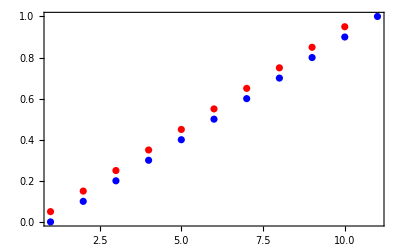

```mathematica
list=Table[i,{i,0,1,1/n}](*n+1コ*)
listM=Table[i,{i,1/n/2,1-1/n/2,1/n}](*nコ*)
opt={PlotRange->{{1,n+1},{0,1}},Frame->True};
Show[ListPlot[list,PlotStyle->Blue,opt],ListPlot[listM,PlotStyle->Red,opt]]
```

```mathematica
n=10;
Table[1/n/2+1/n*(i-1),{i,1,n,1}]

makelist[n_]:=Table[1/n/2+1/n*(i-1),{i,1,n,1}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

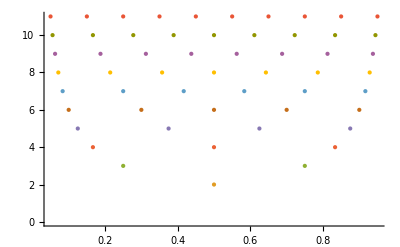

```mathematica
NumberLinePlot[Table[makelist[i],{i,0,10}]]
```

```mathematica
makelist[n]
```

{1/80,3/80,1/16,7/80,9/80,11/80,13/80,3/16,17/80,19/80,21/80,23/80,5/16,27/80,29/80,31/80,33/80,7/16,37/80,39/80,41/80,43/80,9/16,47/80,49/80,51/80,53/80,11/16,57/80,59/80,61/80,63/80,13/16,67/80,69/80,71/80,73/80,15/16,77/80,79/80}

```mathematica
n=10;
makelist[n]
Column@Table[{t0,t1},{t0,makelist[n]},{t1,makelist[n*t0(*t0は1/(2*n0)から始まるので，この時n1*t0=n1/2*n0*)]}]
Column@Table[{t0,t1},{t0,makelist[n]},{t1,makelist[n*t0(*t0は1/(2n)から始まるので，この時n*t0=1/2，そこで1/2を足して1とする*)+1/2]}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

{}
{{3/20,1/3}}
{{1/4,1/5},{1/4,3/5}}
{{7/20,1/7},{7/20,3/7},{7/20,5/7}}
{{9/20,1/9},{9/20,1/3},{9/20,5/9},{9/20,7/9}}
{{11/20,1/11},{11/20,3/11},{11/20,5/11},{11/20,7/11},{11/20,9/11}}
{{13/20,1/13},{13/20,3/13},{13/20,5/13},{13/20,7/13},{13/20,9/13},{13/20,11/13}}
{{3/4,1/15},{3/4,1/5},{3/4,1/3},{3/4,7/15},{3/4,3/5},{3/4,11/15},{3/4,13/15}}
{{17/20,1/17},{17/20,3/17},{17/20,5/17},{17/20,7/17},{17/20,9/17},{17/20,11/17},{17/20,13/17},{17/20,15/17}}
{{19/20,1/19},{19/20,3/19},{19/20,5/19},{19/20,7/19},{19/20,9/19},{19/20,11/19},{19/20,13/19},{19/20,15/19},{19/20,17/19}}

{{1/20,1/2}}
{{3/20,1/4},{3/20,3/4}}
{{1/4,1/6},{1/4,1/2},{1/4,5/6}}
{{7/20,1/8},{7/20,3/8},{7/20,5/8},{7/20,7/8}}
{{9/20,1/10},{9/20,3/10},{9/20,1/2},{9/20,7/10},{9/20,9/10}}
{{11/20,1/12},{11/20,1/4},{11/20,5/12},{11/20,7/12},{11/20,3/4},{11/20,11/12}}
{{13/20,1/14},{13/20,3/14},{13/20,5/14},{13/20,1/2},{13/20,9/14},{13/20,11/14},{13/20,13/14}}
{{3/4,1/16},{3/4,3/16},{3/4,5/16},{3/4,7/16},{3/4,9/16},{3/4,11/16},{3/4,13/16},{3/4,15/16}}
{{17/20,1/18},{17/20,1/6},{17/20,5/18},{17/20,7/18},{17/20,1/2},{17/20,11/18},{17/20,13/18},{17/20,5/6},{17/20,17/18}}
{{19/20,1/20},{19/20,3/20},{19/20,1/4},{19/20,7/20},{19/20,9/20},{19/20,11/20},{19/20,13/20},{19/20,3/4},{19/20,17/20},{19/20,19/20}}

```mathematica
n=20;
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n]},{t1,makelist[n*t0+1/2]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
```

```mathematica
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n]},{t1,makelist[n*t0+1/2]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
,{n,1,40,1}]
(*n0とn1を分けて調整したいが未だできていない*)
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n0]},{t1,makelist[1+Floor[n1*t0-n1/(2*n0)]]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
,{n1,1,40,1},{n0,1,40,1}]
```

Table::iterb: 反復演算{t0,makelist[1]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[1.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$17 t0+1/2]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$17 t0+1 Power[«2»]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[33]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[33.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[FE`n1$$19 t0-FE`n1$$19 Power[«2»]]]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[Plus[«2»]]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[1]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[1.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$20 t0+1/2]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$20 t0+1 Power[«2»]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[33]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[33.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[FE`n1$$21 t0-FE`n1$$21 Power[«2»]]]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[Plus[«2»]]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

ListPointPlot3D::ldata: {MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/66,1/2],«49»,«607»}は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[{MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/66,1/2],«49»,«607»}],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

ListPointPlot3D::ldata: {MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/2,1/2]}は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[{MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/2,1/2]}],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
ϵ=1;
f[r_]:=(ϵ^2*r^2+1)^(1/2.);
cord={{1,1},
{-1,1},
{1,-1},
{0,1},
{0,0},
{1,0},
{2,0},
{0,2},
{-1,2},
{-1,0},
{0,-1},
{2,-1}};

mat=Table[Table[f[Norm[{#1,#2}-cord[[origin]]]&@@cord[[i]]],{i,1,12,1}],{origin,1,12,1}]

intp[ps_,t0_,t1IN_]:=Module[{t1},
t1=(1-t0)*t1IN;
wx=Dot[Inverse[mat],Transpose[ps][[1]]];
wy=Dot[Inverse[mat],Transpose[ps][[2]]];
wz=Dot[Inverse[mat],Transpose[ps][[3]]];
Return[
{Sum[wx[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}],
Sum[wy[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}],
Sum[wz[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}]}]
];

Show[
ListPointPlot3D[ps],
ListPointPlot3D[Table[intp[ps,t0,t1],{t0,0,1,.1},{t1,0,1,.1}]]
]
```

{{1.,2.23607,2.23607,1.41421,1.73205,1.41421,1.73205,1.73205,2.44949,2.44949,2.44949,2.44949},{2.23607,1.,3.,1.41421,1.73205,2.44949,3.31662,1.73205,1.41421,1.41421,2.44949,3.74166},{2.23607,3.,1.,2.44949,1.73205,1.41421,1.73205,3.31662,3.74166,2.44949,1.41421,1.41421},{1.41421,1.41421,2.44949,1.,1.41421,1.73205,2.44949,1.41421,1.73205,1.73205,2.23607,3.},{1.73205,1.73205,1.73205,1.41421,1.,1.41421,2.23607,2.23607,2.44949,1.41421,1.41421,2.44949},{1.41421,2.44949,1.41421,1.73205,1.41421,1.,1.41421,2.44949,3.,2.23607,1.73205,1.73205},{1.73205,3.31662,1.73205,2.44949,2.23607,1.41421,1.,3.,3.74166,3.16228,2.44949,1.41421},{1.73205,1.73205,3.31662,1.41421,2.23607,2.44949,3.,1.,1.41421,2.44949,3.16228,3.74166},{2.44949,1.41421,3.74166,1.73205,2.44949,3.,3.74166,1.41421,1.,2.23607,3.31662,4.3589},{2.44949,1.41421,2.44949,1.73205,1.41421,2.23607,3.16228,2.44949,2.23607,1.,1.73205,3.31662},{2.44949,2.44949,1.41421,2.23607,1.41421,1.73205,2.44949,3.16228,3.31662,1.73205,1.,2.23607},{2.44949,3.74166,1.41421,3.,2.44949,1.73205,1.41421,3.74166,4.3589,3.31662,2.23607,1.}}

-Graphics3D-

### データ

```mathematica
tab ={{{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460}},{{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920}},{{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670}},{{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,-5.257310,8.506510},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000}},{{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800}},{{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800}},{{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{4.253250,-5.877850,6.881910},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-4.253250,-5.877850,6.881910},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380}},{{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-6.937800,-7.020460,1.606220}},{{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680},{6.881910,-4.253250,-5.877850},{4.253250,-5.877850,-6.881910},{5.000000,-3.090170,-8.090170},{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570}},{{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460}},{{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460}},{{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890}},{{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{5.257310,8.506510,0.000000},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000}},{{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,1.624600},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-8.090170,5.000000,3.090170},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000}},{{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-4.253250,-5.877850,6.881910},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660}},{{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310}},{{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{3.090170,8.090170,5.000000},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920}},{{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-5.000000,3.090170,8.090170},{-4.253250,5.877850,6.881910},{-6.937800,7.020460,1.606220}},{{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000}},{{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250}},{{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000}},{{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800}},{{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-5.877850,6.881910,-4.253250},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-5.877850,6.881910,4.253250}},{{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-6.937800,7.020460,-1.606220}},{{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,8.506510,-5.257310},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,-2.628660},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680}},{{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{4.338890,8.626680,2.598920},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920}},{{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890}},{{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000}},{{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670}},{{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920}},{{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{8.506510,5.257310,0.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{1.624600,9.510570,-2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920}},{{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{5.877850,6.881910,-4.253250},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570}},{{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,2.628660},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-8.506510,-5.257310,0.000000}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,2.598920},{1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{-4.338890,-8.626680,2.598920}},{{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{3.090170,-8.090170,-5.000000},{1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000}},{{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-5.877850,-6.881910,-4.253250},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890}},{{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-1.624600,-9.510570,-2.628660}},{{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.619380,0.000000,2.732670},{-9.619380,0.000000,-2.732670},{-8.626680,-2.598920,-4.338890},{-6.937800,-7.020460,-1.606220}},{{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-5.877850,-6.881910,4.253250},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510}},{{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{4.338890,-8.626680,2.598920},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890}},{{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680}},{{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.619380,0.000000,-2.732670},{9.619380,0.000000,2.732670},{8.626680,-2.598920,4.338890},{6.937800,-7.020460,1.606220}},{{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680}},{{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220}},{{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{4.338890,-8.626680,-2.598920},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,-2.628660},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000}},{{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-5.877850,6.881910,4.253250},{-6.881910,4.253250,5.877850},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-5.000000,-3.090170,8.090170},{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800}},{{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460}},{{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{5.000000,-3.090170,8.090170},{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680}},{{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680}},{{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{2.598920,4.338890,8.626680},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.628660,1.624600,9.510570},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310}},{{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{0.000000,0.000000,10.000000},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310}},{{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.257310,0.000000,8.506510},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910}},{{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{5.257310,0.000000,8.506510},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600}},{{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{7.020460,-1.606220,-6.937800},{2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,2.732670,-9.619380}},{{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{7.020460,1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600}},{{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680}},{{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510}},{{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{6.881910,-4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670}},{{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.257310,0.000000,-8.506510},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{5.000000,3.090170,-8.090170},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910}},{{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910}},{{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-7.020460,1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600}},{{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670},{9.510570,2.628660,-1.624600},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{8.090170,5.000000,-3.090170},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600}},{{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,-1.624600},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,-3.090170},{8.506510,0.000000,-5.257310},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600}},{{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,1.606220,6.937800}},{{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,3.090170},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600}},{{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000},{-1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,2.598920},{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,1.606220}},{{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660}},{{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,1.606220},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890}},{{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850}},{{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660}},{{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220}},{{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,1.606220}},{{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170}},{{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170}},{{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000}},{{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250},{1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910}},{{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,2.628660}},{{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600}},{{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890}},{{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660}},{{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{5.257310,8.506510,0.000000},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.877850,6.881910,-4.253250},{2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,4.253250}},{{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{4.338890,8.626680,2.598920},{4.338890,8.626680,2.598920},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000}},{{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910},{-4.338890,-8.626680,-2.598920},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460}},{{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850}},{{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250}},{{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,2.598920},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000}},{{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{6.881910,-4.253250,-5.877850},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600}},{{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{8.090170,-5.000000,-3.090170},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,1.606220},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,-2.598920},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660}},{{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460}},{{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,-4.253250},{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170}},{{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460}},{{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000}},{{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,2.598920},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220}},{{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660}},{{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,-2.628660}},{{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660}},{{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460}},{{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000}},{{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800}},{{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910}},{{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800}},{{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460}},{{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-2.598920,4.338890,8.626680}},{{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-5.257310,0.000000,8.506510},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680}},{{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910},{2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{-2.628660,-1.624600,9.510570}},{{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{5.877850,-6.881910,4.253250},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570}},{{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.877850,-6.881910,4.253250}},{{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910}},{{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170}},{{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570}},{{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570}},{{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380}},{{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{-2.598920,4.338890,-8.626680},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310}},{{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920}},{{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680}},{{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800}},{{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570}},{{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680}},{{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-8.506510,-5.257310},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{2.598920,-4.338890,-8.626680}},{{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{6.881910,-4.253250,-5.877850},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460}},{{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{2.598920,-4.338890,-8.626680},{4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310}},{{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570}},{{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910}},{{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910},{-2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850}},{{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660}},{{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380}},{{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{-1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310},{5.257310,0.000000,8.506510},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{8.626680,2.598920,4.338890}},{{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800}},{{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{8.626680,2.598920,4.338890},{6.881910,4.253250,5.877850},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{5.877850,6.881910,4.253250},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510}},{{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,1.624600},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600}},{{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850}},{{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.877850,-6.881910,4.253250}},{{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600}},{{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170}},{{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670}},{{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310},{-6.881910,4.253250,5.877850},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-7.020460,-1.606220,6.937800}},{{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850},{-5.257310,0.000000,8.506510},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910}},{{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.257310,0.000000,8.506510},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850}},{{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800}},{{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890}},{{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,2.732670},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850}},{{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-8.626680,2.598920,4.338890},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800}},{{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800},{-9.619380,0.000000,2.732670},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800}},{{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310},{9.510570,2.628660,-1.624600},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.510570,2.628660,1.624600},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,1.606220,-6.937800}},{{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170}},{{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850}},{{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{8.090170,-5.000000,-3.090170},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680}},{{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{6.881910,-4.253250,-5.877850},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850}},{{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170}},{{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670}},{{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800}},{{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800},{9.619380,0.000000,-2.732670},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{7.020460,1.606220,-6.937800}},{{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-5.257310,0.000000,-8.506510},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-8.626680,2.598920,-4.338890}},{{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600},{-6.881910,4.253250,-5.877850},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000}},{{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-8.626680,2.598920,-4.338890},{-6.881910,4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-5.877850,6.881910,-4.253250},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510}},{{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800}},{{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850}},{{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250}},{{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,1.624600},{-9.510570,2.628660,-1.624600}},{{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670}},{{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-7.020460,-1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,-1.624600},{-8.626680,2.598920,-4.338890}},{{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000}},{{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000}},{{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000}},{{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800},{-4.253250,5.877850,6.881910},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-5.257310,0.000000,8.506510}},{{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,8.506510,5.257310},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680}},{{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{0.000000,8.506510,5.257310},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,4.253250}},{{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{-5.877850,6.881910,4.253250},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660}},{{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-6.937800,7.020460,-1.606220}},{{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250}},{{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000}},{{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,-2.598920}},{{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,5.000000},{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910}},{{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170}},{{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850}},{{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-6.881910,4.253250,5.877850}},{{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310}},{{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{-4.338890,8.626680,2.598920}},{{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310}},{{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000}},{{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-8.090170,5.000000,-3.090170},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800}},{{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570}},{{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.937800,7.020460,1.606220}},{{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600}},{{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-2.732670,9.619380,0.000000}},{{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510}},{{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460}},{{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170}},{{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{4.253250,5.877850,6.881910},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660}},{{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310}},{{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510}},{{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.626680,2.598920,4.338890},{9.619380,0.000000,2.732670},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220}},{{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850}},{{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800}},{{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250}},{{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920}},{{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{6.881910,4.253250,5.877850},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000}},{{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910},{4.338890,8.626680,-2.598920},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460}},{{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920}},{{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570}},{{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310}},{{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220}},{{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660}},{{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-3.090170,-8.090170,5.000000},{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890}},{{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-6.881910,-4.253250,5.877850},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570}},{{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680}},{{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250}},{{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-1.606220,-6.937800,7.020460},{-2.598920,-4.338890,8.626680},{-7.020460,-1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220}},{{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570},{-4.253250,-5.877850,6.881910},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510}},{{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920}},{{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910}},{{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660}},{{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920}},{{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000}},{{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600}},{{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-4.253250,-5.877850,-6.881910},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510}},{{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000}},{{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510}},{{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920}},{{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850}},{{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,-2.732670},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670}},{{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600}},{{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.338890,-8.626680,-2.598920}},{{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-6.881910,-4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-8.090170,-5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570}},{{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920}},{{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-6.881910,-4.253250,5.877850},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800}},{{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-6.881910,-4.253250,5.877850},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170}},{{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920}},{{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850}},{{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{6.881910,-4.253250,5.877850},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000}},{{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{6.937800,-7.020460,1.606220},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910}},{{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,1.606220},{8.626680,-2.598920,4.338890},{7.020460,-1.606220,6.937800},{2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920}},{{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510},{6.881910,-4.253250,5.877850},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890}},{{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,1.624600},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600}},{{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170}},{{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310}},{{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600}},{{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910}},{{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{7.020460,-1.606220,-6.937800}},{{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170}},{{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920},{4.253250,-5.877850,6.881910},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220}},{{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660}},{{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{6.937800,-7.020460,-1.606220}},{{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570},{4.253250,-5.877850,-6.881910},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510}},{{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380}},{{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850}},{{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.257310,0.000000,8.506510},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910}},{{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680}},{{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510}},{{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380}},{{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.598920,4.338890,8.626680},{-2.628660,1.624600,9.510570}},{{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680}},{{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510}},{{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380}},{{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310}},{{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460}},{{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570}},{{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,-2.732670,-9.619380},{-2.598920,-4.338890,-8.626680},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680}},{{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570}},{{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460}},{{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850}},{{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{-2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570}},{{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850},{5.257310,0.000000,-8.506510},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890}},{{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310}}};
```

### データ２

```mathematica
tab={{{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{49.999975,149.999913,30.999939},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964}},{{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018}},{{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937},{50.000046,150.000022,0.999974},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020}},{{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{29.999937,170.000209,31.000020}},{{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{30.000029,150.000265,1.000037},{100.000155,49.999935,31.000062}},{{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937}},{{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{99.999919,50.000055,1.000009},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939}},{{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{99.999919,50.000055,1.000009},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{29.999937,170.000209,31.000020},{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973}},{{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{99.999919,50.000055,1.000009},{120.000090,170.000246,31.000018}},{{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062}},{{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{119.999959,169.999860,0.999946},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{30.000091,169.999854,0.999949},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016}},{{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940}},{{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{100.000155,49.999935,31.000062},{29.999674,149.999628,30.999937}},{{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973}},{{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949}},{{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{119.999959,169.999860,0.999946},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009}},{{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974}},{{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{120.000090,170.000246,31.000018},{29.999674,149.999628,30.999937}},{{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{99.999989,150.000055,0.999964},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939}},{{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{49.999838,49.999926,30.999973}},{{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949}},{{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{100.000155,49.999935,31.000062},{119.999982,149.999904,30.999940}}};
```

### テスト

```mathematica
makelist[n_]:=Table[1/n/2+1/n*(i-1),{i,1,n,1}]
```

```mathematica
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
surfaceTab12=ParallelTable[
ParametricPlot3D[intp[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

-Graphics3D-

```mathematica
surfaceTab12=ParallelTable[
ParametricPlot3D[interpCubic12RangeChanged[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

```mathematica
surfaceTab12=ParallelTable[
ParametricPlot3D[interpQuadIDW12NewRangeChanged[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

```mathematica
(*surfaceTab6=ParallelTable[
ParametricPlot3D[interpQuadRangeChanged0to1[tab[[i]][[1;;6]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];*)
```

```mathematica
(*{Show[surfaceTab6],Show[surfaceTab12]}*)
```

```mathematica
{,}
```

```mathematica
surfaceTab6=ParallelTable[
(*分割数nを三角形１辺の長さによって変化させる*)
Module[{n0,n1,data,a,b,c,center,e},
e=10^-5;
a=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],e,e];
b=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1-e,1-e];
c=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1-e,0];
center=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1/2,1/2];
n0=Floor[Norm[a-Mean[{b,c}]]/2];
n1=Floor[Norm[b-c]/2];
data =Table[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],t0,t1],{t0,makelist[n0]},{t1,makelist[1+Floor[n0*t0](*1+Floor[n1*t0-n1/(2*n0)]*)]}];
ListPointPlot3D[Flatten[data,1],
PlotStyle->{PointSize[0.005](*,col[[Mod[i,Length@col]]]*)}]
]
,{i,1,Length[tab],1}];
Show[surfaceTab6,PlotRange->All]
```

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

```mathematica
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
EPS=10^-7;
VVVpoints=tab;
Show[ParallelTable[ParametricPlot3D[interp[tab[[i]],t0/2,(1-t0+t0/(1-t0)*t1)/2],{t0,EPS,1-EPS},{t1,EPS,1-EPS-t0},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}
],{i,1,Length[VVVpoints]/10}],PlotRange->All]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

```mathematica
Plot[1/2+Tanh[t/3-3]/2,{t,0,20}]
```